This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 6 Annular power expansions ch6AnularExpansions.nb

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=7;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (-3319766398771200000+1 z)+(23238364791398400000) w+(-77030436760058880000) w^2+(161326036746072576000) w^3+(-240180965385332025600) w^4+(271057611231886800384) w^5+(-241386405085113410304) w^6+(174299255833816957824) w^7+(-104039758639368727776) w^8+(52067305426360848992) w^9+(-22077583830099907600) w^10+(7993549830308360568) w^11+(-2485349318616140689) w^12+(666179931589106948) w^13+(-154307800127905488) w^14+(30917671615556572) w^15+(-5356632994052156) w^16+(801097015860804) w^17+(-103080193140016) w^18+(11355388042796) w^19+(-1063406184918) w^20+(83839010860) w^21+(-5491243184) w^22+(293354100) w^23+(-12452860) w^24+(404012) w^25+(-9408) w^26+(140) w^27+(-1) w^28

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2: Compute singular data and annular template

```mathematica
implicitF[z_,w_]=$theFunction;
 {$theSingularList,argList,$zeroIndexes,$poleIndexes,$minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}=getAnnularTemplate[$theFunction];
```

poleIndexes: {1,8}

## Section 3: Display annular template

```mathematica
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
```

a_n | s_n | Annuli | Perim | Arg | Monodromy | support | Cont |   |  
  | 1 | 0 |   |   |   |   | {} |   |  
1 |   | {0.,0.5} | 0.25 |   |   |   | {} |   |  
  | 2 | 0.-0.5 ⅈ | 0.158927 | -1.5708 |   |   | {} |   |  
  | 3 | 0.+0.5 ⅈ | 0.158927 | 1.5708 |   |   | {} |   |  
2 |   | {0.5,0.624261} | 0.562131 |   |   |   | {} |   |  
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | -2.44093 |   |   | {} |   |  
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | 2.44093 |   |   | {} |   |  
3 |   | {0.624261,0.954195} | 0.789228 |   |   |   | {} |   |  
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | -1.36048 |   |   | {} |   |  
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | 1.36048 |   |   | {} |   |  
4 |   | {0.954195,1.33333} | 1.14376 |   |   |   | {} |   |  
  | 8 | 1.33333 | 0.205603 | 0. |   |   | {} |   |  
5 |   | {1.33333,1.7028} | 1.51807 |   |   |   | {} |   |  
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | -0.329278 |   |   | {} |   |  
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | 0.329278 |   |   | {} |   |  
6 |   | {1.7028,5.7028} | 3.7028 |   |   |   | {} |   |

## Section 4: Import annular table with singular and annular monodromies

```mathematica
If[FileExistsQ[annularTableWithMonodromiesFileName[$theTestCase]],
Print["Importing annular table with monodromies from file: ",annularTableWithMonodromiesFileName[$theTestCase]];
 {annulusTable,annulusTableR,annulusTableReport}=Import[annularTableWithMonodromiesFileName[$theTestCase]];
annularResidueTable={#[[1]],#[[2]],#[[3]],#[[4]],#[[6]]}&/@ annulusTableR;
annularResidueReport=Prepend[annularResidueTable,{"a_n Index","s_n Index","a_n or s_n",Column[{"monodromy","radius"},Alignment->Center],"Monodromy"}];

monodromyGridReport=Style[Labeled[Grid[annularResidueReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold,Black],Top],10];
Print[monodromyGridReport];
,
Print[Style[annularTableWithMonodromiesFileName[$theTestCase]<>" not found during import.",Red]];
];
```

Importing annular table with monodromies from file: D:\algFunctionBook\data\testCase0017\annularTableWithMonodromies.m

a_n Index | s_n Index | a_n or s_n | monodromy
radius | Monodromy
  | 1 | 0 | 0.166667 | {{1},{2},{3}}
1 |   | {0.,0.5} | 0.25 | {{1},{2},{3}}
  | 2 | 0.-0.5 ⅈ | 0.158927 | {{2,3},{1}}
  | 3 | 0.+0.5 ⅈ | 0.158927 | {{2,3},{1}}
2 |   | {0.5,0.624261} | 0.562131 | {{1},{2},{3}}
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | {{2,3},{1}}
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | {{2,3},{1}}
3 |   | {0.624261,0.954195} | 0.789228 | {{1,3,2}}
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | {{1,2},{3}}
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | {{1,2},{3}}
4 |   | {0.954195,1.33333} | 1.14376 | {{1,3,2}}
  | 8 | 1.33333 | 0.205603 | {{1},{2},{3}}
5 |   | {1.33333,1.7028} | 1.51807 | {{1,3,2}}
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | {{2,3},{1}}
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | {{1,3},{2}}
6 |   | {1.7028,2.7028} | 2.2028 | {{1},{2},{3}}testCase0017

## Section 5: Select annulus and monodromy index

### Section 5.1: Annular and Branch menu

```mathematica
segmentMenu=Labeled[Column[{Row[{Style["AnnulusIndex:",Black,Bold],Spacer[5],InputField[Dynamic@$selectedAnnulus,FieldSize->2],Spacer[12],Style["Branch index:",Black,Bold],Spacer[5],InputField[Dynamic@$selectedMonodromyIndex,FieldSize->2]}],
Row[{Style["Plot type: ",Black,Bold],RadioButtonBar[Dynamic[$plotType],{Re,Im}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}]
},Frame->True,FrameStyle->Thick],Style["Annulus and Branch Menu",Bold,Black],Top]
```

AnnulusIndex:Branch index:
Plot type:  | Re   | Im
Show plot label Annulus and Branch Menu

### Section 5.2: Generate branch plot

```mathematica
theAnnulusTable=annulusTable;


If[1<=$selectedAnnulus<=Length@theAnnuli,
{aIndex,sIndex}=getSingTableIndexes[annulusTable,$selectedAnnulus];
$selectedMonodromyList=annulusTable[[aIndex,6]];
If[1<=$selectedMonodromyIndex<=Length@$selectedMonodromyList,
$selectedMonodromyList=annulusTable[[aIndex,6]];
$selectedBranch=$selectedMonodromyList[[$selectedMonodromyIndex]];
$selectedBranchSize=Length@$selectedMonodromyList[[$selectedMonodromyIndex]];
plotLabel=Column[{Style[$theTestCase],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];


rMin=plottingRadiiTable[[$selectedAnnulus,1]];
rMax=Last[plottingRadiiTable[[$selectedAnnulus]]];
annulusDomain=Rationalize[annulusTable[[aIndex,3]],0];
Print["Annulus: ",annulusDomain//N];

theAnnulus=theAnnulusTable[[aIndex,3]];

rNorm=theAnnulusTable[[aIndex,4]];

tStart=$thetaV;
tEnd= tStart+2 Pi $selectedBranchSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

radiusRange=Array[#&,40,theAnnulus];
plotMin=-theAnnulus[[2]];
plotMax=theAnnulus[[2]];
(*
{"radialSegments"->15,"arcSegments"->24,"totalIntegrationSteps"->2500000,"maxStepSize"->1/1000,"workingPrecision"->50}
*)
theBranchSet=getBranchPlot[theAnnulusTable,$plotType,$selectedAnnulus,$selectedMonodromyIndex,"radialSegments"->15,"arcSegments"->50];

 branchPlot=Table[
rowA=theBranchSet[[k]]//N;
rowB=theBranchSet[[k+1]]//N;
pTable=Table[{If[$plotType===Re,Blue,Red],Opacity[0.5],Polygon[{rowA[[j]],rowA[[j+1]],rowB[[j+1]],rowB[[j]]}]},{j,1,(Length@rowA)-1}];
pTable,
{k,1,(Length@theBranchSet)-1}
];

realDifferentialBranchPlot= Show[Graphics3D@{branchPlot},Axes->True,AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style[$plotType,14,Black,Bold]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{0,0,-1}},FaceGridsStyle->Directive[Black,Bold],ImageSize->300,BoxRatios->{1, 1, 1},ImageSize->400,PlotLabel->If[$showPlotLabel,plotLabel,None]];

pRange=PlotRange[realDifferentialBranchPlot];


{rNorm,zStart,wStart}=getMedialStartVals[annulusTable,$selectedAnnulus,$selectedMonodromyIndex,$thetaV,implicitF];

startingWG=Graphics3D@{PointSize[0.025],Red,Point@{Re@zStart,Im@zStart,$plotType@wStart}};
Print[Show[{realDifferentialBranchPlot,startingWG},PlotRange->All,PlotLabel->If[$showPlotLabel,plotLabel,None]]];
,
Print["Monodromy index out of range"];
];
,
Print["Annulus index out of range"]
]
```

Annulus: {0.954195,1.33333}

tStart: 0.523599

tEnd: 19.3732

-Graphics3D-

### Section 5.3: Generate low-precision medial contour over branch and confirm visually

```mathematica
(*
 set up low precision medial contour
*)

 rationalRNorm=Rationalize[rNorm,10^-25];
precisionVal=20;

{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$selectedAnnulus,$selectedMonodromyIndex,precisionVal,1/2];
Print["prec: ",Precision@lowPrecMedialSol];
```

Setting rNorm: 1.14376

tStart: 0.523599

tEnd: 19.3732

medialSol: -1.3842-0.437913 ⅈ

prec: 20.

```mathematica
medialPlot=ParametricPlot3D[{Re@z,Im@z,Re@lowPrecMedialSol[t]}/.z->rNorm Exp[I t],{t,tStart+0.025,tEnd-0.15},PlotStyle->{Thickness[0.01],Yellow}];

Show[{realDifferentialBranchPlot,medialPlot,startingWG},Axes->True,AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style[$plotType,14,Black,Bold]},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{0,0,-1}},FaceGridsStyle->Directive[Black,Bold],ImageSize->300,BoxRatios->{1, 1, 1},ImageSize->400,PlotLabel->If[$showPlotLabel,plotLabel,None]]
```

-Graphics3D-

## Section 6: Generating multi-precision medial contours

### Section 6.1: Check if multi-medial contours already saved to disc

```mathematica
If[TrueQ@FileExistsQ@medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch],
Print["Multi-medial contours on disc"];
,
Print["Multi-medial files not found"];
];
```

Multi-medial contours on disc

### Section 6.2: Generate multi-medial contours

```mathematica
(*
 edit the $multiMedialAnalyticPrecisionArray as needed to identify residuals.  For low-degree function, 25 and 50 digit precisions are adequate.  Higher precision such as 25,50, and 75 or even higher may be needed for problem functions
*)

startTime=TimeObject[Now];
$multiMedialAnalyticPrecisionArray={25,50};
 totalMedialRuns=Length@$multiMedialAnalyticPrecisionArray;
DistributeDefinitions[$selectedAnnulus,$selectedMonodromyIndex];

medialTable=ParallelTable[
Print["contourPrecision: ",contourPrecision];
{tStart,tEnd,rNorm,medialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$selectedAnnulus,$selectedMonodromyIndex,contourPrecision,1/2];
(*
 check the accuracy of the integration with respect to actual funtion values
*)
Print["$selectedBranchSize: ",$selectedBranchSize];
 testW=medialSol[tEnd];
wVals=w/.NSolve[$theFunction==0/.z->rNorm Exp[I tEnd],w,WorkingPrecision->250];
actualAccuracy=Min@(Abs[#-testW]&/@ wVals);
Print["actual accuracy of integration: ",actualAccuracy//N];
accuracyExponent=MantissaExponent[actualAccuracy][[2]];
{medialSol,contourPrecision,accuracyExponent,$selectedBranchSize},
{contourPrecision,$multiMedialAnalyticPrecisionArray}
];
endTime=TimeObject[Now];
Print["Time to compute medial contours: ",endTime-startTime];
```

contourPrecision: 25

contourPrecision: 50

Setting rNorm: 1.14376

Setting rNorm: 1.14376

tStart: 0.523599

tStart: 0.523599

tEnd: 19.3732

tEnd: 19.3732

medialSol: -1.3842-0.437913 ⅈ

$selectedBranchSize: 3

actual accuracy of integration: 8.92535×10^-21

medialSol: -1.3842-0.437913 ⅈ

$selectedBranchSize: 3

actual accuracy of integration: 5.96933×10^-29

Time to compute medial contours: 1.35844 min

### Section 6.3: Exporting multi-medial contours to file

```mathematica
(* 
 save medialTable 
*)
Print["Exporting multimedial table to ",medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
AbsoluteTiming[ Export[medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch],medialTable,OverwriteTarget->True];]
Print["medialTable size: ",ByteCount@medialTable];
```

Exporting multimedial table to D:\algFunctionBook\data\testCase0017\a4b132multiMedialTable.m

{25.2056,Null}

medialTable size: 103892400

### Section 6.4: Import multi-medial contours from file

```mathematica
If[FileExistsQ[medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],
Print["Importing multimedial file ",medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
   AbsoluteTiming[medialTable=Import[medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];]
(*DistributeDefinitions[medialTable];*)
Print["medialTable precision: ",medialTable[[All,2]]];
totalMedialRuns=Length@medialTable;
Print["Size of medialTable: ", ByteCount@medialTable];
,
Print[Style[medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];
```

Importing multimedial file D:\crossPlatformBook\Data\testCase0008\a5b3multiMedialTable.m

{5.32294,Null}

medialTable precision: {25,50,75}

Size of medialTable: 61105840

### Section 6.5: Generate plot of medial contour over branch

```mathematica
medialSol=medialTable[[1,1]];
tStart//N
tEnd//N
medialPlot=ParametricPlot3D[{Re@z,Im@z,Re@medialSol[t]}/.z->rNorm Exp[I t],{t,tStart,tEnd},PlotStyle->Yellow,PlotLabel->If[$showPlotLabel,plotLabel,None]];
Show[{realDifferentialBranchPlot,medialPlot},BoxRatios->{1,1,1}]
```

0.523599

19.3732

-Graphics3D-

```mathematica
(*
 draw medial contour interactively via Manipulate
*)
 medialSol=medialTable[[1,1]];
Manipulate[
ParametricPlot3D[{Re@z,Im@z,Re@medialSol[t]}/.z->rNorm Exp[I t],{t,tStart,tStop},PlotStyle->Black,PlotRange->pRange,BoxRatios->{1, 1, 1}],
{{tStop,tStart+0.1},tStart+0.01,tEnd}
]
```

0.523599

13.09

## Section 7: Create multi-medial analytic terms

### Section 7.1: Multi-medial analytic menu

```mathematica
multiMedialSegmentMenu=Labeled[Column[{Row[{Style["Integration partitions: ",Black,Bold],RadioButtonBar[Dynamic[$integrationPartition],{1,2,3}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Spacer[20],Style["Start index: "],Spacer[10],InputField[Dynamic@$analTermMin,FieldSize->4]}],
Row[{Spacer[20],Style["End index: "],Spacer[24],InputField[Dynamic@$analTermMax,FieldSize->4]}]
},Frame->True,FrameStyle->Thick],Style["Multi-medial analytic Menu",Bold,Black],Top]
```

Integration partitions:  | 1   | 2   | 3
Show plot label 
Start index: 
End index: Multi-medial analytic Menu

### Section 7.2: Compute unreformed multi-medial analytic terms

```mathematica
startTime=TimeObject[Now];
DistributeDefinitions[$integrationPartition,$analTermMin,$analTermMax,$selectedBranchSize];
totalMedialRuns=Length@medialTable;
Print[Style["Analyzing annulus "<>ToString@$selectedAnnulus<>" branch "<>ToString@$selectedBranch,12]];
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$integrationPartition+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
Print["Partitioning integration as: ",thePartitions];
totalMedialRuns=Length@medialTable;

at2=AbsoluteTiming[
residualAnalyticTerms=ParallelTable[
medialSol=medialTable[[medialIndex,1]];
 medialPrec=medialTable[[medialIndex,2]];
medialAcc=medialTable[[medialIndex,3]];
theCycleSize=medialTable[[medialIndex,4]];
Print["Analyzing medial index ",medialIndex," with precision ",medialPrec];
medialPrec=(Precision@medialSol);
analTable=Table[
If[Mod[k,25]==0,
Print["Current index ",k];
];


If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[medialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->medialPrec,AccuracyGoal->medialPrec/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[medialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->medialPrec,AccuracyGoal->medialPrec/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,$analTermMin,$analTermMax}
];
{medialIndex,medialPrec,medialAcc,analTable},
{medialIndex,1,Length@medialTable}
];];
endTime=TimeObject[Now]
Print["Time to compute multi-medial analytic contours: ",endTime-startTime]
```

Analyzing annulus 4 branch {1, 3, 2}

Partitioning integration as: {{π/6,(19 π)/6},{(19 π)/6,(37 π)/6}}

Analyzing medial index 1 with precision 25

Analyzing medial index 2 with precision 50

Current index 0

Current index 0

Current index 25

Current index 25

Current index 50

Current index 50

13:14:21GMT-5TimeObject[{13,14,21.1158435},Instant,-5.]

Time to compute multi-medial analytic contours: 2.13561 min

### Section 7.3 Generate grid report using multiple medial contour expansions

```mathematica
plotLabel=Column[{Row[{Style[$theTestCase]," analytic terms"}],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];



analyticData=Table[
If[iVal==1,
{residualAnalyticTerms[[1,4,All,1]],residualAnalyticTerms[[1,4,All,-2]]}
,
residualAnalyticTerms[[iVal,4,All,-2]]
]
,
{iVal,1,Length@residualAnalyticTerms}
];

errorReport=MapThread[List,FlattenAt[analyticData,1]];

errorReportR=MapThread[List,FlattenAt[analyticData,1]];

theHeading=Flatten@{"exp",#1[[2]]&/@ medialTable[[Range[Length@residualAnalyticTerms]]]};

(*theDisplay=Style[Grid[Prepend[Join[errorReport[[1;;7]],errorReportR[[-8;;]]],theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];
*)
theDisplay=Style[Grid[Prepend[errorReport,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];


Print[Column[{If[$showPlotLabel,plotLabel,""],theDisplay},Alignment->Center]]
accuracyExpList=-medialTable[[All,3]];
```

exp | 25 | 50
0 | -0.875+0. ⅈ | -0.875+0. ⅈ
1/3 | -1.907587303+0. ⅈ | -1.907587303+0. ⅈ
2/3 | -0.530371902+0. ⅈ | -0.530371902+0. ⅈ
1 | -0.65625+0. ⅈ | -0.65625+0. ⅈ
4/3 | -0.689002511+0. ⅈ | -0.689002511+0. ⅈ
5/3 | -0.4477237381+0. ⅈ | -0.4477237381+0. ⅈ
2 | -0.4921875+0. ⅈ | -0.4921875+0. ⅈ
7/3 | -0.4516205487+0. ⅈ | -0.4516205487+0. ⅈ
8/3 | -0.3616271271+0. ⅈ | -0.3616271271+0. ⅈ
3 | -0.369140625+0. ⅈ | -0.369140625+0. ⅈ
10/3 | -0.3272083923+0. ⅈ | -0.3272083923+0. ⅈ
11/3 | -0.2843626851+0. ⅈ | -0.2843626851+0. ⅈ
4 | -0.2768554688+0. ⅈ | -0.2768554687+0. ⅈ
13/3 | -0.2442616569+0. ⅈ | -0.2442616569+0. ⅈ
14/3 | -0.2197852143+0. ⅈ | -0.2197852143+0. ⅈ
5 | -0.2076416016+0. ⅈ | -0.2076416016+0. ⅈ
16/3 | -0.1840515557+0. ⅈ | -0.1840515557+0. ⅈ
17/3 | -0.167955331+0. ⅈ | -0.167955331+0. ⅈ
6 | -0.1557312012+0. ⅈ | -0.1557312012+0. ⅈ
19/3 | -0.1389695017+0. ⅈ | -0.1389695017+0. ⅈ
20/3 | -0.1273895466+0. ⅈ | -0.1273895466+0. ⅈ
7 | -0.1167984009+0. ⅈ | -0.1167984009+0. ⅈ
22/3 | -0.1048711201+0. ⅈ | -0.1048711201+0. ⅈ
23/3 | -0.09615091219+0. ⅈ | -0.09615091219+0. ⅈ
8 | -0.08759880066+0. ⅈ | -0.08759880066+0. ⅈ
25/3 | -0.07903193164+0. ⅈ | -0.07903193164+0. ⅈ
26/3 | -0.07234855048+0. ⅈ | -0.07234855048+0. ⅈ
9 | -0.06569910049+0. ⅈ | -0.06569910049+0. ⅈ
28/3 | -0.05947494427+0. ⅈ | -0.05947494427+0. ⅈ
29/3 | -0.05433654472+0. ⅈ | -0.05433654472+0. ⅈ
10 | -0.04927432537+0. ⅈ | -0.04927432537+0. ⅈ
31/3 | -0.04470384812+0. ⅈ | -0.04470384812+0. ⅈ
32/3 | -0.04076549894+0. ⅈ | -0.04076549894+0. ⅈ
11 | -0.03695574403+0. ⅈ | -0.03695574403+0. ⅈ
34/3 | -0.03357078934+0. ⅈ | -0.03357078934+0. ⅈ
35/3 | -0.03056747546+0. ⅈ | -0.03056747546+0. ⅈ
12 | -0.02771680802+0. ⅈ | -0.02771680802+0. ⅈ
37/3 | -0.02519438033+0. ⅈ | -0.02519438033+0. ⅈ
38/3 | -0.02291564122+0. ⅈ | -0.02291564122+0. ⅈ
13 | -0.02078760602+0. ⅈ | -0.02078760602+0. ⅈ
40/3 | -0.01890034353+0. ⅈ | -0.01890034353+0. ⅈ
41/3 | -0.01717867078+0. ⅈ | -0.01717867078+0. ⅈ
14 | -0.01559070451+0. ⅈ | -0.01559070451+0. ⅈ
43/3 | -0.0141753391+0. ⅈ | -0.0141753391+0. ⅈ
44/3 | -0.01287870482+0. ⅈ | -0.01287870482+0. ⅈ
15 | -0.01169302838+0. ⅈ | -0.01169302838+0. ⅈ
46/3 | -0.01063031884+0. ⅈ | -0.01063031884+0. ⅈ
47/3 | -0.009655957806+0. ⅈ | -0.009655957806+0. ⅈ
16 | -0.008769771288+0. ⅈ | -0.008769771288+0. ⅈ
49/3 | -0.007971519974+0. ⅈ | -0.007971519974+0. ⅈ
50/3 | -0.007240364547+0. ⅈ | -0.007240364547+0. ⅈ

### Section 7.4: Identify residual analytic terms

#### Create reducedAnalCoefList

```mathematica
(*
 second version
*)
 pureData=MapThread[List,ReIm@residualAnalyticTerms[[All,4,All,2]]];
Print["Precision of highest precision pureData: ",Precision@pureData[[All,-1]]];
pureExp=residualAnalyticTerms[[1,4,All,1]];
reducedFlag1=False;
imagZeroIndexes=0;
realZeroIndexes=0;
analyticCodeArray={};
reducedAnalCoefList=Table[
newDataList={};
coeffCode={0,0};
testRun=pureData[[iVal]];
realTrend=-MantissaExponent[Abs[testRun[[All,1]]//N]][[-2;;,2]];
imagTrend=-MantissaExponent[Abs[testRun[[All,2]]//N]][[-2;;,2]];
If[Differences@realTrend=={0},
AppendTo[newDataList,testRun[[-1,1]]];
coeffCode[[1]]=1;
,
realZeroIndexes++;
If[reducedFlag1,
Print[Style["real has differences",Red]];
];
];
If[Differences@imagTrend=={0},
AppendTo[newDataList,I testRun[[-1,2]]];
coeffCode[[2]]=1;
,
imagZeroIndexes++;
If[reducedFlag1,
Print[Style["imag has differences",Red]];

];
];
(*
 now update value of coef
*)
If[Length@newDataList==1,
newValue=newDataList[[1]];
,
If[Length@newDataList==2,
newValue=Plus@@newDataList;
,
newValue=0;
];
];
AppendTo[analyticCodeArray,{pureExp[[iVal]] $selectedBranchSize,pureExp[[iVal]],coeffCode}];
{pureExp[[iVal]],newValue z^pureExp[[iVal]]},
{iVal,1,Length@pureData}
];
(*Print["reducedAnalCoefList: ",reducedAnalCoefList//N];
*)

If[imagZeroIndexes==Length@pureData,
Print["Imag parts of all terms are zero!"];
,
If[imagZeroIndexes!=0,
Print[Style["Some real parts are zero but not all !,Red"]];
];
];
If[realZeroIndexes==Length@pureData,
Print["Real parts of all terms are zero!"];
,
If[realZeroIndexes!=0,
Print[Style["Some real parts are zero but not all"]];
];
]; 
Print["imagZeroIndexes: ",imagZeroIndexes];
Print["realZeroIndexes: ",realZeroIndexes];
reducedList={#[[1]],N[#[[2]]]}&/@reducedAnalCoefList;
Grid[Prepend[reducedList,{"exp","Term"}],Dividers->{{{True}},{True,True,{False},True}}]
Print["Precision of reducedAnalCoefList: ",Precision@reducedAnalCoefList[[2]]];
```

Precision of highest precision pureData: 18.3638

Imag parts of all terms are zero!

imagZeroIndexes: 51

realZeroIndexes: 0

exp | Term
0 | -0.875
1/3 | -1.90759 z^(1/3)
2/3 | -0.530372 z^(2/3)
1 | -0.65625 z
4/3 | -0.689003 z^(4/3)
5/3 | -0.447724 z^(5/3)
2 | -0.492188 z^2
7/3 | -0.451621 z^(7/3)
8/3 | -0.361627 z^(8/3)
3 | -0.369141 z^3
10/3 | -0.327208 z^(10/3)
11/3 | -0.284363 z^(11/3)
4 | -0.276855 z^4
13/3 | -0.244262 z^(13/3)
14/3 | -0.219785 z^(14/3)
5 | -0.207642 z^5
16/3 | -0.184052 z^(16/3)
17/3 | -0.167955 z^(17/3)
6 | -0.155731 z^6
19/3 | -0.13897 z^(19/3)
20/3 | -0.12739 z^(20/3)
7 | -0.116798 z^7
22/3 | -0.104871 z^(22/3)
23/3 | -0.0961509 z^(23/3)
8 | -0.0875988 z^8
25/3 | -0.0790319 z^(25/3)
26/3 | -0.0723486 z^(26/3)
9 | -0.0656991 z^9
28/3 | -0.0594749 z^(28/3)
29/3 | -0.0543365 z^(29/3)
10 | -0.0492743 z^10
31/3 | -0.0447038 z^(31/3)
32/3 | -0.0407655 z^(32/3)
11 | -0.0369557 z^11
34/3 | -0.0335708 z^(34/3)
35/3 | -0.0305675 z^(35/3)
12 | -0.0277168 z^12
37/3 | -0.0251944 z^(37/3)
38/3 | -0.0229156 z^(38/3)
13 | -0.0207876 z^13
40/3 | -0.0189003 z^(40/3)
41/3 | -0.0171787 z^(41/3)
14 | -0.0155907 z^14
43/3 | -0.0141753 z^(43/3)
44/3 | -0.0128787 z^(44/3)
15 | -0.011693 z^15
46/3 | -0.0106303 z^(46/3)
47/3 | -0.00965596 z^(47/3)
16 | -0.00876977 z^16
49/3 | -0.00797152 z^(49/3)
50/3 | -0.00724036 z^(50/3)

Precision of reducedAnalCoefList: 50.1497

```mathematica
(*
  now update grid with reduced terms
*)

analData=Table[
If[iVal==1,
{residualAnalyticTerms[[1,4,All,1]],residualAnalyticTerms[[1,4,All,2]]//N}
,
residualAnalyticTerms[[iVal,4,All,2]]//N]
,
{iVal,1,totalMedialRuns}
];
(*
 now append reduced terms to data
*)
Print["test"];

analErrorReport=MapThread[List,FlattenAt[analData,1]];
updatedAnalyticData=MapThread[Append[#1,#2]&,{analErrorReport,reducedAnalCoefList[[All,2]]}];
updatedAnalyticDataR=MapThread[Append[#1,#2]&,{analErrorReport,reducedAnalCoefList[[All,2]]//N}];

theHeading=Flatten@{"exp",#1[[2]]&/@ medialTable[[Range[totalMedialRuns]]]}
AppendTo[theHeading,"reformed Vals"];

theDisplay=Style[Grid[Prepend[updatedAnalyticDataR//N,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];


Print["Precision of reduced terms: ",Precision@updatedAnalyticData[[All,-1]]];
Print[Column[{If[$showPlotLabel,plotLabel,""],theDisplay},Alignment->Center]];
accuracyExpList=-medialTable[[All,3]]


reducedAnalyticSeries[z_]=Plus@@updatedAnalyticData[[All,-1]];

Print["Precision of reducedAnalyticSeries[z]:",Precision@reducedAnalyticSeries[z]]
```

test

{exp,25,50}

Precision of reduced terms: 49.7957

exp | 25 | 50 | reformed Vals
0. | -0.875+1.51738×10^-21 ⅈ | -0.875+8.21344×10^-31 ⅈ | -0.875
0.333333 | -1.90759-6.17831×10^-23 ⅈ | -1.90759+2.70386×10^-30 ⅈ | -1.90759 z^(1/3)
0.666667 | -0.530372+4.6265×10^-21 ⅈ | -0.530372-3.6216×10^-30 ⅈ | -0.530372 z^(2/3)
1. | -0.65625+1.32705×10^-21 ⅈ | -0.65625+5.16592×10^-31 ⅈ | -0.65625 z
1.33333 | -0.689003+1.3822×10^-21 ⅈ | -0.689003+2.96345×10^-31 ⅈ | -0.689003 z^(4/3)
1.66667 | -0.447724+3.10285×10^-21 ⅈ | -0.447724-2.1524×10^-30 ⅈ | -0.447724 z^(5/3)
2. | -0.492188+1.15451×10^-21 ⅈ | -0.492188+2.06274×10^-31 ⅈ | -0.492188 z^2
2.33333 | -0.451621+1.56128×10^-21 ⅈ | -0.451621-4.46634×10^-31 ⅈ | -0.451621 z^(7/3)
2.66667 | -0.361627+2.07771×10^-21 ⅈ | -0.361627-1.25644×10^-30 ⅈ | -0.361627 z^(8/3)
3. | -0.369141+9.9114×10^-22 ⅈ | -0.369141-6.71185×10^-33 ⅈ | -0.369141 z^3
3.33333 | -0.327208+1.37361×10^-21 ⅈ | -0.327208-6.25268×10^-31 ⅈ | -0.327208 z^(10/3)
3.66667 | -0.284363+1.41561×10^-21 ⅈ | -0.284363-7.75534×10^-31 ⅈ | -0.284363 z^(11/3)
4. | -0.276855+8.47187×10^-22 ⅈ | -0.276855-1.4744×10^-31 ⅈ | -0.276855 z^4
4.33333 | -0.244262+1.10927×10^-21 ⅈ | -0.244262-5.77048×10^-31 ⅈ | -0.244262 z^(13/3)
4.66667 | -0.219785+9.971×10^-22 ⅈ | -0.219785-5.20891×10^-31 ⅈ | -0.219785 z^(14/3)
5. | -0.207642+7.17027×10^-22 ⅈ | -0.207642-2.29528×10^-31 ⅈ | -0.207642 z^5
5.33333 | -0.184052+8.82549×10^-22 ⅈ | -0.184052-4.65192×10^-31 ⅈ | -0.184052 z^(16/3)
5.66667 | -0.167955+7.41531×10^-22 ⅈ | -0.167955-3.54852×10^-31 ⅈ | -0.167955 z^(17/3)
6. | -0.155731+6.17981×10^-22 ⅈ | -0.155731-2.42151×10^-31 ⅈ | -0.155731 z^6
6.33333 | -0.13897+6.9804×10^-22 ⅈ | -0.13897-3.54742×10^-31 ⅈ | -0.13897 z^(19/3)
6.66667 | -0.12739-1.37826×10^-22 ⅈ | -0.12739-2.60318×10^-31 ⅈ | -0.12739 z^(20/3)
7. | -0.116798-1.55877×10^-22 ⅈ | -0.116798-2.20357×10^-31 ⅈ | -0.116798 z^7
7.33333 | -0.104871-9.72046×10^-23 ⅈ | -0.104871-2.64325×10^-31 ⅈ | -0.104871 z^(22/3)
7.66667 | -0.0961509-1.48729×10^-22 ⅈ | -0.0961509-1.73533×10^-31 ⅈ | -0.0961509 z^(23/3)
8. | -0.0875988-1.4361×10^-22 ⅈ | -0.0875988-1.50479×10^-31 ⅈ | -0.0875988 z^8
8.33333 | -0.0790319-1.15094×10^-22 ⅈ | -0.0790319-1.54453×10^-31 ⅈ | -0.0790319 z^(25/3)
8.66667 | -0.0723486-1.43382×10^-22 ⅈ | -0.0723486-9.56331×10^-32 ⅈ | -0.0723486 z^(26/3)
9. | -0.0656991-1.30183×10^-22 ⅈ | -0.0656991-8.40213×10^-32 ⅈ | -0.0656991 z^9
9.33333 | -0.0594749-1.17298×10^-22 ⅈ | -0.0594749-6.81932×10^-32 ⅈ | -0.0594749 z^(28/3)
9.66667 | -0.0543365-1.30946×10^-22 ⅈ | -0.0543365-2.75993×10^-32 ⅈ | -0.0543365 z^(29/3)
10. | -0.0492743-1.1809×10^-22 ⅈ | -0.0492743-2.56087×10^-32 ⅈ | -0.0492743 z^10
10.3333 | -0.0447038-1.1294×10^-22 ⅈ | -0.0447038-9.34613×10^-33 ⅈ | -0.0447038 z^(31/3)
10.6667 | -0.0407655-1.17616×10^-22 ⅈ | -0.0407655+1.57887×10^-32 ⅈ | -0.0407655 z^(32/3)
11. | -0.0369557-1.05738×10^-22 ⅈ | -0.0369557+1.86182×10^-32 ⅈ | -0.0369557 z^11
11.3333 | -0.0335708-1.03764×10^-22 ⅈ | -0.0335708+2.76797×10^-32 ⅈ | -0.0335708 z^(34/3)
11.6667 | -0.0305675-1.04461×10^-22 ⅈ | -0.0305675+3.79444×10^-32 ⅈ | -0.0305675 z^(35/3)
12. | -0.0277168-9.67033×10^-23 ⅈ | -0.0277168+3.86072×10^-32 ⅈ | -0.0277168 z^12
12.3333 | -0.0251944-9.58312×10^-23 ⅈ | -0.0251944+4.53042×10^-32 ⅈ | -0.0251944 z^(37/3)
12.6667 | -0.0229156-9.48313×10^-23 ⅈ | -0.0229156+4.57836×10^-32 ⅈ | -0.0229156 z^(38/3)
13. | -0.0207876-9.03523×10^-23 ⅈ | -0.0207876+4.01462×10^-32 ⅈ | -0.0207876 z^13
13.3333 | -0.0189003-9.03123×10^-23 ⅈ | -0.0189003+4.32671×10^-32 ⅈ | -0.0189003 z^(40/3)
13.6667 | -0.0171787-8.89227×10^-23 ⅈ | -0.0171787+4.04951×10^-32 ⅈ | -0.0171787 z^(41/3)
14. | -0.0155907-8.59443×10^-23 ⅈ | -0.0155907+3.3409×10^-32 ⅈ | -0.0155907 z^14
14.3333 | -0.0141753-8.5422×10^-23 ⅈ | -0.0141753+3.02065×10^-32 ⅈ | -0.0141753 z^(43/3)
14.6667 | -0.0128787-8.37443×10^-23 ⅈ | -0.0128787+2.6396×10^-32 ⅈ | -0.0128787 z^(44/3)
15. | -0.011693-8.19278×10^-23 ⅈ | -0.011693+2.08034×10^-32 ⅈ | -0.011693 z^15
15.3333 | -0.0106303-8.14667×10^-23 ⅈ | -0.0106303+1.66301×10^-32 ⅈ | -0.0106303 z^(46/3)
15.6667 | -0.00965596-8.00488×10^-23 ⅈ | -0.00965596+1.00872×10^-32 ⅈ | -0.00965596 z^(47/3)
16. | -0.00876977-1.99039×10^-22 ⅈ | -0.00876977+5.541×10^-33 ⅈ | -0.00876977 z^16
16.3333 | -0.00797152-1.94381×10^-22 ⅈ | -0.00797152+3.11492×10^-33 ⅈ | -0.00797152 z^(49/3)
16.6667 | -0.00724036-1.89013×10^-22 ⅈ | -0.00724036-2.4151×10^-33 ⅈ | -0.00724036 z^(50/3)

{20,28}

Precision of reducedAnalyticSeries[z]:49.7957

### Section 7.5: Create: reducedAnalyticTerms, analyticResidueArray, analyticOrderIndexList

```mathematica
(*
  create final reduced analytic terms minus the residuals
*)
Print["analTermMax: ",$analTermMax];

reducedAnalyticTerms=DeleteCases[updatedAnalyticData[[All,-1]],0];

(*
 create reducedAnalyticCodeArray
*)

reducedAnalyticCodeArray= Cases[analyticCodeArray,{x_,y_,z_}/;z!={0,0}];
analyticResidueArray=reducedAnalyticCodeArray;
Print["analyticResidueArray: ",analyticResidueArray];

(*
 create sequence funtion (not used presently, set to zero )
*)
(*analyticSequenceFunction=FindSequenceFunction[reducedAnalyticCodeArray[[All,2]] $selectedBranchSize]*)
analyticSequenceFunction=0;

 (*
 use raw analytic terms of highest precision
*)
(*reducedAnalyticTerms=residualAnalyticTerms[[All,3]];*)
Precision@reducedAnalyticTerms

deleteLen=Length@reducedAnalyticTerms
If[deleteLen>0,
theExps=Exponent[#,z]&/@ reducedAnalyticTerms;
maxExp=Floor@Max@theExps;
nearElements=Nearest[theExps,Range[maxExp],2];

uniqueVals=nearElements[[All,1]];

newOrderList=(Position[theExps,x_/;x==#]&/@uniqueVals)//Flatten;
analyticOrderIndexList=MapThread[{#1,#2}&,{Range[maxExp],newOrderList}];
Print["analyticOrderIndexList {order,index}: ",analyticOrderIndexList];
,
analyticOrderIndexList={};
Print[Style["All analytic terms are zero!",Red]];
];
Print["Highest order analytic term: ",analyticOrderIndexList[[-1]]];
Print["Precision of deleted analytic terms: ",Precision@reducedAnalyticTerms];
Print["Last five terms: ",reducedAnalyticTerms[[-5]]];
```

analTermMax: 50

analyticResidueArray: {{0,0,{1,0}},{1,1/3,{1,0}},{2,2/3,{1,0}},{3,1,{1,0}},{4,4/3,{1,0}},{5,5/3,{1,0}},{6,2,{1,0}},{7,7/3,{1,0}},{8,8/3,{1,0}},{9,3,{1,0}},{10,10/3,{1,0}},{11,11/3,{1,0}},{12,4,{1,0}},{13,13/3,{1,0}},{14,14/3,{1,0}},{15,5,{1,0}},{16,16/3,{1,0}},{17,17/3,{1,0}},{18,6,{1,0}},{19,19/3,{1,0}},{20,20/3,{1,0}},{21,7,{1,0}},{22,22/3,{1,0}},{23,23/3,{1,0}},{24,8,{1,0}},{25,25/3,{1,0}},{26,26/3,{1,0}},{27,9,{1,0}},{28,28/3,{1,0}},{29,29/3,{1,0}},{30,10,{1,0}},{31,31/3,{1,0}},{32,32/3,{1,0}},{33,11,{1,0}},{34,34/3,{1,0}},{35,35/3,{1,0}},{36,12,{1,0}},{37,37/3,{1,0}},{38,38/3,{1,0}},{39,13,{1,0}},{40,40/3,{1,0}},{41,41/3,{1,0}},{42,14,{1,0}},{43,43/3,{1,0}},{44,44/3,{1,0}},{45,15,{1,0}},{46,46/3,{1,0}},{47,47/3,{1,0}},{48,16,{1,0}},{49,49/3,{1,0}},{50,50/3,{1,0}}}

49.7957

51

analyticOrderIndexList {order,index}: {{1,4},{2,7},{3,10},{4,13},{5,16},{6,19},{7,22},{8,25},{9,28},{10,31},{11,34},{12,37},{13,40},{14,43},{15,46},{16,49}}

Highest order analytic term: {16,49}

Precision of deleted analytic terms: 49.7957

Last five terms: -0.01063031884011749336916498014121895601370751400041 z^(46/3)

#### Create terms for outer annulus with finite number of analytic terms

```mathematica
reducedAnalyticTerms=DeleteCases[updatedAnalyticData[[All,-1]],0];
reducedAnalyticTerms//N
```

{-0.5}

```mathematica
analyticSequenceFunction=#&;

 (*
 use raw analytic terms of highest precision
*)
(*reducedAnalyticTerms=residualAnalyticTerms[[All,3]];*)
Precision@reducedAnalyticTerms

deleteLen=Length@reducedAnalyticTerms
If[deleteLen>0,
theExps=Exponent[#,z]&/@ reducedAnalyticTerms;
maxExp=Floor@Max@theExps;
nearElements=Nearest[theExps,Range[maxExp]];

uniqueVals=nearElements[[All,1]];

newOrderList=(Position[theExps,x_/;x==#]&/@uniqueVals)//Flatten;
analyticOrderIndexList={{0,1}};
Print["analyticOrderIndexList: ",analyticOrderIndexList];
,
analyticOrderIndexList={};
Print[Style["All analytic terms are zero!",Red]];
];
Print["Highest order analytic term: ",analyticOrderIndexList[[-1]]];
Print["Precision of deleted analytic terms: ",Precision@reducedAnalyticTerms];
```

75.

1

analyticOrderIndexList: {{0,1}}

Highest order analytic term: {0,1}

Precision of deleted analytic terms: 75.

### Section 7.6: Use Root Test to compute numerical upper convergence limit

```mathematica
segmentMenu=Labeled[Column[{
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Style["Series start index: "],Spacer[90],InputField[Dynamic@$analyticRootTestStartTerm,FieldSize->4]}],
Row[{Style["Series end index (negative): "],Spacer[24],InputField[Dynamic@$analyticRootTestEndTerm,FieldSize->4]}],
Row[{Checkbox[Dynamic[$analyticRootTestJoinPlot],{False,True}]," Join List plot points"}]
},Frame->True,FrameStyle->Thick],Style["Analytic Root Test parameters",Bold,Black],Top]
```

Show plot label 
Series start index: 
Series end index (negative): 
 Join List plot pointsAnalytic Root Test parameters

```mathematica
(* 
 Root Test
*)
plotLabel=Column[{Style[$theTestCase],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];


baseSeries=Plus@@reducedAnalyticTerms;

Print["Cycle size: ",$selectedBranchSize];

seriesLength=Length@baseSeries;
theexp=Exponent[baseSeries,z,List];
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=Coefficient[baseSeries,z,theexp];
If[$analyticRootTestStartTerm<1,
$analyticRootTestStartTerm=2;
,
If[$analyticRootTestEndTerm>-1,
$analyticRootTestEndTerm=-2;
];
];

cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^($selectedBranchSize/numVals[[k]])),25]},
{k,$analyticRootTestStartTerm,Length@clist+$analyticRootTestEndTerm}];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.025]},AxesOrigin->{0,0}];


 (* 
   Fit data to lim inf for analytic terms
 *)
startTerm=1;
endTerm=-5;
Print["endTerm: ",endTerm];
dataVals=cTable[[1;;$analyticRootTestEndTerm]];

Print["Length dataVals: ",Length@dataVals];
plotXStart=0;
plotXEnd=cTable[[$analyticRootTestEndTerm,1]];

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated upper convergence domain: ",convergenceValue];
Print["Actual upper annular domain: ",theAnnulus[[2]]//N];
convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};
actualValueG=Graphics@{Black,PointSize[0.015],Point@{0,theAnnulus[[2]]}};



bestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.015]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},If[$analyticRootTestJoinPlot,Joined->True,Joined->False],PlotRange->All];

analyticRootTestPlot=Show[{lp1,bestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},
FrameLabel->{Style["1/m_k",14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",14,Bold,Black],-Pi/2]},AxesOrigin->{0,0},AspectRatio->1,PlotLabel->If[$showPlotLabel,plotLabel,None],ImageSize->300,PlotRange->All,TicksStyle->Directive[Black,Bold,14],Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,12,Black,Bold]]
```

Cycle size: 3

endTerm: -5

Length dataVals: 46

residueSet: {1.26099,0.583812,0.42793}

Best fit function: 1.3357+0.350516 x+3.76359 x^2-21.5195 x^3

Minimum Residue: 0.42793

Estimated upper convergence domain: 1.3357

Actual upper annular domain: 1.33333

-Graphics-

```mathematica
(* end of multi-medial analytic terms analysis *)
```

### Section 7.7: Export reducedAnalyticTerms, analyticResidueArray,analyticSequenceFunction, and analyticOrderIndexList

```mathematica
Print["Exporting reduced analytic terms to ",multiReducedAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
 Export[multiReducedAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch],{reducedAnalyticTerms,analyticResidueArray,analyticSequenceFunction,analyticOrderIndexList,$analTermMax},OverwriteTarget->True];
reducedAnalyticCodeArray
```

Exporting reduced analytic terms to D:\algFunctionBook\data\testCase0017\a4b132multiReducedAnalyticTerms.m

{{0,0,{1,0}},{1,1/3,{1,0}},{2,2/3,{1,0}},{3,1,{1,0}},{4,4/3,{1,0}},{5,5/3,{1,0}},{6,2,{1,0}},{7,7/3,{1,0}},{8,8/3,{1,0}},{9,3,{1,0}},{10,10/3,{1,0}},{11,11/3,{1,0}},{12,4,{1,0}},{13,13/3,{1,0}},{14,14/3,{1,0}},{15,5,{1,0}},{16,16/3,{1,0}},{17,17/3,{1,0}},{18,6,{1,0}},{19,19/3,{1,0}},{20,20/3,{1,0}},{21,7,{1,0}},{22,22/3,{1,0}},{23,23/3,{1,0}},{24,8,{1,0}},{25,25/3,{1,0}},{26,26/3,{1,0}},{27,9,{1,0}},{28,28/3,{1,0}},{29,29/3,{1,0}},{30,10,{1,0}},{31,31/3,{1,0}},{32,32/3,{1,0}},{33,11,{1,0}},{34,34/3,{1,0}},{35,35/3,{1,0}},{36,12,{1,0}},{37,37/3,{1,0}},{38,38/3,{1,0}},{39,13,{1,0}},{40,40/3,{1,0}},{41,41/3,{1,0}},{42,14,{1,0}},{43,43/3,{1,0}},{44,44/3,{1,0}},{45,15,{1,0}},{46,46/3,{1,0}},{47,47/3,{1,0}},{48,16,{1,0}},{49,49/3,{1,0}},{50,50/3,{1,0}}}

## Section 8: Computation of high-precision analytic terms using polishMedial

### Section 8.1: Import reduce analytic terms and series arrays

```mathematica
If[FileExistsQ[multiReducedAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],
   {reducedAnalyticTerms,analyticResidueArray,analyticSequenceFunction,analyticOrderIndexList,maxAnalyticIndex}=Import[multiReducedAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Print["Maximum  analytic index: ",maxAnalyticIndex];
Print["analytic sequence funtion: ",analyticSequenceFunction[n]];
Print["analyticResidueArray: ",analyticResidueArray];
,
Print[Style[multiReducedAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];
```

Maximum  analytic index: 50

analytic sequence funtion: 0[n]

analyticResidueArray: {{0,0,{1,0}},{1,1/3,{1,0}},{2,2/3,{1,0}},{3,1,{1,0}},{4,4/3,{1,0}},{5,5/3,{1,0}},{6,2,{1,0}},{7,7/3,{1,0}},{8,8/3,{1,0}},{9,3,{1,0}},{10,10/3,{1,0}},{11,11/3,{1,0}},{12,4,{1,0}},{13,13/3,{1,0}},{14,14/3,{1,0}},{15,5,{1,0}},{16,16/3,{1,0}},{17,17/3,{1,0}},{18,6,{1,0}},{19,19/3,{1,0}},{20,20/3,{1,0}},{21,7,{1,0}},{22,22/3,{1,0}},{23,23/3,{1,0}},{24,8,{1,0}},{25,25/3,{1,0}},{26,26/3,{1,0}},{27,9,{1,0}},{28,28/3,{1,0}},{29,29/3,{1,0}},{30,10,{1,0}},{31,31/3,{1,0}},{32,32/3,{1,0}},{33,11,{1,0}},{34,34/3,{1,0}},{35,35/3,{1,0}},{36,12,{1,0}},{37,37/3,{1,0}},{38,38/3,{1,0}},{39,13,{1,0}},{40,40/3,{1,0}},{41,41/3,{1,0}},{42,14,{1,0}},{43,43/3,{1,0}},{44,44/3,{1,0}},{45,15,{1,0}},{46,46/3,{1,0}},{47,47/3,{1,0}},{48,16,{1,0}},{49,49/3,{1,0}},{50,50/3,{1,0}}}

### Section 8.3: Extending the analyticResidueArray

```mathematica
(*
 edit as needed case
*)
(*analyticResidueArray=DeleteCases[Table[{n,n/3,{1,1}},{n,1,300,1}],{x_,__}/;Mod[x,3]==0];*)
(* analyticResidueArray=Table[{n,n/4,{1,1}},{n,1,400}];*)
analyticResidueArray=Table[{n,n,{1,0}},{n,0,200}];
```

#### Section 8.1.1: Extending array for testCase0008, a_2 3-cycle branch

```mathematica
analyticResidueArray=Table[{n,n/3,{1,0}},{n,0,300}];
analyticResidueArray[[1;;10]]
```

{{0,0,{1,0}},{1,1/3,{1,0}},{2,2/3,{1,0}},{3,1,{1,0}},{4,4/3,{1,0}},{5,5/3,{1,0}},{6,2,{1,0}},{7,7/3,{1,0}},{8,8/3,{1,0}},{9,3,{1,0}}}

#### Section 8.1.1.b: Extending array for testCase0008, a_5 1-cycle branch

```mathematica
analyticResidueArray=Table[{n,n,{1,0}},{n,0,200}];
```

#### Section 8.1.1.c: Extending array for testCase0008, a_4 2-cycle branch

```mathematica
analyticResidueArray=Table[{n,n/2,{1,0}},{n,0,400}];
analyticResidueArray[[1;;10]]
```

{{0,0,{1,0}},{1,1/2,{1,0}},{2,1,{1,0}},{3,3/2,{1,0}},{4,2,{1,0}},{5,5/2,{1,0}},{6,3,{1,0}},{7,7/2,{1,0}},{8,4,{1,0}},{9,9/2,{1,0}}}

#### Section 8.1.2: Extending anayticResidueArray for testCase0007, a_2, {1,2} branch

```mathematica
leadingResidues={{0,0,{1,0}},{1,1/2,{1,0}},{3,3/2,{1,0}},{4,2,{1,0}},{5,5/2,{1,0}}};
analyticResidueArray=Join[leadingResidues,Table[{n,n/2,{1,0}},{n,7,200,2}]]
```

{{0,0,{1,0}},{1,1/2,{1,0}},{3,3/2,{1,0}},{4,2,{1,0}},{5,5/2,{1,0}},{7,7/2,{1,0}},{9,9/2,{1,0}},{11,11/2,{1,0}},{13,13/2,{1,0}},{15,15/2,{1,0}},{17,17/2,{1,0}},{19,19/2,{1,0}},{21,21/2,{1,0}},{23,23/2,{1,0}},{25,25/2,{1,0}},{27,27/2,{1,0}},{29,29/2,{1,0}},{31,31/2,{1,0}},{33,33/2,{1,0}},{35,35/2,{1,0}},{37,37/2,{1,0}},{39,39/2,{1,0}},{41,41/2,{1,0}},{43,43/2,{1,0}},{45,45/2,{1,0}},{47,47/2,{1,0}},{49,49/2,{1,0}},{51,51/2,{1,0}},{53,53/2,{1,0}},{55,55/2,{1,0}},{57,57/2,{1,0}},{59,59/2,{1,0}},{61,61/2,{1,0}},{63,63/2,{1,0}},{65,65/2,{1,0}},{67,67/2,{1,0}},{69,69/2,{1,0}},{71,71/2,{1,0}},{73,73/2,{1,0}},{75,75/2,{1,0}},{77,77/2,{1,0}},{79,79/2,{1,0}},{81,81/2,{1,0}},{83,83/2,{1,0}},{85,85/2,{1,0}},{87,87/2,{1,0}},{89,89/2,{1,0}},{91,91/2,{1,0}},{93,93/2,{1,0}},{95,95/2,{1,0}},{97,97/2,{1,0}},{99,99/2,{1,0}},{101,101/2,{1,0}},{103,103/2,{1,0}},{105,105/2,{1,0}},{107,107/2,{1,0}},{109,109/2,{1,0}},{111,111/2,{1,0}},{113,113/2,{1,0}},{115,115/2,{1,0}},{117,117/2,{1,0}},{119,119/2,{1,0}},{121,121/2,{1,0}},{123,123/2,{1,0}},{125,125/2,{1,0}},{127,127/2,{1,0}},{129,129/2,{1,0}},{131,131/2,{1,0}},{133,133/2,{1,0}},{135,135/2,{1,0}},{137,137/2,{1,0}},{139,139/2,{1,0}},{141,141/2,{1,0}},{143,143/2,{1,0}},{145,145/2,{1,0}},{147,147/2,{1,0}},{149,149/2,{1,0}},{151,151/2,{1,0}},{153,153/2,{1,0}},{155,155/2,{1,0}},{157,157/2,{1,0}},{159,159/2,{1,0}},{161,161/2,{1,0}},{163,163/2,{1,0}},{165,165/2,{1,0}},{167,167/2,{1,0}},{169,169/2,{1,0}},{171,171/2,{1,0}},{173,173/2,{1,0}},{175,175/2,{1,0}},{177,177/2,{1,0}},{179,179/2,{1,0}},{181,181/2,{1,0}},{183,183/2,{1,0}},{185,185/2,{1,0}},{187,187/2,{1,0}},{189,189/2,{1,0}},{191,191/2,{1,0}},{193,193/2,{1,0}},{195,195/2,{1,0}},{197,197/2,{1,0}},{199,199/2,{1,0}}}

#### Section 8.1.3: testCase0062 a_14, 3-cycle branch

```mathematica
(*
 array extension for testCase0062, a_14, 3-cycle branch by removing all Mod[n,3] indexes
*)
arrayExtension= DeleteCases[Table[{n,n/3,{1,1}},{n,51,200,1}],{x_,__}/;Mod[x,3]==0];
analyticResidueArray=Join[analyticResidueArray,arrayExtension]
```

#### Section 8.1.4: testCase0032 a_2 3-cycle branch analytic array extension

```mathematica
(*
 extend array for testCase0032, a_2 3-cycle branch
*)
 arrayExtension=Table[
If[Mod[n,3]==0,
{n,n/3,{1,0}}
,
{n,n/3,{1,1}}
],
{n,51,200}];

analyticResidueArray=Join[analyticResidueArray,arrayExtension]
```

#### Section 8.1.5: testCase0001 a_{22} 4-cycle branch analytic residue extension

```mathematica
analyticResidueArray=Table[{n,n/4,{1,0}},{n,0,200,1}]
```

{{0,0,{1,0}},{1,1/4,{1,0}},{2,1/2,{1,0}},{3,3/4,{1,0}},{4,1,{1,0}},{5,5/4,{1,0}},{6,3/2,{1,0}},{7,7/4,{1,0}},{8,2,{1,0}},{9,9/4,{1,0}},{10,5/2,{1,0}},{11,11/4,{1,0}},{12,3,{1,0}},{13,13/4,{1,0}},{14,7/2,{1,0}},{15,15/4,{1,0}},{16,4,{1,0}},{17,17/4,{1,0}},{18,9/2,{1,0}},{19,19/4,{1,0}},{20,5,{1,0}},{21,21/4,{1,0}},{22,11/2,{1,0}},{23,23/4,{1,0}},{24,6,{1,0}},{25,25/4,{1,0}},{26,13/2,{1,0}},{27,27/4,{1,0}},{28,7,{1,0}},{29,29/4,{1,0}},{30,15/2,{1,0}},{31,31/4,{1,0}},{32,8,{1,0}},{33,33/4,{1,0}},{34,17/2,{1,0}},{35,35/4,{1,0}},{36,9,{1,0}},{37,37/4,{1,0}},{38,19/2,{1,0}},{39,39/4,{1,0}},{40,10,{1,0}},{41,41/4,{1,0}},{42,21/2,{1,0}},{43,43/4,{1,0}},{44,11,{1,0}},{45,45/4,{1,0}},{46,23/2,{1,0}},{47,47/4,{1,0}},{48,12,{1,0}},{49,49/4,{1,0}},{50,25/2,{1,0}},{51,51/4,{1,0}},{52,13,{1,0}},{53,53/4,{1,0}},{54,27/2,{1,0}},{55,55/4,{1,0}},{56,14,{1,0}},{57,57/4,{1,0}},{58,29/2,{1,0}},{59,59/4,{1,0}},{60,15,{1,0}},{61,61/4,{1,0}},{62,31/2,{1,0}},{63,63/4,{1,0}},{64,16,{1,0}},{65,65/4,{1,0}},{66,33/2,{1,0}},{67,67/4,{1,0}},{68,17,{1,0}},{69,69/4,{1,0}},{70,35/2,{1,0}},{71,71/4,{1,0}},{72,18,{1,0}},{73,73/4,{1,0}},{74,37/2,{1,0}},{75,75/4,{1,0}},{76,19,{1,0}},{77,77/4,{1,0}},{78,39/2,{1,0}},{79,79/4,{1,0}},{80,20,{1,0}},{81,81/4,{1,0}},{82,41/2,{1,0}},{83,83/4,{1,0}},{84,21,{1,0}},{85,85/4,{1,0}},{86,43/2,{1,0}},{87,87/4,{1,0}},{88,22,{1,0}},{89,89/4,{1,0}},{90,45/2,{1,0}},{91,91/4,{1,0}},{92,23,{1,0}},{93,93/4,{1,0}},{94,47/2,{1,0}},{95,95/4,{1,0}},{96,24,{1,0}},{97,97/4,{1,0}},{98,49/2,{1,0}},{99,99/4,{1,0}},{100,25,{1,0}},{101,101/4,{1,0}},{102,51/2,{1,0}},{103,103/4,{1,0}},{104,26,{1,0}},{105,105/4,{1,0}},{106,53/2,{1,0}},{107,107/4,{1,0}},{108,27,{1,0}},{109,109/4,{1,0}},{110,55/2,{1,0}},{111,111/4,{1,0}},{112,28,{1,0}},{113,113/4,{1,0}},{114,57/2,{1,0}},{115,115/4,{1,0}},{116,29,{1,0}},{117,117/4,{1,0}},{118,59/2,{1,0}},{119,119/4,{1,0}},{120,30,{1,0}},{121,121/4,{1,0}},{122,61/2,{1,0}},{123,123/4,{1,0}},{124,31,{1,0}},{125,125/4,{1,0}},{126,63/2,{1,0}},{127,127/4,{1,0}},{128,32,{1,0}},{129,129/4,{1,0}},{130,65/2,{1,0}},{131,131/4,{1,0}},{132,33,{1,0}},{133,133/4,{1,0}},{134,67/2,{1,0}},{135,135/4,{1,0}},{136,34,{1,0}},{137,137/4,{1,0}},{138,69/2,{1,0}},{139,139/4,{1,0}},{140,35,{1,0}},{141,141/4,{1,0}},{142,71/2,{1,0}},{143,143/4,{1,0}},{144,36,{1,0}},{145,145/4,{1,0}},{146,73/2,{1,0}},{147,147/4,{1,0}},{148,37,{1,0}},{149,149/4,{1,0}},{150,75/2,{1,0}},{151,151/4,{1,0}},{152,38,{1,0}},{153,153/4,{1,0}},{154,77/2,{1,0}},{155,155/4,{1,0}},{156,39,{1,0}},{157,157/4,{1,0}},{158,79/2,{1,0}},{159,159/4,{1,0}},{160,40,{1,0}},{161,161/4,{1,0}},{162,81/2,{1,0}},{163,163/4,{1,0}},{164,41,{1,0}},{165,165/4,{1,0}},{166,83/2,{1,0}},{167,167/4,{1,0}},{168,42,{1,0}},{169,169/4,{1,0}},{170,85/2,{1,0}},{171,171/4,{1,0}},{172,43,{1,0}},{173,173/4,{1,0}},{174,87/2,{1,0}},{175,175/4,{1,0}},{176,44,{1,0}},{177,177/4,{1,0}},{178,89/2,{1,0}},{179,179/4,{1,0}},{180,45,{1,0}},{181,181/4,{1,0}},{182,91/2,{1,0}},{183,183/4,{1,0}},{184,46,{1,0}},{185,185/4,{1,0}},{186,93/2,{1,0}},{187,187/4,{1,0}},{188,47,{1,0}},{189,189/4,{1,0}},{190,95/2,{1,0}},{191,191/4,{1,0}},{192,48,{1,0}},{193,193/4,{1,0}},{194,97/2,{1,0}},{195,195/4,{1,0}},{196,49,{1,0}},{197,197/4,{1,0}},{198,99/2,{1,0}},{199,199/4,{1,0}},{200,50,{1,0}}}

#### Section 8.1.6.a: testCase0017, a_3 3-cycle branch analytic residue extension

```mathematica
analyticResidueArray=Table[{n,n/3,{1,0}},{n,0,200,1}]
```

{{0,0,{1,0}},{1,1/3,{1,0}},{2,2/3,{1,0}},{3,1,{1,0}},{4,4/3,{1,0}},{5,5/3,{1,0}},{6,2,{1,0}},{7,7/3,{1,0}},{8,8/3,{1,0}},{9,3,{1,0}},{10,10/3,{1,0}},{11,11/3,{1,0}},{12,4,{1,0}},{13,13/3,{1,0}},{14,14/3,{1,0}},{15,5,{1,0}},{16,16/3,{1,0}},{17,17/3,{1,0}},{18,6,{1,0}},{19,19/3,{1,0}},{20,20/3,{1,0}},{21,7,{1,0}},{22,22/3,{1,0}},{23,23/3,{1,0}},{24,8,{1,0}},{25,25/3,{1,0}},{26,26/3,{1,0}},{27,9,{1,0}},{28,28/3,{1,0}},{29,29/3,{1,0}},{30,10,{1,0}},{31,31/3,{1,0}},{32,32/3,{1,0}},{33,11,{1,0}},{34,34/3,{1,0}},{35,35/3,{1,0}},{36,12,{1,0}},{37,37/3,{1,0}},{38,38/3,{1,0}},{39,13,{1,0}},{40,40/3,{1,0}},{41,41/3,{1,0}},{42,14,{1,0}},{43,43/3,{1,0}},{44,44/3,{1,0}},{45,15,{1,0}},{46,46/3,{1,0}},{47,47/3,{1,0}},{48,16,{1,0}},{49,49/3,{1,0}},{50,50/3,{1,0}},{51,17,{1,0}},{52,52/3,{1,0}},{53,53/3,{1,0}},{54,18,{1,0}},{55,55/3,{1,0}},{56,56/3,{1,0}},{57,19,{1,0}},{58,58/3,{1,0}},{59,59/3,{1,0}},{60,20,{1,0}},{61,61/3,{1,0}},{62,62/3,{1,0}},{63,21,{1,0}},{64,64/3,{1,0}},{65,65/3,{1,0}},{66,22,{1,0}},{67,67/3,{1,0}},{68,68/3,{1,0}},{69,23,{1,0}},{70,70/3,{1,0}},{71,71/3,{1,0}},{72,24,{1,0}},{73,73/3,{1,0}},{74,74/3,{1,0}},{75,25,{1,0}},{76,76/3,{1,0}},{77,77/3,{1,0}},{78,26,{1,0}},{79,79/3,{1,0}},{80,80/3,{1,0}},{81,27,{1,0}},{82,82/3,{1,0}},{83,83/3,{1,0}},{84,28,{1,0}},{85,85/3,{1,0}},{86,86/3,{1,0}},{87,29,{1,0}},{88,88/3,{1,0}},{89,89/3,{1,0}},{90,30,{1,0}},{91,91/3,{1,0}},{92,92/3,{1,0}},{93,31,{1,0}},{94,94/3,{1,0}},{95,95/3,{1,0}},{96,32,{1,0}},{97,97/3,{1,0}},{98,98/3,{1,0}},{99,33,{1,0}},{100,100/3,{1,0}},{101,101/3,{1,0}},{102,34,{1,0}},{103,103/3,{1,0}},{104,104/3,{1,0}},{105,35,{1,0}},{106,106/3,{1,0}},{107,107/3,{1,0}},{108,36,{1,0}},{109,109/3,{1,0}},{110,110/3,{1,0}},{111,37,{1,0}},{112,112/3,{1,0}},{113,113/3,{1,0}},{114,38,{1,0}},{115,115/3,{1,0}},{116,116/3,{1,0}},{117,39,{1,0}},{118,118/3,{1,0}},{119,119/3,{1,0}},{120,40,{1,0}},{121,121/3,{1,0}},{122,122/3,{1,0}},{123,41,{1,0}},{124,124/3,{1,0}},{125,125/3,{1,0}},{126,42,{1,0}},{127,127/3,{1,0}},{128,128/3,{1,0}},{129,43,{1,0}},{130,130/3,{1,0}},{131,131/3,{1,0}},{132,44,{1,0}},{133,133/3,{1,0}},{134,134/3,{1,0}},{135,45,{1,0}},{136,136/3,{1,0}},{137,137/3,{1,0}},{138,46,{1,0}},{139,139/3,{1,0}},{140,140/3,{1,0}},{141,47,{1,0}},{142,142/3,{1,0}},{143,143/3,{1,0}},{144,48,{1,0}},{145,145/3,{1,0}},{146,146/3,{1,0}},{147,49,{1,0}},{148,148/3,{1,0}},{149,149/3,{1,0}},{150,50,{1,0}},{151,151/3,{1,0}},{152,152/3,{1,0}},{153,51,{1,0}},{154,154/3,{1,0}},{155,155/3,{1,0}},{156,52,{1,0}},{157,157/3,{1,0}},{158,158/3,{1,0}},{159,53,{1,0}},{160,160/3,{1,0}},{161,161/3,{1,0}},{162,54,{1,0}},{163,163/3,{1,0}},{164,164/3,{1,0}},{165,55,{1,0}},{166,166/3,{1,0}},{167,167/3,{1,0}},{168,56,{1,0}},{169,169/3,{1,0}},{170,170/3,{1,0}},{171,57,{1,0}},{172,172/3,{1,0}},{173,173/3,{1,0}},{174,58,{1,0}},{175,175/3,{1,0}},{176,176/3,{1,0}},{177,59,{1,0}},{178,178/3,{1,0}},{179,179/3,{1,0}},{180,60,{1,0}},{181,181/3,{1,0}},{182,182/3,{1,0}},{183,61,{1,0}},{184,184/3,{1,0}},{185,185/3,{1,0}},{186,62,{1,0}},{187,187/3,{1,0}},{188,188/3,{1,0}},{189,63,{1,0}},{190,190/3,{1,0}},{191,191/3,{1,0}},{192,64,{1,0}},{193,193/3,{1,0}},{194,194/3,{1,0}},{195,65,{1,0}},{196,196/3,{1,0}},{197,197/3,{1,0}},{198,66,{1,0}},{199,199/3,{1,0}},{200,200/3,{1,0}}}

#### Section 8.1.6.b: testCase0017, a_4 3-cycle branch analytic residue extension

```mathematica
analyticResidueArray=Table[{n,n/3,{1,0}},{n,0,300,1}]
```

{{0,0,{1,0}},{1,1/3,{1,0}},{2,2/3,{1,0}},{3,1,{1,0}},{4,4/3,{1,0}},{5,5/3,{1,0}},{6,2,{1,0}},{7,7/3,{1,0}},{8,8/3,{1,0}},{9,3,{1,0}},{10,10/3,{1,0}},{11,11/3,{1,0}},{12,4,{1,0}},{13,13/3,{1,0}},{14,14/3,{1,0}},{15,5,{1,0}},{16,16/3,{1,0}},{17,17/3,{1,0}},{18,6,{1,0}},{19,19/3,{1,0}},{20,20/3,{1,0}},{21,7,{1,0}},{22,22/3,{1,0}},{23,23/3,{1,0}},{24,8,{1,0}},{25,25/3,{1,0}},{26,26/3,{1,0}},{27,9,{1,0}},{28,28/3,{1,0}},{29,29/3,{1,0}},{30,10,{1,0}},{31,31/3,{1,0}},{32,32/3,{1,0}},{33,11,{1,0}},{34,34/3,{1,0}},{35,35/3,{1,0}},{36,12,{1,0}},{37,37/3,{1,0}},{38,38/3,{1,0}},{39,13,{1,0}},{40,40/3,{1,0}},{41,41/3,{1,0}},{42,14,{1,0}},{43,43/3,{1,0}},{44,44/3,{1,0}},{45,15,{1,0}},{46,46/3,{1,0}},{47,47/3,{1,0}},{48,16,{1,0}},{49,49/3,{1,0}},{50,50/3,{1,0}},{51,17,{1,0}},{52,52/3,{1,0}},{53,53/3,{1,0}},{54,18,{1,0}},{55,55/3,{1,0}},{56,56/3,{1,0}},{57,19,{1,0}},{58,58/3,{1,0}},{59,59/3,{1,0}},{60,20,{1,0}},{61,61/3,{1,0}},{62,62/3,{1,0}},{63,21,{1,0}},{64,64/3,{1,0}},{65,65/3,{1,0}},{66,22,{1,0}},{67,67/3,{1,0}},{68,68/3,{1,0}},{69,23,{1,0}},{70,70/3,{1,0}},{71,71/3,{1,0}},{72,24,{1,0}},{73,73/3,{1,0}},{74,74/3,{1,0}},{75,25,{1,0}},{76,76/3,{1,0}},{77,77/3,{1,0}},{78,26,{1,0}},{79,79/3,{1,0}},{80,80/3,{1,0}},{81,27,{1,0}},{82,82/3,{1,0}},{83,83/3,{1,0}},{84,28,{1,0}},{85,85/3,{1,0}},{86,86/3,{1,0}},{87,29,{1,0}},{88,88/3,{1,0}},{89,89/3,{1,0}},{90,30,{1,0}},{91,91/3,{1,0}},{92,92/3,{1,0}},{93,31,{1,0}},{94,94/3,{1,0}},{95,95/3,{1,0}},{96,32,{1,0}},{97,97/3,{1,0}},{98,98/3,{1,0}},{99,33,{1,0}},{100,100/3,{1,0}},{101,101/3,{1,0}},{102,34,{1,0}},{103,103/3,{1,0}},{104,104/3,{1,0}},{105,35,{1,0}},{106,106/3,{1,0}},{107,107/3,{1,0}},{108,36,{1,0}},{109,109/3,{1,0}},{110,110/3,{1,0}},{111,37,{1,0}},{112,112/3,{1,0}},{113,113/3,{1,0}},{114,38,{1,0}},{115,115/3,{1,0}},{116,116/3,{1,0}},{117,39,{1,0}},{118,118/3,{1,0}},{119,119/3,{1,0}},{120,40,{1,0}},{121,121/3,{1,0}},{122,122/3,{1,0}},{123,41,{1,0}},{124,124/3,{1,0}},{125,125/3,{1,0}},{126,42,{1,0}},{127,127/3,{1,0}},{128,128/3,{1,0}},{129,43,{1,0}},{130,130/3,{1,0}},{131,131/3,{1,0}},{132,44,{1,0}},{133,133/3,{1,0}},{134,134/3,{1,0}},{135,45,{1,0}},{136,136/3,{1,0}},{137,137/3,{1,0}},{138,46,{1,0}},{139,139/3,{1,0}},{140,140/3,{1,0}},{141,47,{1,0}},{142,142/3,{1,0}},{143,143/3,{1,0}},{144,48,{1,0}},{145,145/3,{1,0}},{146,146/3,{1,0}},{147,49,{1,0}},{148,148/3,{1,0}},{149,149/3,{1,0}},{150,50,{1,0}},{151,151/3,{1,0}},{152,152/3,{1,0}},{153,51,{1,0}},{154,154/3,{1,0}},{155,155/3,{1,0}},{156,52,{1,0}},{157,157/3,{1,0}},{158,158/3,{1,0}},{159,53,{1,0}},{160,160/3,{1,0}},{161,161/3,{1,0}},{162,54,{1,0}},{163,163/3,{1,0}},{164,164/3,{1,0}},{165,55,{1,0}},{166,166/3,{1,0}},{167,167/3,{1,0}},{168,56,{1,0}},{169,169/3,{1,0}},{170,170/3,{1,0}},{171,57,{1,0}},{172,172/3,{1,0}},{173,173/3,{1,0}},{174,58,{1,0}},{175,175/3,{1,0}},{176,176/3,{1,0}},{177,59,{1,0}},{178,178/3,{1,0}},{179,179/3,{1,0}},{180,60,{1,0}},{181,181/3,{1,0}},{182,182/3,{1,0}},{183,61,{1,0}},{184,184/3,{1,0}},{185,185/3,{1,0}},{186,62,{1,0}},{187,187/3,{1,0}},{188,188/3,{1,0}},{189,63,{1,0}},{190,190/3,{1,0}},{191,191/3,{1,0}},{192,64,{1,0}},{193,193/3,{1,0}},{194,194/3,{1,0}},{195,65,{1,0}},{196,196/3,{1,0}},{197,197/3,{1,0}},{198,66,{1,0}},{199,199/3,{1,0}},{200,200/3,{1,0}},{201,67,{1,0}},{202,202/3,{1,0}},{203,203/3,{1,0}},{204,68,{1,0}},{205,205/3,{1,0}},{206,206/3,{1,0}},{207,69,{1,0}},{208,208/3,{1,0}},{209,209/3,{1,0}},{210,70,{1,0}},{211,211/3,{1,0}},{212,212/3,{1,0}},{213,71,{1,0}},{214,214/3,{1,0}},{215,215/3,{1,0}},{216,72,{1,0}},{217,217/3,{1,0}},{218,218/3,{1,0}},{219,73,{1,0}},{220,220/3,{1,0}},{221,221/3,{1,0}},{222,74,{1,0}},{223,223/3,{1,0}},{224,224/3,{1,0}},{225,75,{1,0}},{226,226/3,{1,0}},{227,227/3,{1,0}},{228,76,{1,0}},{229,229/3,{1,0}},{230,230/3,{1,0}},{231,77,{1,0}},{232,232/3,{1,0}},{233,233/3,{1,0}},{234,78,{1,0}},{235,235/3,{1,0}},{236,236/3,{1,0}},{237,79,{1,0}},{238,238/3,{1,0}},{239,239/3,{1,0}},{240,80,{1,0}},{241,241/3,{1,0}},{242,242/3,{1,0}},{243,81,{1,0}},{244,244/3,{1,0}},{245,245/3,{1,0}},{246,82,{1,0}},{247,247/3,{1,0}},{248,248/3,{1,0}},{249,83,{1,0}},{250,250/3,{1,0}},{251,251/3,{1,0}},{252,84,{1,0}},{253,253/3,{1,0}},{254,254/3,{1,0}},{255,85,{1,0}},{256,256/3,{1,0}},{257,257/3,{1,0}},{258,86,{1,0}},{259,259/3,{1,0}},{260,260/3,{1,0}},{261,87,{1,0}},{262,262/3,{1,0}},{263,263/3,{1,0}},{264,88,{1,0}},{265,265/3,{1,0}},{266,266/3,{1,0}},{267,89,{1,0}},{268,268/3,{1,0}},{269,269/3,{1,0}},{270,90,{1,0}},{271,271/3,{1,0}},{272,272/3,{1,0}},{273,91,{1,0}},{274,274/3,{1,0}},{275,275/3,{1,0}},{276,92,{1,0}},{277,277/3,{1,0}},{278,278/3,{1,0}},{279,93,{1,0}},{280,280/3,{1,0}},{281,281/3,{1,0}},{282,94,{1,0}},{283,283/3,{1,0}},{284,284/3,{1,0}},{285,95,{1,0}},{286,286/3,{1,0}},{287,287/3,{1,0}},{288,96,{1,0}},{289,289/3,{1,0}},{290,290/3,{1,0}},{291,97,{1,0}},{292,292/3,{1,0}},{293,293/3,{1,0}},{294,98,{1,0}},{295,295/3,{1,0}},{296,296/3,{1,0}},{297,99,{1,0}},{298,298/3,{1,0}},{299,299/3,{1,0}},{300,100,{1,0}}}

#### Section 8.1.6.c: TestCase0017, a_5 3-cycle branch extension

```mathematica
analyticResidueArray= DeleteCases[Table[{n,n/3,{1,0}},{n,1,300,1}],{x_,__}/;Mod[x,3]==0]
```

{{1,1/3,{1,0}},{2,2/3,{1,0}},{4,4/3,{1,0}},{5,5/3,{1,0}},{7,7/3,{1,0}},{8,8/3,{1,0}},{10,10/3,{1,0}},{11,11/3,{1,0}},{13,13/3,{1,0}},{14,14/3,{1,0}},{16,16/3,{1,0}},{17,17/3,{1,0}},{19,19/3,{1,0}},{20,20/3,{1,0}},{22,22/3,{1,0}},{23,23/3,{1,0}},{25,25/3,{1,0}},{26,26/3,{1,0}},{28,28/3,{1,0}},{29,29/3,{1,0}},{31,31/3,{1,0}},{32,32/3,{1,0}},{34,34/3,{1,0}},{35,35/3,{1,0}},{37,37/3,{1,0}},{38,38/3,{1,0}},{40,40/3,{1,0}},{41,41/3,{1,0}},{43,43/3,{1,0}},{44,44/3,{1,0}},{46,46/3,{1,0}},{47,47/3,{1,0}},{49,49/3,{1,0}},{50,50/3,{1,0}},{52,52/3,{1,0}},{53,53/3,{1,0}},{55,55/3,{1,0}},{56,56/3,{1,0}},{58,58/3,{1,0}},{59,59/3,{1,0}},{61,61/3,{1,0}},{62,62/3,{1,0}},{64,64/3,{1,0}},{65,65/3,{1,0}},{67,67/3,{1,0}},{68,68/3,{1,0}},{70,70/3,{1,0}},{71,71/3,{1,0}},{73,73/3,{1,0}},{74,74/3,{1,0}},{76,76/3,{1,0}},{77,77/3,{1,0}},{79,79/3,{1,0}},{80,80/3,{1,0}},{82,82/3,{1,0}},{83,83/3,{1,0}},{85,85/3,{1,0}},{86,86/3,{1,0}},{88,88/3,{1,0}},{89,89/3,{1,0}},{91,91/3,{1,0}},{92,92/3,{1,0}},{94,94/3,{1,0}},{95,95/3,{1,0}},{97,97/3,{1,0}},{98,98/3,{1,0}},{100,100/3,{1,0}},{101,101/3,{1,0}},{103,103/3,{1,0}},{104,104/3,{1,0}},{106,106/3,{1,0}},{107,107/3,{1,0}},{109,109/3,{1,0}},{110,110/3,{1,0}},{112,112/3,{1,0}},{113,113/3,{1,0}},{115,115/3,{1,0}},{116,116/3,{1,0}},{118,118/3,{1,0}},{119,119/3,{1,0}},{121,121/3,{1,0}},{122,122/3,{1,0}},{124,124/3,{1,0}},{125,125/3,{1,0}},{127,127/3,{1,0}},{128,128/3,{1,0}},{130,130/3,{1,0}},{131,131/3,{1,0}},{133,133/3,{1,0}},{134,134/3,{1,0}},{136,136/3,{1,0}},{137,137/3,{1,0}},{139,139/3,{1,0}},{140,140/3,{1,0}},{142,142/3,{1,0}},{143,143/3,{1,0}},{145,145/3,{1,0}},{146,146/3,{1,0}},{148,148/3,{1,0}},{149,149/3,{1,0}},{151,151/3,{1,0}},{152,152/3,{1,0}},{154,154/3,{1,0}},{155,155/3,{1,0}},{157,157/3,{1,0}},{158,158/3,{1,0}},{160,160/3,{1,0}},{161,161/3,{1,0}},{163,163/3,{1,0}},{164,164/3,{1,0}},{166,166/3,{1,0}},{167,167/3,{1,0}},{169,169/3,{1,0}},{170,170/3,{1,0}},{172,172/3,{1,0}},{173,173/3,{1,0}},{175,175/3,{1,0}},{176,176/3,{1,0}},{178,178/3,{1,0}},{179,179/3,{1,0}},{181,181/3,{1,0}},{182,182/3,{1,0}},{184,184/3,{1,0}},{185,185/3,{1,0}},{187,187/3,{1,0}},{188,188/3,{1,0}},{190,190/3,{1,0}},{191,191/3,{1,0}},{193,193/3,{1,0}},{194,194/3,{1,0}},{196,196/3,{1,0}},{197,197/3,{1,0}},{199,199/3,{1,0}},{200,200/3,{1,0}},{202,202/3,{1,0}},{203,203/3,{1,0}},{205,205/3,{1,0}},{206,206/3,{1,0}},{208,208/3,{1,0}},{209,209/3,{1,0}},{211,211/3,{1,0}},{212,212/3,{1,0}},{214,214/3,{1,0}},{215,215/3,{1,0}},{217,217/3,{1,0}},{218,218/3,{1,0}},{220,220/3,{1,0}},{221,221/3,{1,0}},{223,223/3,{1,0}},{224,224/3,{1,0}},{226,226/3,{1,0}},{227,227/3,{1,0}},{229,229/3,{1,0}},{230,230/3,{1,0}},{232,232/3,{1,0}},{233,233/3,{1,0}},{235,235/3,{1,0}},{236,236/3,{1,0}},{238,238/3,{1,0}},{239,239/3,{1,0}},{241,241/3,{1,0}},{242,242/3,{1,0}},{244,244/3,{1,0}},{245,245/3,{1,0}},{247,247/3,{1,0}},{248,248/3,{1,0}},{250,250/3,{1,0}},{251,251/3,{1,0}},{253,253/3,{1,0}},{254,254/3,{1,0}},{256,256/3,{1,0}},{257,257/3,{1,0}},{259,259/3,{1,0}},{260,260/3,{1,0}},{262,262/3,{1,0}},{263,263/3,{1,0}},{265,265/3,{1,0}},{266,266/3,{1,0}},{268,268/3,{1,0}},{269,269/3,{1,0}},{271,271/3,{1,0}},{272,272/3,{1,0}},{274,274/3,{1,0}},{275,275/3,{1,0}},{277,277/3,{1,0}},{278,278/3,{1,0}},{280,280/3,{1,0}},{281,281/3,{1,0}},{283,283/3,{1,0}},{284,284/3,{1,0}},{286,286/3,{1,0}},{287,287/3,{1,0}},{289,289/3,{1,0}},{290,290/3,{1,0}},{292,292/3,{1,0}},{293,293/3,{1,0}},{295,295/3,{1,0}},{296,296/3,{1,0}},{298,298/3,{1,0}},{299,299/3,{1,0}}}

#### Section 8.1.7: testCase0024, a_2 4-cycle {1,4,3.2) branch

```mathematica
analyticResidueArray=Join[{{0,0,{1,0}}},Table[
Switch[ Mod[n,4],0,{n,n/4,{1,0}},1,{n,n/4,{1,1}},2,{n,n/4,{0,1}},3,{n,n/4,{1,1}}],
{n,1,400}
]];
analyticResidueArray[[1;;10]]
```

{{0,0,{1,0}},{1,1/4,{1,1}},{2,1/2,{0,1}},{3,3/4,{1,1}},{4,1,{1,0}},{5,5/4,{1,1}},{6,3/2,{0,1}},{7,7/4,{1,1}},{8,2,{1,0}},{9,9/4,{1,1}}}

#### Section 8.1.8: testCase0024, a_2 4-cycle {1,4,3.2) branch

```mathematica
analyticResidueArray=Join[{{0,0,{1,0}}},Table[
Switch[ Mod[n,4],0,{n,n/4,{1,0}},1,{n,n/4,{1,1}},2,{n,n/4,{0,1}},3,{n,n/4,{1,1}}],
{n,1,400}
]];
analyticResidueArray[[1;;10]]
```

{{0,0,{1,0}},{1,1/4,{1,1}},{2,1/2,{0,1}},{3,3/4,{1,1}},{4,1,{1,0}},{5,5/4,{1,1}},{6,3/2,{0,1}},{7,7/4,{1,1}},{8,2,{1,0}},{9,9/4,{1,1}}}

### Section 8.3: Compute low-precision medial contour

```mathematica
(*
 set up low precision medial contour
*)

 rationalRNorm=Rationalize[rNorm,10^-25];

at=AbsoluteTiming[{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$selectedAnnulus,$selectedMonodromyIndex,25,1/2];];
Print["total time: ",at[[1]]];
```

Setting rNorm: 1.14376

tStart: 0.523599

tEnd: 19.3732

medialSol: -1.3842-0.437913 ⅈ

total time: 31.1132

### Section 8.4: Generate high-precision analytic terms using polishedMedial

```mathematica
highPrecisionSegmentMenu=Labeled[Column[{
Row[{Style["Integration partitions: ",Black,Bold],RadioButtonBar[Dynamic[$preciseAnalyticIntegrationPartition],{1,2,3,4}]}],
Row[{Style["Precision: ",Black,Bold],Spacer[10],InputField[Dynamic@$preciseAnalyticPolishPrecision,FieldSize->4],Spacer[20],Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold],Spacer[21]}]
},Frame->True,FrameStyle->Thick],Style["Menu for high-precision analytic terms",Black,Bold],Top]
```

Integration partitions:  | 1   | 2   | 3   | 4
Precision: Show plot label Menu for high-precision analytic terms

```mathematica
(*
 generate high-precision analytic terms
*)
analyticIndexes=analyticResidueArray[[All,1]];
Print["analyticIndexes: ",analyticIndexes]

DistributeDefinitions[$integrationPartition,$useAnalyticCodeArray,$preciseAnalyticPolishPrecision];
SetSharedVariable[parallelIndex];
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$preciseAnalyticIntegrationPartition+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
Print["Partitioning integration as: ",thePartitions];

sequenceTestPass=True;

If[$preciseAnalyticPolishSequenceStart<0|| $preciseAnalyticPolishSequenceStart>=1000,
Print[Style["Sequence function range is 1 to 1000.  Edit max size if larger size is needed.",Red]];
Abort[];
,
parallelIndex=0;

Print["Computing analytic terms using polishMedial at ",$preciseAnalyticPolishPrecision," digits of working precision"];
analStartTime=DateObject[Now];
precisionAnalyticArray=ParallelTable[
parallelIndex++;

If[Mod[parallelIndex,25]==0,
Print["Current index ",parallelIndex];
];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[ polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],$preciseAnalyticPolishPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->$preciseAnalyticPolishPrecision,AccuracyGoal->$preciseAnalyticPolishPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[ polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],$preciseAnalyticPolishPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->$preciseAnalyticPolishPrecision,AccuracyGoal->$preciseAnalyticPolishPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];

coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;

{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,analyticIndexes}
];
analEndTime=DateObject[Now];


Print["Time to compute analytic terms: ",analEndTime-analStartTime];
];
```

analyticIndexes: {0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300}

Partitioning integration as: {{π/6,(19 π)/6},{(19 π)/6,(37 π)/6}}

Computing analytic terms using polishMedial at 150 digits of working precision

Current index 25

Current index 50

Current index 75

Current index 100

Current index 125

Current index 150

Current index 175

Current index 200

Current index 225

Current index 250

Current index 275

Current index 300

Time to compute analytic terms: 22.1207 min

### Section 8.5: Create reducedPreciseAnalyticTerms and reducedPreciseOrderList using analyticResidueArray

```mathematica
precisionAnalyticArray[[1;;2]]//N
```

{{0.,-0.237635-4.26088×10^-182 ⅈ,-0.237635+0. ⅈ,-0.237635-4.26088×10^-182 ⅈ},{0.25,-0.492883-0.492883 ⅈ,-0.492883-0.492883 ⅈ,(-0.492883-0.492883 ⅈ) z^(1/4)}}

```mathematica
arrayTerms= precisionAnalyticArray[[1;;10,{1,2}]]//N
reducedPreciseAnalyticTerms=Table[
sum=0;
If[analyticResidueArray[[i,3,1]]==1,
sum+=Re@precisionAnalyticArray[[i,2]];
];
If[analyticResidueArray[[i,3,2]]==1,
sum+=Im@precisionAnalyticArray[[i,2]] I;
];

sum z^precisionAnalyticArray[[i,1]],
{i,1,Length@precisionAnalyticArray}
];
Print["First 10 terms: ",reducedPreciseAnalyticTerms[[1;;10]]//N];
```

{{0.,-0.875-1.59052×10^-119 ⅈ},{0.333333,-1.90759+8.26235×10^-119 ⅈ},{0.666667,-0.530372+7.93573×10^-119 ⅈ},{1.,-0.65625+9.95374×10^-119 ⅈ},{1.33333,-0.689003+5.59301×10^-119 ⅈ},{1.66667,-0.447724+5.93891×10^-119 ⅈ},{2.,-0.492188+2.45285×10^-119 ⅈ},{2.33333,-0.451621-3.09182×10^-119 ⅈ},{2.66667,-0.361627-5.19952×10^-119 ⅈ},{3.,-0.369141-8.38579×10^-119 ⅈ}}

First 10 terms: {-0.875,-1.90759 z^(1/3),-0.530372 z^(2/3),-0.65625 z,-0.689003 z^(4/3),-0.447724 z^(5/3),-0.492188 z^2,-0.451621 z^(7/3),-0.361627 z^(8/3),-0.369141 z^3}

```mathematica
deleteLen=Length@reducedPreciseAnalyticTerms
If[deleteLen>0,
theExps=Exponent[#,z]&/@ reducedPreciseAnalyticTerms;
maxExp=Floor@Max@theExps;
nearElements=Nearest[theExps,Range[maxExp]];

uniqueVals=nearElements[[All,1]];

newOrderList=(Position[theExps,x_/;x==#]&/@uniqueVals)//Flatten;
reducedPreciseAnalyticOrderList=MapThread[{#1,#2}&,{Range[maxExp],newOrderList}];
Print["reducedPreciseAnalyticOrderList: ",reducedPreciseAnalyticOrderList];
,
reducedPreciseAnalyticOrderList={};
Print[Style["All analytic terms are zero!",Red]];
];
Print["Highest order analytic term: ",reducedPreciseAnalyticOrderList[[-1]]];
```

301

reducedPreciseAnalyticOrderList: {{1,4},{2,7},{3,10},{4,13},{5,16},{6,19},{7,22},{8,25},{9,28},{10,31},{11,34},{12,37},{13,40},{14,43},{15,46},{16,49},{17,52},{18,55},{19,58},{20,61},{21,64},{22,67},{23,70},{24,73},{25,76},{26,79},{27,82},{28,85},{29,88},{30,91},{31,94},{32,97},{33,100},{34,103},{35,106},{36,109},{37,112},{38,115},{39,118},{40,121},{41,124},{42,127},{43,130},{44,133},{45,136},{46,139},{47,142},{48,145},{49,148},{50,151},{51,154},{52,157},{53,160},{54,163},{55,166},{56,169},{57,172},{58,175},{59,178},{60,181},{61,184},{62,187},{63,190},{64,193},{65,196},{66,199},{67,202},{68,205},{69,208},{70,211},{71,214},{72,217},{73,220},{74,223},{75,226},{76,229},{77,232},{78,235},{79,238},{80,241},{81,244},{82,247},{83,250},{84,253},{85,256},{86,259},{87,262},{88,265},{89,268},{90,271},{91,274},{92,277},{93,280},{94,283},{95,286},{96,289},{97,292},{98,295},{99,298},{100,301}}

Highest order analytic term: {100,301}

### Section 8.6: Export/Import reducedPrecise AnalyticTerms and reducedPreciseAnalyticOrderList

#### Section 8.6.1: Export precise reduced analytic terms (this data is retrieved after computing the high-precision singular terms then both analytic and singular terms saved to the final expansion file)

```mathematica
Print["Exporting reduced precise analytic terms to ",reducedPreciseAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
 Export[reducedPreciseAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch],{reducedPreciseAnalyticTerms,reducedPreciseAnalyticOrderList},OverwriteTarget->True];
```

Exporting reduced precise analytic terms to D:\algFunctionBook\data\testCase0017\a4b132reducedPreciseAnalyticTerms.m

### Section 8.7: Use Root Test to compute numerical upper convergence limit

```mathematica
reducedPreciseAnalyticTerms[[1;;20]]//N
```

{-0.237635,(-0.492883-0.492883 ⅈ) z^(1/4),(0.-0.388147 ⅈ) √z,(-0.215484+0.215484 ⅈ) z^(3/4),-0.290985 z,(0.215916+0.215916 ⅈ) z^(5/4),(0.+0.269044 ⅈ) z^(3/2),(0.348979-0.348979 ⅈ) z^(7/4),-0.231729 z^2,(0.169513+0.169513 ⅈ) z^(9/4),(0.-0.148975 ⅈ) z^(5/2),(0.0472977-0.0472977 ⅈ) z^(11/4),0.0179329 z^3,(0.0164062+0.0164062 ⅈ) z^(13/4),(0.-0.096799 ⅈ) z^(7/2),(-0.0187786+0.0187786 ⅈ) z^(15/4),0.15068 z^4,(-0.145452-0.145452 ⅈ) z^(17/4),(0.+0.129558 ⅈ) z^(9/2),(0.111365-0.111365 ⅈ) z^(19/4)}

```mathematica
segmentMenu=Labeled[Column[{
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Style["Series start index: "],Spacer[90],InputField[Dynamic@$analyticRootTestStartTerm,FieldSize->4]}],
Row[{Style["Series end index (negative): "],Spacer[24],InputField[Dynamic@$analyticRootTestEndTerm,FieldSize->4]}],
Row[{Checkbox[Dynamic[$analyticRootTestJoinPlot],{False,True}]," Join List plot points"}]
},Frame->True,FrameStyle->Thick],Style["Analytic Root Test parameters",Bold,Black],Top]
```

Show plot label 
Series start index: 
Series end index (negative): 
 Join List plot pointsAnalytic Root Test parameters

```mathematica
(* 
 new version
*)
plotLabel=Column[{Style[$theTestCase],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];


baseSeries=Plus@@reducedPreciseAnalyticTerms;

Print["Cycle size: ",$selectedBranchSize];

seriesLength=Length@baseSeries;
theexp=Exponent[baseSeries,z,List];
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=Coefficient[baseSeries,z,theexp];
If[$analyticRootTestStartTerm<1,
$analyticRootTestStartTerm=2;
,
If[$analyticRootTestEndTerm>-1,
$analyticRootTestEndTerm=-2;
];
];

cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^($selectedBranchSize/numVals[[k]])),25]},
{k,$analyticRootTestStartTerm,Length@clist+$analyticRootTestEndTerm}];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.025]},AxesOrigin->{0,0}];


 (* 
   Fit data to lim inf for analytic terms
 *)
startTerm=1;
endTerm=-5;
Print["endTerm: ",endTerm];
dataVals=cTable[[1;;$analyticRootTestEndTerm]];

Print["Length dataVals: ",Length@dataVals];
plotXStart=0;
plotXEnd=cTable[[$analyticRootTestEndTerm,1]];

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated upper convergence domain: ",convergenceValue];
Print["Actual upper annular domain: ",theAnnulus[[2]]//N];
convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};
actualValueG=Graphics@{Black,PointSize[0.015],Point@{0,theAnnulus[[2]]}};



bestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.015]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},If[$analyticRootTestJoinPlot,Joined->True,Joined->False],PlotRange->All];

analyticRootTestPlot=Show[{lp1,bestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},
FrameLabel->{Style["1/m_k",14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",14,Bold,Black],-Pi/2]},AxesOrigin->{0,0},AspectRatio->1,PlotLabel->If[$showPlotLabel,plotLabel,None],ImageSize->300,PlotRange->All,TicksStyle->Directive[Black,Bold,14],Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,12,Black,Bold]]
```

Cycle size: 3

endTerm: -5

Length dataVals: 296

residueSet: {2.21331,0.786862,0.487956}

Best fit function: 1.33351+0.47363 x+2.05565 x^2-16.5176 x^3

Minimum Residue: 0.487956

Estimated upper convergence domain: 1.33351

Actual upper annular domain: 1.33333

-Graphics-

## Section 9: Compute multi-medial singular terms

### Section 9.1: Import multi-medial functions from Section 7

```mathematica
If[TrueQ@FileExistsQ@medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch],
Print["Retrieving multi-medial contours from disc"];
medialTable=Import[medialTableFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
totalMedialRuns=Length@medialTable;
Print["Size of medialTable: ", ByteCount@medialTable];
Print["Medial preicsion: ",medialTable[[All,2]]]
,
Print["Multi-medial files not found"];
];
```

Retrieving multi-medial contours from disc

Size of medialTable: 104562800

Medial preicsion: {25,50}

### Section 9.2: Multi-medial singular menu

```mathematica
singularSegmentMenu=Labeled[Column[{
Row[{Style["Integration partitions: ",Black,Bold],RadioButtonBar[Dynamic[$integrationPartition],{1,2,3}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Spacer[20],Style["Starting index: "],Spacer[10],InputField[Dynamic@$singTermMax,FieldSize->4]}],
Row[{Spacer[20],Style["Ending index: "],Spacer[24],InputField[Dynamic@$singTermMin,FieldSize->4]}]
},Frame->True,FrameStyle->Thick],Style["Multi-medial singular Menu",Bold,Black],Top]
```

Integration partitions:  | 1   | 2   | 3
Show plot label 
Starting index: 
Ending index: Multi-medial singular Menu

### Section 9.3: Computing multi-medial singular terms

```mathematica
DistributeDefinitions[$integrationPartition,$singTermMin,$singTermMax];
totalMedialRuns=Length@medialTable;

t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$integrationPartition+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
Print["Partitioning integration as: ",thePartitions];
totalMedialRuns=Length@medialTable;
startTime=TimeObject[Now];
at2=AbsoluteTiming[
residualSingularTerms=ParallelTable[
medialSol=medialTable[[medialIndex,1]];
 medialPrec=medialTable[[medialIndex,2]];
medialAcc=medialTable[[medialIndex,3]];
theCycleSize=medialTable[[medialIndex,4]];
Print["Analyzing medial index ",medialIndex," with precision ",medialPrec];
medialPrec=(Precision@medialSol);
at=AbsoluteTiming[singTable=Table[
If[Mod[k,25]==0,
Print["Current index ",k];
];
finalIntVal=Plus@@Table[
NIntegrate[medialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->medialPrec,AccuracyGoal->medialPrec/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];

coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,$singTermMax,$singTermMin,-1}
];
];
Print["Time: ",at[[1]]];
{medialIndex,medialPrec,medialAcc,singTable},
{medialIndex,1,Length@medialTable}
];];
Print["total time: ",at2[[1]]];
endTime=TimeObject[Now]
Print["Total time: ",endTime-startTime]
```

Partitioning integration as: {{π/6,(19 π)/6},{(19 π)/6,(37 π)/6}}

Analyzing medial index 2 with precision 50

Analyzing medial index 1 with precision 25

Current index -25

Current index -25

Current index -50

Time: 33.4491

Current index -50

Time: 45.1117

total time: 46.2183

13:42:38GMT-5TimeObject[{13,42,38.4247146},Instant,-5.]

Total time: 46.2364 s

### Section 9.4: Create multi-precision singular grid report

```mathematica
singularPlotLabel=Column[{Row[{Style[$theTestCase]," singular terms"}],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];

vStart=1;
vEnd=Length@residualSingularTerms[[1,4,All,3]]
singularData=Table[
If[iVal==1,
{residualSingularTerms[[1,4,vStart;;vEnd,1]],residualSingularTerms[[1,4,vStart;;vEnd,-2]]}
,
residualSingularTerms[[iVal,4,vStart;;vEnd,-2]]
]
,
{iVal,1,Length@residualSingularTerms}
];

Print["Precision of data: ",Precision @singularData[[2]]];


errorReport=MapThread[List,FlattenAt[singularData,1]];

errorReportR=MapThread[List,FlattenAt[singularData,1]];

theHeading=Flatten@{"exp",#1[[2]]&/@ medialTable[[Range[Length@residualSingularTerms]]]}

theDisplay=Style[Grid[Prepend[errorReport,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];

Print[Column[{If[$showPlotLabel,singularPlotLabel,""],theDisplay},Alignment->Center]]
accuracyExpList=-medialTable[[All,3]]
```

50

Precision of data: 10.

{exp,25,50}

exp | 25 | 50
-1/3 | -0.5785673857+0. ⅈ | -0.5785673857+0. ⅈ
-2/3 | -0.328335785+0. ⅈ | -0.328335785+0. ⅈ
-1 | -0.8333333333+0. ⅈ | -0.8333333333+0. ⅈ
-4/3 | -0.5107332174+0. ⅈ | -0.5107332174+0. ⅈ
-5/3 | -0.3694190575+0. ⅈ | -0.3694190575+0. ⅈ
-2 | 2.919×10^-21+1.872×10^-21 ⅈ | -5.144692514×10^-29+2.0080416×10^-30 ⅈ
-7/3 | -0.2028781846+0. ⅈ | -0.2028781846+0. ⅈ
-8/3 | -0.1150432975+0. ⅈ | -0.1150432975+0. ⅈ
-3 | 1.19×10^-21+1.9794×10^-21 ⅈ | 1.860974505×10^-29+1.44912393×10^-30 ⅈ
-10/3 | 0.1452102772+0. ⅈ | 0.1452102772+0. ⅈ
-11/3 | 0.03800677602+0. ⅈ | 0.03800677602+0. ⅈ
-4 | -2.9394×10^-21+2.065×10^-21 ⅈ | 4.364814386×10^-29+1.3095216×10^-30 ⅈ
-13/3 | 0.03915247716+0. ⅈ | 0.03915247716+0. ⅈ
-14/3 | 0.07116469986+0. ⅈ | 0.07116469986+0. ⅈ
-5 | -6.9082×10^-21+2.043×10^-21 ⅈ | -2.681302739×10^-29+1.2116812×10^-30 ⅈ
-16/3 | -0.03926200986+0. ⅈ | -0.03926200986+0. ⅈ
-17/3 | -0.01272539861+0. ⅈ | -0.01272539861+0. ⅈ
-6 | -5.6019×10^-21+2.04×10^-21 ⅈ | 2.612170351×10^-30+8.44145692×10^-31 ⅈ
-19/3 | -0.02917666604+0. ⅈ | -0.02917666604+0. ⅈ
-20/3 | -0.03474556753+0. ⅈ | -0.03474556753+0. ⅈ
-7 | 2.5949×10^-21-4.267×10^-22 ⅈ | 5.103370773×10^-30+6.5457351×10^-32 ⅈ
-22/3 | 0.01044747951+0. ⅈ | 0.01044747951+0. ⅈ
-23/3 | -0.003660431698+0. ⅈ | -0.003660431698+0. ⅈ
-8 | 3.1163×10^-21-6.688×10^-22 ⅈ | -2.726288642×10^-30-5.62069215×10^-31 ⅈ
-25/3 | 0.02229496143+0. ⅈ | 0.02229496143+0. ⅈ
-26/3 | 0.01879369479+0. ⅈ | 0.01879369479+0. ⅈ
-9 | -8.3589×10^-21-9.276×10^-22 ⅈ | 4.267429849×10^-30-9.2755111×10^-31 ⅈ
-28/3 | -0.0003745679995+0. ⅈ | -0.0003745679995+0. ⅈ
-29/3 | 0.00919355429+0. ⅈ | 0.00919355429+0. ⅈ
-10 | -1.5805×10^-20-1.182×10^-21 ⅈ | -1.63181197×10^-29-1.17581987×10^-30 ⅈ
-31/3 | -0.01438269783+0. ⅈ | -0.01438269783+0. ⅈ
-32/3 | -0.009747022852+0. ⅈ | -0.009747022852+0. ⅈ
-11 | -5.6009×10^-21-1.436×10^-21 ⅈ | 5.811574945×10^-30-9.83207859×10^-31 ⅈ
-34/3 | -0.004448297832+0. ⅈ | -0.004448297832+0. ⅈ
-35/3 | -0.009409009315+0. ⅈ | -0.009409009315+0. ⅈ
-12 | 8.5638×10^-21-1.705×10^-21 ⅈ | 6.683125137×10^-30-5.10939545×10^-31 ⅈ
-37/3 | 0.008278455932+0. ⅈ | 0.008278455932+0. ⅈ
-38/3 | 0.003603520265+0. ⅈ | 0.003603520265+0. ⅈ
-13 | 7.251×10^-22-2.0218×10^-21 ⅈ | 4.61229462×10^-31-1.2451938×10^-32 ⅈ
-40/3 | 0.006095168986+0. ⅈ | 0.006095168986+0. ⅈ
-41/3 | 0.007891411307+0. ⅈ | 0.007891411307+0. ⅈ
-14 | -2.2443×10^-20-2.3057×10^-21 ⅈ | 8.31952451×10^-30+7.18499241×10^-31 ⅈ
-43/3 | -0.003873695902+0. ⅈ | -0.003873695902+0. ⅈ
-44/3 | 0.0001961160414+0. ⅈ | 0.0001961160414+0. ⅈ
-15 | -2.49766×10^-20-2.6544×10^-21 ⅈ | -3.179028937×10^-30+1.50513803×10^-30 ⅈ
-46/3 | -0.005839338861+0. ⅈ | -0.005839338861+0. ⅈ
-47/3 | -0.005766519244+0. ⅈ | -0.005766519244+0. ⅈ
-16 | 5.859×10^-22-6.3237×10^-21 ⅈ | -8.106322323×10^-30+1.9035466×10^-30 ⅈ
-49/3 | 0.0008129897076+0. ⅈ | 0.0008129897076+0. ⅈ
-50/3 | -0.002205362055+0. ⅈ | -0.002205362055+0. ⅈ

{20,28}

### Section 9.5: Identify singular residues

```mathematica
(*
 second version
*)
 pureData=MapThread[List,ReIm@residualSingularTerms[[All,4,All,2]]];
Print["Precision of highest precision pureData: ",Precision@pureData[[All,-1]]];
pureExp=residualSingularTerms[[1,4,All,1]];
reducedFlag1=False;
imagZeroIndexes=0;
realZeroIndexes=0;
singularCodeArray={};
reducedSingCoefList=Table[
newDataList={};
coeffCode={0,0};
testRun=pureData[[iVal]];
realTrend=-MantissaExponent[Abs[testRun[[All,1]]//N]][[-2;;,2]];
imagTrend=-MantissaExponent[Abs[testRun[[All,2]]//N]][[-2;;,2]];
If[Differences@realTrend=={0},
AppendTo[newDataList,testRun[[-1,1]]];
coeffCode[[1]]=1;
,
realZeroIndexes++;
If[reducedFlag1,
Print[Style["real has differences",Red]];
];
];
If[Differences@imagTrend=={0},
AppendTo[newDataList,I testRun[[-1,2]]];
coeffCode[[2]]=1;
,
imagZeroIndexes++;
If[reducedFlag1,
Print[Style["imag has differences",Red]];

];
];
(*
 now update value of coef
*)
If[Length@newDataList==1,
newValue=newDataList[[1]];
,
If[Length@newDataList==2,
newValue=Plus@@newDataList;
,
newValue=0;
];
];
AppendTo[singularCodeArray,{pureExp[[iVal]] $selectedBranchSize,pureExp[[iVal]],coeffCode}];
{pureExp[[iVal]],newValue z^pureExp[[iVal]]},
{iVal,1,Length@pureData}
];
(*Print["reducedAnalCoefList: ",reducedAnalCoefList//N];
*)

If[imagZeroIndexes==Length@pureData,
Print["Imag parts of all terms are zero!"];
,
If[imagZeroIndexes!=0,
Print[Style["Some real parts are zero but not all !,Red"]];
];
];
If[realZeroIndexes==Length@pureData,
Print["Real parts of all terms are zero!"];
,
If[realZeroIndexes!=0,
Print[Style["Some real parts are zero but not all !,Red"]];
];
]; 
Print["imagZeroIndexes: ",imagZeroIndexes];
Print["realZeroIndexes: ",realZeroIndexes];

reducedSingList={#[[1]],N[#[[2]]]}&/@reducedSingCoefList;
Print["Precision of reducedAnalCoefList: ",Precision@reducedSingCoefList[[2]]];
Grid[Prepend[reducedSingList,{"exp","Term"}],Dividers->{{{True}},{True,True,{False},True}}]
```

Precision of highest precision pureData: 18.8293

Imag parts of all terms are zero!

Some real parts are zero but not all !,Red

imagZeroIndexes: 50

realZeroIndexes: 15

Precision of reducedAnalCoefList: 49.8265

exp | Term
-1/3 | -0.578567/z^(1/3)
-2/3 | -0.328336/z^(2/3)
-1 | -0.833333/z
-4/3 | -0.510733/z^(4/3)
-5/3 | -0.369419/z^(5/3)
-2 | 0.
-7/3 | -0.202878/z^(7/3)
-8/3 | -0.115043/z^(8/3)
-3 | 0.
-10/3 | 0.14521/z^(10/3)
-11/3 | 0.0380068/z^(11/3)
-4 | 0.
-13/3 | 0.0391525/z^(13/3)
-14/3 | 0.0711647/z^(14/3)
-5 | 0.
-16/3 | -0.039262/z^(16/3)
-17/3 | -0.0127254/z^(17/3)
-6 | 0.
-19/3 | -0.0291767/z^(19/3)
-20/3 | -0.0347456/z^(20/3)
-7 | 0.
-22/3 | 0.0104475/z^(22/3)
-23/3 | -0.00366043/z^(23/3)
-8 | 0.
-25/3 | 0.022295/z^(25/3)
-26/3 | 0.0187937/z^(26/3)
-9 | 0.
-28/3 | -0.000374568/z^(28/3)
-29/3 | 0.00919355/z^(29/3)
-10 | 0.
-31/3 | -0.0143827/z^(31/3)
-32/3 | -0.00974702/z^(32/3)
-11 | 0.
-34/3 | -0.0044483/z^(34/3)
-35/3 | -0.00940901/z^(35/3)
-12 | 0.
-37/3 | 0.00827846/z^(37/3)
-38/3 | 0.00360352/z^(38/3)
-13 | 0.
-40/3 | 0.00609517/z^(40/3)
-41/3 | 0.00789141/z^(41/3)
-14 | 0.
-43/3 | -0.0038737/z^(43/3)
-44/3 | 0.000196116/z^(44/3)
-15 | 0.
-46/3 | -0.00583934/z^(46/3)
-47/3 | -0.00576652/z^(47/3)
-16 | 0.
-49/3 | 0.00081299/z^(49/3)
-50/3 | -0.00220536/z^(50/3)

### Generate grid report with zero terms

```mathematica
(*
  now update grid with reduced terms
*)
reportFlag=False;
singData=Table[
If[iVal==1,
{residualSingularTerms[[1,4,All,1]],residualSingularTerms[[1,4,All,2]]//N}
,
residualSingularTerms[[iVal,4,All,2]]//N]
,
{iVal,1,totalMedialRuns}
];
(*
 now append reduced terms to data
*)
Print["test"];

singErrorReport=MapThread[List,FlattenAt[singData,1]];
updatedSingularData=MapThread[Append[#1,#2]&,{singErrorReport,reducedSingCoefList[[All,2]]}];
updatedSingularDataR=MapThread[Append[#1,#2]&,{singErrorReport,reducedSingCoefList[[All,2]]//N}];

theHeading=Flatten@{"exp",Row[{#1[[2]],": ",#1[[3]]}]&/@ medialTable[[Range[totalMedialRuns]]]}
AppendTo[theHeading,"new Vals"];
If[reportFlag,
theDisplay=Style[Grid[Prepend[updatedSingularDataR,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];
,
theDisplay=Style[Grid[Prepend[updatedSingularDataR,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];
];

Print["Precision of reduced terms: ",Precision@updatedSingularData[[All,-1]]];
Print[Column[{If[$showPlotLabel,singularPlotLabel,""],theDisplay},Alignment->Center]];
accuracyExpList=-medialTable[[All,3]]


reducedSingularSeries[z_]=Plus@@updatedSingularData[[All,-1]];

Print["Precision of reducedAnalyticSeries[z]:",Precision@reducedSingularSeries[z]]
```

test

{exp,25: -20,50: -28}

Precision of reduced terms: 46.7148

exp | 25: -20 | 50: -28 | new Vals
-1/3 | -0.578567+6.70174×10^-21 ⅈ | -0.578567-5.73097×10^-30 ⅈ | -0.578567/z^(1/3)
-2/3 | -0.328336-6.08175×10^-21 ⅈ | -0.328336+1.11924×10^-29 ⅈ | -0.328336/z^(2/3)
-1 | -0.833333+1.69939×10^-21 ⅈ | -0.833333+8.58236×10^-31 ⅈ | -0.833333/z
-4/3 | -0.510733+9.18652×10^-21 ⅈ | -0.510733-8.35242×10^-30 ⅈ | -0.510733/z^(4/3)
-5/3 | -0.369419-5.32931×10^-20 ⅈ | -0.369419+7.42778×10^-29 ⅈ | -0.369419/z^(5/3)
-2 | 2.91886×10^-21+1.87197×10^-21 ⅈ | -5.14469×10^-29+2.00804×10^-30 ⅈ | 0.
-7/3 | -0.202878+1.11736×10^-20 ⅈ | -0.202878-1.04502×10^-29 ⅈ | -0.202878/z^(7/3)
-8/3 | -0.115043+1.38906×10^-20 ⅈ | -0.115043-1.42875×10^-29 ⅈ | -0.115043/z^(8/3)
-3 | 1.19048×10^-21+1.97936×10^-21 ⅈ | 1.86097×10^-29+1.44912×10^-30 ⅈ | 0.
-10/3 | 0.14521+9.78483×10^-21 ⅈ | 0.14521-8.95175×10^-30 ⅈ | 0.14521/z^(10/3)
-11/3 | 0.0380068+1.95228×10^-20 ⅈ | 0.0380068-2.1622×10^-29 ⅈ | 0.0380068/z^(11/3)
-4 | -2.9394×10^-21+2.06453×10^-21 ⅈ | 4.36481×10^-29+1.30952×10^-30 ⅈ | 0.
-13/3 | 0.0391525+2.48356×10^-22 ⅈ | 0.0391525+3.49539×10^-30 ⅈ | 0.0391525/z^(13/3)
-14/3 | 0.0711647+1.99383×10^-21 ⅈ | 0.0711647+1.23148×10^-30 ⅈ | 0.0711647/z^(14/3)
-5 | -6.90821×10^-21+2.04298×10^-21 ⅈ | -2.6813×10^-29+1.21168×10^-30 ⅈ | 0.
-16/3 | -0.039262-9.03884×10^-21 ⅈ | -0.039262+1.56284×10^-29 ⅈ | -0.039262/z^(16/3)
-17/3 | -0.0127254-6.82747×10^-21 ⅈ | -0.0127254+1.25803×10^-29 ⅈ | -0.0127254/z^(17/3)
-6 | -5.60191×10^-21+2.03983×10^-21 ⅈ | 2.61217×10^-30+8.44146×10^-31 ⅈ | 0.
-19/3 | -0.0291767+2.27394×10^-21 ⅈ | -0.0291767+2.54671×10^-31 ⅈ | -0.0291767/z^(19/3)
-20/3 | -0.0347456-5.35006×10^-21 ⅈ | -0.0347456+6.90294×10^-30 ⅈ | -0.0347456/z^(20/3)
-7 | 2.59488×10^-21-4.26652×10^-22 ⅈ | 5.10337×10^-30+6.54574×10^-32 ⅈ | 0.
-22/3 | 0.0104475+7.28007×10^-21 ⅈ | 0.0104475-1.04477×10^-29 ⅈ | 0.0104475/z^(22/3)
-23/3 | -0.00366043+4.33184×10^-21 ⅈ | -0.00366043-7.66697×10^-30 ⅈ | -0.00366043/z^(23/3)
-8 | 3.11633×10^-21-6.68795×10^-22 ⅈ | -2.72629×10^-30-5.62069×10^-31 ⅈ | 0.
-25/3 | 0.022295+1.64997×10^-21 ⅈ | 0.022295-3.98414×10^-30 ⅈ | 0.022295/z^(25/3)
-26/3 | 0.0187937+4.65604×10^-21 ⅈ | 0.0187937-8.14737×10^-30 ⅈ | 0.0187937/z^(26/3)
-9 | -8.35891×10^-21-9.27617×10^-22 ⅈ | 4.26743×10^-30-9.27551×10^-31 ⅈ | 0.
-28/3 | -0.000374568-5.84324×10^-21 ⅈ | -0.000374568+5.35771×10^-30 ⅈ | -0.000374568/z^(28/3)
-29/3 | 0.00919355-3.35982×10^-21 ⅈ | 0.00919355+1.90214×10^-30 ⅈ | 0.00919355/z^(29/3)
-10 | -1.58048×10^-20-1.18195×10^-21 ⅈ | -1.63181×10^-29-1.17582×10^-30 ⅈ | 0.
-31/3 | -0.0143827-5.29143×10^-21 ⅈ | -0.0143827+4.24199×10^-30 ⅈ | -0.0143827/z^(31/3)
-32/3 | -0.00974702-6.4527×10^-21 ⅈ | -0.00974702+5.81721×10^-30 ⅈ | -0.00974702/z^(32/3)
-11 | -5.6009×10^-21-1.43636×10^-21 ⅈ | 5.81157×10^-30-9.83208×10^-31 ⅈ | 0.
-34/3 | -0.0044483+9.92225×10^-22 ⅈ | -0.0044483-4.32179×10^-30 ⅈ | -0.0044483/z^(34/3)
-35/3 | -0.00940901-1.8959×10^-21 ⅈ | -0.00940901-4.1022×10^-31 ⅈ | -0.00940901/z^(35/3)
-12 | 8.56378×10^-21-1.70504×10^-21 ⅈ | 6.68313×10^-30-5.1094×10^-31 ⅈ | 0.
-37/3 | 0.00827846+2.43894×10^-21 ⅈ | 0.00827846-6.0745×10^-30 ⅈ | 0.00827846/z^(37/3)
-38/3 | 0.00360352+2.252×10^-21 ⅈ | 0.00360352-5.79976×10^-30 ⅈ | 0.00360352/z^(38/3)
-13 | 7.25122×10^-22-2.02181×10^-21 ⅈ | 4.61229×10^-31-1.24519×10^-32 ⅈ | 0.
-40/3 | 0.00609517-2.55923×10^-21 ⅈ | 0.00609517+9.22603×10^-31 ⅈ | 0.00609517/z^(40/3)
-41/3 | 0.00789141-3.573×10^-22 ⅈ | 0.00789141-1.88494×10^-30 ⅈ | 0.00789141/z^(41/3)
-14 | -2.24433×10^-20-2.30574×10^-21 ⅈ | 8.31952×10^-30+7.18499×10^-31 ⅈ | 0.
-43/3 | -0.0038737-6.10562×10^-21 ⅈ | -0.0038737+5.86693×10^-30 ⅈ | -0.0038737/z^(43/3)
-44/3 | 0.000196116-5.30617×10^-21 ⅈ | 0.000196116+5.04378×10^-30 ⅈ | 0.000196116/z^(44/3)
-15 | -2.49766×10^-20-2.65441×10^-21 ⅈ | -3.17903×10^-30+1.50514×10^-30 ⅈ | 0.
-46/3 | -0.00583934-5.20629×10^-22 ⅈ | -0.00583934+2.85742×10^-30 ⅈ | -0.00583934/z^(46/3)
-47/3 | -0.00576652-4.62722×10^-21 ⅈ | -0.00576652+5.22925×10^-30 ⅈ | -0.00576652/z^(47/3)
-16 | 5.85934×10^-22-6.32375×10^-21 ⅈ | -8.10632×10^-30+1.90355×10^-30 ⅈ | 0.
-49/3 | 0.00081299-4.54077×10^-22 ⅈ | 0.00081299-1.76054×10^-30 ⅈ | 0.00081299/z^(49/3)
-50/3 | -0.00220536-2.01123×10^-21 ⅈ | -0.00220536+2.83377×10^-32 ⅈ | -0.00220536/z^(50/3)

{20,28}

Precision of reducedAnalyticSeries[z]:46.7148

### Section 9.6: Create reducedSingularTerms, reducedSingularCodeArray, singularSequenceFunction, and singularOrderIndexList

```mathematica
reducedSingularTerms=DeleteCases[updatedSingularData[[All,-1]],0];

singularResidueArray= Cases[singularCodeArray,{x_,y_,z_}/;z!={0,0}];
Print["singularResidueArray: ",singularResidueArray];
(*
 singularSequenceFunction not currently used, set to zero 
*)
(*singularSequenceFunction=FindSequenceFunction[singularResidueArray[[All,2]] $selectedBranchSize]*)
singularSequenceFunction=0;

(*
 use raw analytic terms of highest precision
*)
Precision@reducedSingularTerms

deleteLen=Length@reducedSingularTerms
If[deleteLen>0,
theExps=-Exponent[#,z]&/@ reducedSingularTerms;
maxExp=Floor@Max@theExps;
nearElements=Nearest[theExps,Range[maxExp]];

uniqueVals=nearElements[[All,1]];

newOrderList=(Position[theExps,x_/;x==#]&/@uniqueVals)//Flatten;
singularOrderIndexList=MapThread[{#1,#2}&,{Range[maxExp],newOrderList}];
Print["singularOrderIndexList: ",singularOrderIndexList];
,
singularOrderIndexList={};
Print[Style["All analytic terms are zero!",Red]];
];
Print["Highest order analytic term: ",singularOrderIndexList[[-1]]];
Print["Precision of deleted analytic terms: ",Precision@reducedSingularTerms];
Length@singularResidueArray
```

singularResidueArray: {{-1,-1/3,{1,0}},{-2,-2/3,{1,0}},{-3,-1,{1,0}},{-4,-4/3,{1,0}},{-5,-5/3,{1,0}},{-7,-7/3,{1,0}},{-8,-8/3,{1,0}},{-10,-10/3,{1,0}},{-11,-11/3,{1,0}},{-13,-13/3,{1,0}},{-14,-14/3,{1,0}},{-16,-16/3,{1,0}},{-17,-17/3,{1,0}},{-19,-19/3,{1,0}},{-20,-20/3,{1,0}},{-22,-22/3,{1,0}},{-23,-23/3,{1,0}},{-25,-25/3,{1,0}},{-26,-26/3,{1,0}},{-28,-28/3,{1,0}},{-29,-29/3,{1,0}},{-31,-31/3,{1,0}},{-32,-32/3,{1,0}},{-34,-34/3,{1,0}},{-35,-35/3,{1,0}},{-37,-37/3,{1,0}},{-38,-38/3,{1,0}},{-40,-40/3,{1,0}},{-41,-41/3,{1,0}},{-43,-43/3,{1,0}},{-44,-44/3,{1,0}},{-46,-46/3,{1,0}},{-47,-47/3,{1,0}},{-49,-49/3,{1,0}},{-50,-50/3,{1,0}}}

46.7148

35

singularOrderIndexList: {{1,3},{2,5},{3,7},{4,9},{5,11},{6,13},{7,15},{8,17},{9,19},{10,21},{11,23},{12,25},{13,27},{14,29},{15,31},{16,33}}

Highest order analytic term: {16,33}

Precision of deleted analytic terms: 46.7148

35

### Section 9.7: Use Root Test to compute numerical lower convergence limit

```mathematica
segmentMenu=Labeled[Column[{
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Style["Series start index: "],Spacer[90],InputField[Dynamic@$singularRootTestStartTerm,FieldSize->4]}],
Row[{Style["Series end index (negative): "],Spacer[24],InputField[Dynamic@$singularRootTestEndTerm,FieldSize->4]}],
Row[{Checkbox[Dynamic[$analyticRootTestJoinPlot],{False,True}]," Join List plot points"}]
},Frame->True,FrameStyle->Thick],Style["Analytic Root Test parameters",Bold,Black],Top]
```

Show plot label 
Series start index: 
Series end index (negative): 
 Join List plot pointsAnalytic Root Test parameters

```mathematica
plotLabel=Column[{Style[$theTestCase],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];



baseSeries=Plus@@reducedSingularTerms;

cycleType=$selectedBranchSize;
Print["Cycle size: ",cycleType];

If[$singularRootTestStartTerm<1,
$singularRootTestStartTerm=2;
,
If[$singularRootTestEndTerm>-1,
$singularRootTestEndTerm=-2;
];
];


seriesLength=Length@baseSeries;
theexp=Exponent[baseSeries,z,List];
theexp=Exponent[#,z]&/@ reducedSingularTerms;
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=Coefficient[baseSeries,z,theexp];
clist=MapThread[Coefficient[#1,z,#2]&,{reducedSingularTerms,theexp}];


cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^($selectedBranchSize/numVals[[k]])),25]},
{k,$singularRootTestStartTerm,Length@clist}];

(*Print["cTable Len: ",Length@cTable];*)
singularLp1=ListPlot[cTable,PlotStyle->{PointSize[0.01]},AxesOrigin->{0,0},Joined->True];

singPlotRange=PlotRange[singularLp1];


 (* 
   Fit data to lim inf for singular terms
 *)
endTerm=-4;
dataVals=cTable[[1;;$singularRootTestEndTerm]];
plotXStart=0;
plotXEnd=dataVals[[$singularRootTestEndTerm,1]];

linearLine=c0+c1 x/. Minimize[{Total[((c0+c1 #[[1]])-#[[2]])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated convergence domain: ",convergenceValue];
Print["Actual lower limit: ",theAnnulus[[1]]//N];
convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};
actualValueG=Graphics@{Black,PointSize[0.01],Point@{0,theAnnulus[[1]]}};


singularBestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red},TicksStyle->Directive[Black,Bold,12]];
singularRootTestPlot=Show[{singularLp1,singularBestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},(*Frame->{{True,True},{True,False}},*)Framed->True,
FrameLabel->{Style["1/m_k",16,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},AspectRatio->1,PlotLabel->If[$showPlotLabel,plotLabel,None],ImageSize->300,PlotRange->All,TicksStyle->Directive[Black,Bold,14],ImageSize->300]
```

Cycle size: 3

residueSet: {2.41191,1.78664,1.48774}

Best fit function: 0.884452+9.73282 x+100.893 x^2+359.574 x^3

Minimum Residue: 1.48774

Estimated convergence domain: 0.884452

Actual lower limit: 0.954195

-Graphics-

### Section 9.8: Export reducedSingularTerms, reducedSingularCodeArray,singularSequenceFunction

#### Section 9.8.1: Export reduced singular terms, code array, and singularSequenceFunction to file

```mathematica
Print["Exporting multi reduced singular terms to ",multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Export[multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch],{reducedSingularTerms,singularResidueArray,singularSequenceFunction,singularOrderIndexList,$singTermMin},OverwriteTarget->True];
```

Exporting multi reduced singular terms to D:\algFunctionBook\data\testCase0017\a4b132multiReducedSingularTerms.m

## Section 10: Compute high-precision singular terms using polishMedial

### Section 10.1: Import reduced singular data

```mathematica
If[FileExistsQ[multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],Print["Importing multi reduced singular terms to ",multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]]; 
 {reducedSingularTerms,singularResidueArray,singularSequenceFunction,singularOrderIndexList,maxSingularIndex}=
Import[multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Print["reduced size: ",Length@reducedSingularTerms];
Print["singularResidueArray: ",singularResidueArray];
Print["Maximum singular index: ",maxSingularIndex];
,
Print[Style[multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];
```

Importing multi reduced singular terms to D:\algFunctionBook\data\testCase0017\a4b132multiReducedSingularTerms.m

reduced size: 35

singularResidueArray: {{-1,-1/3,{1,0}},{-2,-2/3,{1,0}},{-3,-1,{1,0}},{-4,-4/3,{1,0}},{-5,-5/3,{1,0}},{-7,-7/3,{1,0}},{-8,-8/3,{1,0}},{-10,-10/3,{1,0}},{-11,-11/3,{1,0}},{-13,-13/3,{1,0}},{-14,-14/3,{1,0}},{-16,-16/3,{1,0}},{-17,-17/3,{1,0}},{-19,-19/3,{1,0}},{-20,-20/3,{1,0}},{-22,-22/3,{1,0}},{-23,-23/3,{1,0}},{-25,-25/3,{1,0}},{-26,-26/3,{1,0}},{-28,-28/3,{1,0}},{-29,-29/3,{1,0}},{-31,-31/3,{1,0}},{-32,-32/3,{1,0}},{-34,-34/3,{1,0}},{-35,-35/3,{1,0}},{-37,-37/3,{1,0}},{-38,-38/3,{1,0}},{-40,-40/3,{1,0}},{-41,-41/3,{1,0}},{-43,-43/3,{1,0}},{-44,-44/3,{1,0}},{-46,-46/3,{1,0}},{-47,-47/3,{1,0}},{-49,-49/3,{1,0}},{-50,-50/3,{1,0}}}

Maximum singular index: -50

### Section 10.2: Extending the singularResidueArray for testCase0007, a_2 2-cycle branch

#### Section 10.2.1: Extend testCase0008 a_2 3-cycle branch residue array

```mathematica
initialSequence={{-1,-1/3,{1,0}},{-2,-2/3,{1,0}},{-3,-1,{1,0}},{-4,-4/3,{1,0}}};
 singularResidueArray=Join[initialSequence,DeleteCases[Table[{-n,-n/3,{1,0}},{n,5,300,1}],{x_,__}/;Mod[x,3]==0]];
singularResidueArray[[1;;20]]
```

{{-1,-1/3,{1,0}},{-2,-2/3,{1,0}},{-3,-1,{1,0}},{-4,-4/3,{1,0}},{-5,-5/3,{1,0}},{-7,-7/3,{1,0}},{-8,-8/3,{1,0}},{-10,-10/3,{1,0}},{-11,-11/3,{1,0}},{-13,-13/3,{1,0}},{-14,-14/3,{1,0}},{-16,-16/3,{1,0}},{-17,-17/3,{1,0}},{-19,-19/3,{1,0}},{-20,-20/3,{1,0}},{-22,-22/3,{1,0}},{-23,-23/3,{1,0}},{-25,-25/3,{1,0}},{-26,-26/3,{1,0}},{-28,-28/3,{1,0}}}

#### Section 10.2.1b: Extend testCase0008 a_5 1-cycle singular branch residue array

```mathematica
singularResidueArray=Table[{-n,-n,{1,0}},{n,1,200}];
```

#### Section 10.2.1.b: Extend testCase0008 a_4 2-cycle branch residue array

```mathematica
singularResidueArray=Table[{-n,-n/2,{1,0}},{n,1,400}];
```

#### Section 10.2.2: Extend array for testCase0007, a_2 2-cycle branch

```mathematica
singularResidueArray=Table[{-n,-n/2,{1,0}},{n,1,200,2}]
```

{{-1,-1/2,{1,0}},{-3,-3/2,{1,0}},{-5,-5/2,{1,0}},{-7,-7/2,{1,0}},{-9,-9/2,{1,0}},{-11,-11/2,{1,0}},{-13,-13/2,{1,0}},{-15,-15/2,{1,0}},{-17,-17/2,{1,0}},{-19,-19/2,{1,0}},{-21,-21/2,{1,0}},{-23,-23/2,{1,0}},{-25,-25/2,{1,0}},{-27,-27/2,{1,0}},{-29,-29/2,{1,0}},{-31,-31/2,{1,0}},{-33,-33/2,{1,0}},{-35,-35/2,{1,0}},{-37,-37/2,{1,0}},{-39,-39/2,{1,0}},{-41,-41/2,{1,0}},{-43,-43/2,{1,0}},{-45,-45/2,{1,0}},{-47,-47/2,{1,0}},{-49,-49/2,{1,0}},{-51,-51/2,{1,0}},{-53,-53/2,{1,0}},{-55,-55/2,{1,0}},{-57,-57/2,{1,0}},{-59,-59/2,{1,0}},{-61,-61/2,{1,0}},{-63,-63/2,{1,0}},{-65,-65/2,{1,0}},{-67,-67/2,{1,0}},{-69,-69/2,{1,0}},{-71,-71/2,{1,0}},{-73,-73/2,{1,0}},{-75,-75/2,{1,0}},{-77,-77/2,{1,0}},{-79,-79/2,{1,0}},{-81,-81/2,{1,0}},{-83,-83/2,{1,0}},{-85,-85/2,{1,0}},{-87,-87/2,{1,0}},{-89,-89/2,{1,0}},{-91,-91/2,{1,0}},{-93,-93/2,{1,0}},{-95,-95/2,{1,0}},{-97,-97/2,{1,0}},{-99,-99/2,{1,0}},{-101,-101/2,{1,0}},{-103,-103/2,{1,0}},{-105,-105/2,{1,0}},{-107,-107/2,{1,0}},{-109,-109/2,{1,0}},{-111,-111/2,{1,0}},{-113,-113/2,{1,0}},{-115,-115/2,{1,0}},{-117,-117/2,{1,0}},{-119,-119/2,{1,0}},{-121,-121/2,{1,0}},{-123,-123/2,{1,0}},{-125,-125/2,{1,0}},{-127,-127/2,{1,0}},{-129,-129/2,{1,0}},{-131,-131/2,{1,0}},{-133,-133/2,{1,0}},{-135,-135/2,{1,0}},{-137,-137/2,{1,0}},{-139,-139/2,{1,0}},{-141,-141/2,{1,0}},{-143,-143/2,{1,0}},{-145,-145/2,{1,0}},{-147,-147/2,{1,0}},{-149,-149/2,{1,0}},{-151,-151/2,{1,0}},{-153,-153/2,{1,0}},{-155,-155/2,{1,0}},{-157,-157/2,{1,0}},{-159,-159/2,{1,0}},{-161,-161/2,{1,0}},{-163,-163/2,{1,0}},{-165,-165/2,{1,0}},{-167,-167/2,{1,0}},{-169,-169/2,{1,0}},{-171,-171/2,{1,0}},{-173,-173/2,{1,0}},{-175,-175/2,{1,0}},{-177,-177/2,{1,0}},{-179,-179/2,{1,0}},{-181,-181/2,{1,0}},{-183,-183/2,{1,0}},{-185,-185/2,{1,0}},{-187,-187/2,{1,0}},{-189,-189/2,{1,0}},{-191,-191/2,{1,0}},{-193,-193/2,{1,0}},{-195,-195/2,{1,0}},{-197,-197/2,{1,0}},{-199,-199/2,{1,0}}}

#### Section 10.2.3: Extending singularResidueArray for testCase0062, a_14, 3-cycle branch. First 20 terms not divisible by 3 are fully non-residual. Beginning at index 21, indexes divisible by 3 have imaginary part residual, indexes not divisible by 3 are fully non-residual.

```mathematica
(*
 singularResidueArray for testCase0062, a_14, 3-cycle branch, assuming the multiprecision analysis computed the first first 50 terms
*)
initialTerms={{-1,-1/3,{1,1}},{-2,-2/3,{1,1}},{-4,-4/3,{1,1}},{-5,-5/3,{1,1}},{-7,-7/3,{1,1}},{-8,-8/3,{1,1}},{-10,-10/3,{1,1}},{-11,-11/3,{1,1}},{-13,-13/3,{1,1}},{-14,-14/3,{1,1}},{-16,-16/3,{1,1}},{-17,-17/3,{1,1}},{-19,-19/3,{1,1}},{-20,-20/3,{1,1}}};
singularResidueArray=Join[initialTerms, Table[
If[Mod[n,3]==0,
{-n,-n/3,{1,0}}
,
{-n,-n/3,{1,1}
}],
{n,21,200}]]
```

{{-1,-1/3,{1,1}},{-2,-2/3,{1,1}},{-4,-4/3,{1,1}},{-5,-5/3,{1,1}},{-7,-7/3,{1,1}},{-8,-8/3,{1,1}},{-10,-10/3,{1,1}},{-11,-11/3,{1,1}},{-13,-13/3,{1,1}},{-14,-14/3,{1,1}},{-16,-16/3,{1,1}},{-17,-17/3,{1,1}},{-19,-19/3,{1,1}},{-20,-20/3,{1,1}},{-21,-7,{1,0}},{-22,-22/3,{1,1}},{-23,-23/3,{1,1}},{-24,-8,{1,0}},{-25,-25/3,{1,1}},{-26,-26/3,{1,1}},{-27,-9,{1,0}},{-28,-28/3,{1,1}},{-29,-29/3,{1,1}},{-30,-10,{1,0}},{-31,-31/3,{1,1}},{-32,-32/3,{1,1}},{-33,-11,{1,0}},{-34,-34/3,{1,1}},{-35,-35/3,{1,1}},{-36,-12,{1,0}},{-37,-37/3,{1,1}},{-38,-38/3,{1,1}},{-39,-13,{1,0}},{-40,-40/3,{1,1}},{-41,-41/3,{1,1}},{-42,-14,{1,0}},{-43,-43/3,{1,1}},{-44,-44/3,{1,1}},{-45,-15,{1,0}},{-46,-46/3,{1,1}},{-47,-47/3,{1,1}},{-48,-16,{1,0}},{-49,-49/3,{1,1}},{-50,-50/3,{1,1}},{-51,-17,{1,0}},{-52,-52/3,{1,1}},{-53,-53/3,{1,1}},{-54,-18,{1,0}},{-55,-55/3,{1,1}},{-56,-56/3,{1,1}},{-57,-19,{1,0}},{-58,-58/3,{1,1}},{-59,-59/3,{1,1}},{-60,-20,{1,0}},{-61,-61/3,{1,1}},{-62,-62/3,{1,1}},{-63,-21,{1,0}},{-64,-64/3,{1,1}},{-65,-65/3,{1,1}},{-66,-22,{1,0}},{-67,-67/3,{1,1}},{-68,-68/3,{1,1}},{-69,-23,{1,0}},{-70,-70/3,{1,1}},{-71,-71/3,{1,1}},{-72,-24,{1,0}},{-73,-73/3,{1,1}},{-74,-74/3,{1,1}},{-75,-25,{1,0}},{-76,-76/3,{1,1}},{-77,-77/3,{1,1}},{-78,-26,{1,0}},{-79,-79/3,{1,1}},{-80,-80/3,{1,1}},{-81,-27,{1,0}},{-82,-82/3,{1,1}},{-83,-83/3,{1,1}},{-84,-28,{1,0}},{-85,-85/3,{1,1}},{-86,-86/3,{1,1}},{-87,-29,{1,0}},{-88,-88/3,{1,1}},{-89,-89/3,{1,1}},{-90,-30,{1,0}},{-91,-91/3,{1,1}},{-92,-92/3,{1,1}},{-93,-31,{1,0}},{-94,-94/3,{1,1}},{-95,-95/3,{1,1}},{-96,-32,{1,0}},{-97,-97/3,{1,1}},{-98,-98/3,{1,1}},{-99,-33,{1,0}},{-100,-100/3,{1,1}},{-101,-101/3,{1,1}},{-102,-34,{1,0}},{-103,-103/3,{1,1}},{-104,-104/3,{1,1}},{-105,-35,{1,0}},{-106,-106/3,{1,1}},{-107,-107/3,{1,1}},{-108,-36,{1,0}},{-109,-109/3,{1,1}},{-110,-110/3,{1,1}},{-111,-37,{1,0}},{-112,-112/3,{1,1}},{-113,-113/3,{1,1}},{-114,-38,{1,0}},{-115,-115/3,{1,1}},{-116,-116/3,{1,1}},{-117,-39,{1,0}},{-118,-118/3,{1,1}},{-119,-119/3,{1,1}},{-120,-40,{1,0}},{-121,-121/3,{1,1}},{-122,-122/3,{1,1}},{-123,-41,{1,0}},{-124,-124/3,{1,1}},{-125,-125/3,{1,1}},{-126,-42,{1,0}},{-127,-127/3,{1,1}},{-128,-128/3,{1,1}},{-129,-43,{1,0}},{-130,-130/3,{1,1}},{-131,-131/3,{1,1}},{-132,-44,{1,0}},{-133,-133/3,{1,1}},{-134,-134/3,{1,1}},{-135,-45,{1,0}},{-136,-136/3,{1,1}},{-137,-137/3,{1,1}},{-138,-46,{1,0}},{-139,-139/3,{1,1}},{-140,-140/3,{1,1}},{-141,-47,{1,0}},{-142,-142/3,{1,1}},{-143,-143/3,{1,1}},{-144,-48,{1,0}},{-145,-145/3,{1,1}},{-146,-146/3,{1,1}},{-147,-49,{1,0}},{-148,-148/3,{1,1}},{-149,-149/3,{1,1}},{-150,-50,{1,0}},{-151,-151/3,{1,1}},{-152,-152/3,{1,1}},{-153,-51,{1,0}},{-154,-154/3,{1,1}},{-155,-155/3,{1,1}},{-156,-52,{1,0}},{-157,-157/3,{1,1}},{-158,-158/3,{1,1}},{-159,-53,{1,0}},{-160,-160/3,{1,1}},{-161,-161/3,{1,1}},{-162,-54,{1,0}},{-163,-163/3,{1,1}},{-164,-164/3,{1,1}},{-165,-55,{1,0}},{-166,-166/3,{1,1}},{-167,-167/3,{1,1}},{-168,-56,{1,0}},{-169,-169/3,{1,1}},{-170,-170/3,{1,1}},{-171,-57,{1,0}},{-172,-172/3,{1,1}},{-173,-173/3,{1,1}},{-174,-58,{1,0}},{-175,-175/3,{1,1}},{-176,-176/3,{1,1}},{-177,-59,{1,0}},{-178,-178/3,{1,1}},{-179,-179/3,{1,1}},{-180,-60,{1,0}},{-181,-181/3,{1,1}},{-182,-182/3,{1,1}},{-183,-61,{1,0}},{-184,-184/3,{1,1}},{-185,-185/3,{1,1}},{-186,-62,{1,0}},{-187,-187/3,{1,1}},{-188,-188/3,{1,1}},{-189,-63,{1,0}},{-190,-190/3,{1,1}},{-191,-191/3,{1,1}},{-192,-64,{1,0}},{-193,-193/3,{1,1}},{-194,-194/3,{1,1}},{-195,-65,{1,0}},{-196,-196/3,{1,1}},{-197,-197/3,{1,1}},{-198,-66,{1,0}},{-199,-199/3,{1,1}},{-200,-200/3,{1,1}}}

#### Section 10.2.4: Extend singular residue array for testCase0032 for a_2, 3-cycle branch

```mathematica
DeleteCases[Table[{-n,-n/2,{1,1}},{n,26,35,1}],{x_,__}/;Mod[x,3]==0]
 (*
 extend singular residue array from 26 to 200 for testCase0032, a_2 3-cycle branch
*)
singularResidueArray=Join[singularResidueArray,DeleteCases[Table[{-n,-n/2,{1,1}},{n,26,200,1}],{x_,__}/;Mod[x,3]==0]]
```

{{-26,-13,{1,1}},{-28,-14,{1,1}},{-29,-29/2,{1,1}},{-31,-31/2,{1,1}},{-32,-16,{1,1}},{-34,-17,{1,1}},{-35,-35/2,{1,1}}}

{{-1,-1/3,{1,1}},{-2,-2/3,{1,1}},{-4,-4/3,{1,1}},{-5,-5/3,{1,1}},{-7,-7/3,{1,1}},{-8,-8/3,{1,1}},{-10,-10/3,{1,1}},{-11,-11/3,{1,1}},{-13,-13/3,{1,1}},{-14,-14/3,{1,1}},{-16,-16/3,{1,1}},{-17,-17/3,{1,1}},{-19,-19/3,{1,1}},{-20,-20/3,{1,1}},{-22,-22/3,{1,1}},{-23,-23/3,{1,1}},{-25,-25/3,{1,1}},{-26,-13,{1,1}},{-28,-14,{1,1}},{-29,-29/2,{1,1}},{-31,-31/2,{1,1}},{-32,-16,{1,1}},{-34,-17,{1,1}},{-35,-35/2,{1,1}},{-37,-37/2,{1,1}},{-38,-19,{1,1}},{-40,-20,{1,1}},{-41,-41/2,{1,1}},{-43,-43/2,{1,1}},{-44,-22,{1,1}},{-46,-23,{1,1}},{-47,-47/2,{1,1}},{-49,-49/2,{1,1}},{-50,-25,{1,1}},{-52,-26,{1,1}},{-53,-53/2,{1,1}},{-55,-55/2,{1,1}},{-56,-28,{1,1}},{-58,-29,{1,1}},{-59,-59/2,{1,1}},{-61,-61/2,{1,1}},{-62,-31,{1,1}},{-64,-32,{1,1}},{-65,-65/2,{1,1}},{-67,-67/2,{1,1}},{-68,-34,{1,1}},{-70,-35,{1,1}},{-71,-71/2,{1,1}},{-73,-73/2,{1,1}},{-74,-37,{1,1}},{-76,-38,{1,1}},{-77,-77/2,{1,1}},{-79,-79/2,{1,1}},{-80,-40,{1,1}},{-82,-41,{1,1}},{-83,-83/2,{1,1}},{-85,-85/2,{1,1}},{-86,-43,{1,1}},{-88,-44,{1,1}},{-89,-89/2,{1,1}},{-91,-91/2,{1,1}},{-92,-46,{1,1}},{-94,-47,{1,1}},{-95,-95/2,{1,1}},{-97,-97/2,{1,1}},{-98,-49,{1,1}},{-100,-50,{1,1}},{-101,-101/2,{1,1}},{-103,-103/2,{1,1}},{-104,-52,{1,1}},{-106,-53,{1,1}},{-107,-107/2,{1,1}},{-109,-109/2,{1,1}},{-110,-55,{1,1}},{-112,-56,{1,1}},{-113,-113/2,{1,1}},{-115,-115/2,{1,1}},{-116,-58,{1,1}},{-118,-59,{1,1}},{-119,-119/2,{1,1}},{-121,-121/2,{1,1}},{-122,-61,{1,1}},{-124,-62,{1,1}},{-125,-125/2,{1,1}},{-127,-127/2,{1,1}},{-128,-64,{1,1}},{-130,-65,{1,1}},{-131,-131/2,{1,1}},{-133,-133/2,{1,1}},{-134,-67,{1,1}},{-136,-68,{1,1}},{-137,-137/2,{1,1}},{-139,-139/2,{1,1}},{-140,-70,{1,1}},{-142,-71,{1,1}},{-143,-143/2,{1,1}},{-145,-145/2,{1,1}},{-146,-73,{1,1}},{-148,-74,{1,1}},{-149,-149/2,{1,1}},{-151,-151/2,{1,1}},{-152,-76,{1,1}},{-154,-77,{1,1}},{-155,-155/2,{1,1}},{-157,-157/2,{1,1}},{-158,-79,{1,1}},{-160,-80,{1,1}},{-161,-161/2,{1,1}},{-163,-163/2,{1,1}},{-164,-82,{1,1}},{-166,-83,{1,1}},{-167,-167/2,{1,1}},{-169,-169/2,{1,1}},{-170,-85,{1,1}},{-172,-86,{1,1}},{-173,-173/2,{1,1}},{-175,-175/2,{1,1}},{-176,-88,{1,1}},{-178,-89,{1,1}},{-179,-179/2,{1,1}},{-181,-181/2,{1,1}},{-182,-91,{1,1}},{-184,-92,{1,1}},{-185,-185/2,{1,1}},{-187,-187/2,{1,1}},{-188,-94,{1,1}},{-190,-95,{1,1}},{-191,-191/2,{1,1}},{-193,-193/2,{1,1}},{-194,-97,{1,1}},{-196,-98,{1,1}},{-197,-197/2,{1,1}},{-199,-199/2,{1,1}},{-200,-100,{1,1}}}

#### Section 10.2.5: Extend singular residue array to 200 for testCase0007,a_2

```mathematica
(*
 extend singular residue array from 101 to 200 for testCase0007, a_2
*)
singularResidueArray=Join[singularResidueArray,DeleteCases[Table[{-n,-n/2,{1,0}},{n,100,200,1}],{x_,__}/;Mod[x,2]==0]]
```

{{-1,-1/2,{1,0}},{-3,-3/2,{1,0}},{-5,-5/2,{1,0}},{-7,-7/2,{1,0}},{-9,-9/2,{1,0}},{-11,-11/2,{1,0}},{-13,-13/2,{1,0}},{-15,-15/2,{1,0}},{-17,-17/2,{1,0}},{-19,-19/2,{1,0}},{-21,-21/2,{1,0}},{-23,-23/2,{1,0}},{-25,-25/2,{1,0}},{-27,-27/2,{1,0}},{-29,-29/2,{1,0}},{-31,-31/2,{1,0}},{-33,-33/2,{1,0}},{-35,-35/2,{1,0}},{-37,-37/2,{1,0}},{-39,-39/2,{1,0}},{-41,-41/2,{1,0}},{-43,-43/2,{1,0}},{-45,-45/2,{1,0}},{-47,-47/2,{1,0}},{-49,-49/2,{1,0}},{-51,-51/2,{1,0}},{-53,-53/2,{1,0}},{-55,-55/2,{1,0}},{-57,-57/2,{1,0}},{-59,-59/2,{1,0}},{-61,-61/2,{1,0}},{-63,-63/2,{1,0}},{-65,-65/2,{1,0}},{-67,-67/2,{1,0}},{-69,-69/2,{1,0}},{-71,-71/2,{1,0}},{-73,-73/2,{1,0}},{-75,-75/2,{1,0}},{-77,-77/2,{1,0}},{-79,-79/2,{1,0}},{-81,-81/2,{1,0}},{-83,-83/2,{1,0}},{-85,-85/2,{1,0}},{-87,-87/2,{1,0}},{-89,-89/2,{1,0}},{-91,-91/2,{1,0}},{-93,-93/2,{1,0}},{-95,-95/2,{1,0}},{-97,-97/2,{1,0}},{-99,-99/2,{1,0}},{-101,-101/2,{1,0}},{-103,-103/2,{1,0}},{-105,-105/2,{1,0}},{-107,-107/2,{1,0}},{-109,-109/2,{1,0}},{-111,-111/2,{1,0}},{-113,-113/2,{1,0}},{-115,-115/2,{1,0}},{-117,-117/2,{1,0}},{-119,-119/2,{1,0}},{-121,-121/2,{1,0}},{-123,-123/2,{1,0}},{-125,-125/2,{1,0}},{-127,-127/2,{1,0}},{-129,-129/2,{1,0}},{-131,-131/2,{1,0}},{-133,-133/2,{1,0}},{-135,-135/2,{1,0}},{-137,-137/2,{1,0}},{-139,-139/2,{1,0}},{-141,-141/2,{1,0}},{-143,-143/2,{1,0}},{-145,-145/2,{1,0}},{-147,-147/2,{1,0}},{-149,-149/2,{1,0}},{-151,-151/2,{1,0}},{-153,-153/2,{1,0}},{-155,-155/2,{1,0}},{-157,-157/2,{1,0}},{-159,-159/2,{1,0}},{-161,-161/2,{1,0}},{-163,-163/2,{1,0}},{-165,-165/2,{1,0}},{-167,-167/2,{1,0}},{-169,-169/2,{1,0}},{-171,-171/2,{1,0}},{-173,-173/2,{1,0}},{-175,-175/2,{1,0}},{-177,-177/2,{1,0}},{-179,-179/2,{1,0}},{-181,-181/2,{1,0}},{-183,-183/2,{1,0}},{-185,-185/2,{1,0}},{-187,-187/2,{1,0}},{-189,-189/2,{1,0}},{-191,-191/2,{1,0}},{-193,-193/2,{1,0}},{-195,-195/2,{1,0}},{-197,-197/2,{1,0}},{-199,-199/2,{1,0}}}

#### Section 10.2.6: Extend singular residue array to 100 for testCase0001, a_2

```mathematica
(*
 extend singular residue array from 101 to 200 for testCase0001, a_2
*)
singularResidueArrayTemp=Join[singularResidueArray,DeleteCases[Table[{-n,-n/3,{1,0}},{n,51,100,1}],{x_,__}/;Mod[x,3]==0]]
```

#### Section 10.2.7: Extend singular residue array for testCase0024, a_2 4-cycle

```mathematica
singularResidueArray=DeleteCases[ Table[
Switch[Mod[n,4],0,{n,n/4,{0,0}},1,{n,n/4,{1,1}},2,{n,n/4,{0,1}},3,{n,n/4,{1,1}}],
{n,-1,-400,-1}
],{x_,__}/;Mod[x,4]==0];
```

#### Section 10.2.8: Extend singular residue array for testCase0017, a_4 3-cycle

```mathematica
initialSequence={{-1,-1/3,{1,0}},{-2,-2/3,{1,0}},{-3,-1,{1,0}},{-4,-4/3,{1,0}}};
 singularResidueArray=Join[initialSequence,DeleteCases[Table[{-n,-n/3,{1,0}},{n,5,300,1}],{x_,__}/;Mod[x,3]==0]];
singularResidueArray
```

{{-1,-1/3,{1,0}},{-2,-2/3,{1,0}},{-3,-1,{1,0}},{-4,-4/3,{1,0}},{-5,-5/3,{1,0}},{-7,-7/3,{1,0}},{-8,-8/3,{1,0}},{-10,-10/3,{1,0}},{-11,-11/3,{1,0}},{-13,-13/3,{1,0}},{-14,-14/3,{1,0}},{-16,-16/3,{1,0}},{-17,-17/3,{1,0}},{-19,-19/3,{1,0}},{-20,-20/3,{1,0}},{-22,-22/3,{1,0}},{-23,-23/3,{1,0}},{-25,-25/3,{1,0}},{-26,-26/3,{1,0}},{-28,-28/3,{1,0}},{-29,-29/3,{1,0}},{-31,-31/3,{1,0}},{-32,-32/3,{1,0}},{-34,-34/3,{1,0}},{-35,-35/3,{1,0}},{-37,-37/3,{1,0}},{-38,-38/3,{1,0}},{-40,-40/3,{1,0}},{-41,-41/3,{1,0}},{-43,-43/3,{1,0}},{-44,-44/3,{1,0}},{-46,-46/3,{1,0}},{-47,-47/3,{1,0}},{-49,-49/3,{1,0}},{-50,-50/3,{1,0}},{-52,-52/3,{1,0}},{-53,-53/3,{1,0}},{-55,-55/3,{1,0}},{-56,-56/3,{1,0}},{-58,-58/3,{1,0}},{-59,-59/3,{1,0}},{-61,-61/3,{1,0}},{-62,-62/3,{1,0}},{-64,-64/3,{1,0}},{-65,-65/3,{1,0}},{-67,-67/3,{1,0}},{-68,-68/3,{1,0}},{-70,-70/3,{1,0}},{-71,-71/3,{1,0}},{-73,-73/3,{1,0}},{-74,-74/3,{1,0}},{-76,-76/3,{1,0}},{-77,-77/3,{1,0}},{-79,-79/3,{1,0}},{-80,-80/3,{1,0}},{-82,-82/3,{1,0}},{-83,-83/3,{1,0}},{-85,-85/3,{1,0}},{-86,-86/3,{1,0}},{-88,-88/3,{1,0}},{-89,-89/3,{1,0}},{-91,-91/3,{1,0}},{-92,-92/3,{1,0}},{-94,-94/3,{1,0}},{-95,-95/3,{1,0}},{-97,-97/3,{1,0}},{-98,-98/3,{1,0}},{-100,-100/3,{1,0}},{-101,-101/3,{1,0}},{-103,-103/3,{1,0}},{-104,-104/3,{1,0}},{-106,-106/3,{1,0}},{-107,-107/3,{1,0}},{-109,-109/3,{1,0}},{-110,-110/3,{1,0}},{-112,-112/3,{1,0}},{-113,-113/3,{1,0}},{-115,-115/3,{1,0}},{-116,-116/3,{1,0}},{-118,-118/3,{1,0}},{-119,-119/3,{1,0}},{-121,-121/3,{1,0}},{-122,-122/3,{1,0}},{-124,-124/3,{1,0}},{-125,-125/3,{1,0}},{-127,-127/3,{1,0}},{-128,-128/3,{1,0}},{-130,-130/3,{1,0}},{-131,-131/3,{1,0}},{-133,-133/3,{1,0}},{-134,-134/3,{1,0}},{-136,-136/3,{1,0}},{-137,-137/3,{1,0}},{-139,-139/3,{1,0}},{-140,-140/3,{1,0}},{-142,-142/3,{1,0}},{-143,-143/3,{1,0}},{-145,-145/3,{1,0}},{-146,-146/3,{1,0}},{-148,-148/3,{1,0}},{-149,-149/3,{1,0}},{-151,-151/3,{1,0}},{-152,-152/3,{1,0}},{-154,-154/3,{1,0}},{-155,-155/3,{1,0}},{-157,-157/3,{1,0}},{-158,-158/3,{1,0}},{-160,-160/3,{1,0}},{-161,-161/3,{1,0}},{-163,-163/3,{1,0}},{-164,-164/3,{1,0}},{-166,-166/3,{1,0}},{-167,-167/3,{1,0}},{-169,-169/3,{1,0}},{-170,-170/3,{1,0}},{-172,-172/3,{1,0}},{-173,-173/3,{1,0}},{-175,-175/3,{1,0}},{-176,-176/3,{1,0}},{-178,-178/3,{1,0}},{-179,-179/3,{1,0}},{-181,-181/3,{1,0}},{-182,-182/3,{1,0}},{-184,-184/3,{1,0}},{-185,-185/3,{1,0}},{-187,-187/3,{1,0}},{-188,-188/3,{1,0}},{-190,-190/3,{1,0}},{-191,-191/3,{1,0}},{-193,-193/3,{1,0}},{-194,-194/3,{1,0}},{-196,-196/3,{1,0}},{-197,-197/3,{1,0}},{-199,-199/3,{1,0}},{-200,-200/3,{1,0}},{-202,-202/3,{1,0}},{-203,-203/3,{1,0}},{-205,-205/3,{1,0}},{-206,-206/3,{1,0}},{-208,-208/3,{1,0}},{-209,-209/3,{1,0}},{-211,-211/3,{1,0}},{-212,-212/3,{1,0}},{-214,-214/3,{1,0}},{-215,-215/3,{1,0}},{-217,-217/3,{1,0}},{-218,-218/3,{1,0}},{-220,-220/3,{1,0}},{-221,-221/3,{1,0}},{-223,-223/3,{1,0}},{-224,-224/3,{1,0}},{-226,-226/3,{1,0}},{-227,-227/3,{1,0}},{-229,-229/3,{1,0}},{-230,-230/3,{1,0}},{-232,-232/3,{1,0}},{-233,-233/3,{1,0}},{-235,-235/3,{1,0}},{-236,-236/3,{1,0}},{-238,-238/3,{1,0}},{-239,-239/3,{1,0}},{-241,-241/3,{1,0}},{-242,-242/3,{1,0}},{-244,-244/3,{1,0}},{-245,-245/3,{1,0}},{-247,-247/3,{1,0}},{-248,-248/3,{1,0}},{-250,-250/3,{1,0}},{-251,-251/3,{1,0}},{-253,-253/3,{1,0}},{-254,-254/3,{1,0}},{-256,-256/3,{1,0}},{-257,-257/3,{1,0}},{-259,-259/3,{1,0}},{-260,-260/3,{1,0}},{-262,-262/3,{1,0}},{-263,-263/3,{1,0}},{-265,-265/3,{1,0}},{-266,-266/3,{1,0}},{-268,-268/3,{1,0}},{-269,-269/3,{1,0}},{-271,-271/3,{1,0}},{-272,-272/3,{1,0}},{-274,-274/3,{1,0}},{-275,-275/3,{1,0}},{-277,-277/3,{1,0}},{-278,-278/3,{1,0}},{-280,-280/3,{1,0}},{-281,-281/3,{1,0}},{-283,-283/3,{1,0}},{-284,-284/3,{1,0}},{-286,-286/3,{1,0}},{-287,-287/3,{1,0}},{-289,-289/3,{1,0}},{-290,-290/3,{1,0}},{-292,-292/3,{1,0}},{-293,-293/3,{1,0}},{-295,-295/3,{1,0}},{-296,-296/3,{1,0}},{-298,-298/3,{1,0}},{-299,-299/3,{1,0}}}

### Section 10.3: Compute low-precision medial contour

```mathematica
(*
 set up low precision medial contour
*)

 rationalRNorm=Rationalize[rNorm,10^-25];

at=AbsoluteTiming[{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$selectedAnnulus,$selectedMonodromyIndex,25,1/2];];
Print["total time: ",at[[1]]];
```

Setting rNorm: 1.51807

tStart: 0.523599

tEnd: 19.3732

medialSol: -1.44203-0.874592 ⅈ

total time: 29.9014

### Section 10.4: Generate high-precision singular terms using polishMedial

```mathematica
highPrecisionSingularMenu=Labeled[Column[{
Row[{Style["Integration partitions: ",Black,Bold],RadioButtonBar[Dynamic[$preciseSingularIntegrationPartition],{1,2,3,4}]}],
Row[{Style["Precision: ",Black,Bold],Spacer[10],InputField[Dynamic@$preciseSingularPolishPrecision,FieldSize->4],Spacer[20],Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold],Spacer[21]}]
},Frame->True,FrameStyle->Thick],Style["Menu for high-precision singular terms",Black,Bold],Top]
```

Integration partitions:  | 1   | 2   | 3   | 4
Precision: Show plot label Menu for high-precision singular terms

```mathematica
singularIndexes=singularResidueArray[[All,1]];

Print["singularIndexes: ",singularIndexes]




SetSharedVariable[parallelIndex];
DistributeDefinitions[$integrationPartition,$preciseSingularPolishPrecision,parallelIndex];
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$preciseSingularIntegrationPartition+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
Print["Partitioning integration as: ",thePartitions];
sequenceTestPass=True;
parallelIndex=0;
Print["Computing singular terms using polishMedial at ",$preciseSingularPolishPrecision," digits of working precision"];
at2=AbsoluteTiming[
precisionSingularArray=ParallelTable[
parallelIndex--;
If[Mod[parallelIndex,10]==0,
Print["Current index ",parallelIndex];
];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[ polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],$preciseSingularPolishPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->$preciseSingularPolishPrecision,AccuracyGoal->$preciseSingularPolishPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[ polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],$preciseSingularPolishPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->$preciseSingularPolishPrecision,AccuracyGoal->$preciseSingularPolishPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];

coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,singularIndexes}
];
];
```

singularIndexes: {-1,-2,-3,-4,-5,-7,-8,-10,-11,-13,-14,-16,-17,-19,-20,-22,-23,-25,-26,-28,-29,-31,-32,-34,-35,-37,-38,-40,-41,-43,-44,-46,-47,-49,-50,-52,-53,-55,-56,-58,-59,-61,-62,-64,-65,-67,-68,-70,-71,-73,-74,-76,-77,-79,-80,-82,-83,-85,-86,-88,-89,-91,-92,-94,-95,-97,-98,-100,-101,-103,-104,-106,-107,-109,-110,-112,-113,-115,-116,-118,-119,-121,-122,-124,-125,-127,-128,-130,-131,-133,-134,-136,-137,-139,-140,-142,-143,-145,-146,-148,-149,-151,-152,-154,-155,-157,-158,-160,-161,-163,-164,-166,-167,-169,-170,-172,-173,-175,-176,-178,-179,-181,-182,-184,-185,-187,-188,-190,-191,-193,-194,-196,-197,-199,-200,-202,-203,-205,-206,-208,-209,-211,-212,-214,-215,-217,-218,-220,-221,-223,-224,-226,-227,-229,-230,-232,-233,-235,-236,-238,-239,-241,-242,-244,-245,-247,-248,-250,-251,-253,-254,-256,-257,-259,-260,-262,-263,-265,-266,-268,-269,-271,-272,-274,-275,-277,-278,-280,-281,-283,-284,-286,-287,-289,-290,-292,-293,-295,-296,-298,-299}

Partitioning integration as: {{π/6,(19 π)/6},{(19 π)/6,(37 π)/6}}

Computing singular terms using polishMedial at 150 digits of working precision

Current index -10

Current index -20

Current index -30

Current index -40

Current index -50

Current index -60

Current index -70

Current index -80

Current index -90

Current index -100

Current index -110

Current index -120

Current index -130

Current index -140

Current index -150

Current index -160

Current index -170

Current index -180

Current index -190

Current index -200

### Section 10.5: Generate reducedPreciseSingularTerms and order list

```mathematica
arrayTerms= precisionSingularArray[[1;;10,{1,2}]]//N
reducedPreciseSingularTerms=Table[
sum=0;
If[singularResidueArray[[i,3,1]]==1,
sum+=Re@precisionSingularArray[[i,2]];
];
If[singularResidueArray[[i,3,2]]==1,
sum+=Im@precisionSingularArray[[i,2]] I;
];
sum z^precisionSingularArray[[i,1]],
{i,1,Length@precisionSingularArray}
];
Print["reducedPreciseSingularTerms[[1;;10]]: ",reducedPreciseSingularTerms[[1;;22]]//N];
(* 
 create reducedPreciseSingularOrderList
*)
deleteLen=Length@reducedPreciseSingularTerms
If[deleteLen>0,
theExps=-Exponent[#,z]&/@ reducedPreciseSingularTerms;
maxExp=Floor@Max@theExps;
Print["maxExp: ",maxExp];
nearElements=Nearest[theExps,Range[maxExp]];

uniqueVals=nearElements[[All,1]];
Print["test"];
newOrderList=(Position[theExps,x_/;x==#]&/@uniqueVals)//Flatten;
reducedPreciseSingularOrderList=MapThread[{#1,#2}&,{Range[maxExp],newOrderList}];
Print["preciseSingularOrderIndexList: ",reducedPreciseSingularOrderList];
,
reducedPreciseSingularOrderList={};
Print[Style["All analytic terms are zero!",Red]];
];
Print["Highest order singular term: ",reducedPreciseSingularOrderList[[-1]]];
```

{{-0.333333,-0.578567+1.06604×10^-119 ⅈ},{-0.666667,-0.328336-7.18486×10^-119 ⅈ},{-1.,-0.833333-5.22973×10^-119 ⅈ},{-1.33333,-0.510733-8.65762×10^-119 ⅈ},{-1.66667,-0.369419-5.453×10^-119 ⅈ},{-2.33333,-0.202878-1.2328×10^-119 ⅈ},{-2.66667,-0.115043+2.03478×10^-119 ⅈ},{-3.33333,0.14521+6.51136×10^-119 ⅈ},{-3.66667,0.0380068+6.05711×10^-119 ⅈ},{-4.33333,0.0391525+3.28996×10^-119 ⅈ}}

reducedPreciseSingularTerms[[1;;10]]: {-0.578567/z^(1/3),-0.328336/z^(2/3),-0.833333/z,-0.510733/z^(4/3),-0.369419/z^(5/3),-0.202878/z^(7/3),-0.115043/z^(8/3),0.14521/z^(10/3),0.0380068/z^(11/3),0.0391525/z^(13/3),0.0711647/z^(14/3),-0.039262/z^(16/3),-0.0127254/z^(17/3),-0.0291767/z^(19/3),-0.0347456/z^(20/3),0.0104475/z^(22/3),-0.00366043/z^(23/3),0.022295/z^(25/3),0.0187937/z^(26/3),-0.000374568/z^(28/3),0.00919355/z^(29/3),-0.0143827/z^(31/3)}

201

maxExp: 99

test

preciseSingularOrderIndexList: {{1,3},{2,5},{3,7},{4,9},{5,11},{6,13},{7,15},{8,17},{9,19},{10,21},{11,23},{12,25},{13,27},{14,29},{15,31},{16,33},{17,35},{18,37},{19,39},{20,41},{21,43},{22,45},{23,47},{24,49},{25,51},{26,53},{27,55},{28,57},{29,59},{30,61},{31,63},{32,65},{33,67},{34,69},{35,71},{36,73},{37,75},{38,77},{39,79},{40,81},{41,83},{42,85},{43,87},{44,89},{45,91},{46,93},{47,95},{48,97},{49,99},{50,101},{51,103},{52,105},{53,107},{54,109},{55,111},{56,113},{57,115},{58,117},{59,119},{60,121},{61,123},{62,125},{63,127},{64,129},{65,131},{66,133},{67,135},{68,137},{69,139},{70,141},{71,143},{72,145},{73,147},{74,149},{75,151},{76,153},{77,155},{78,157},{79,159},{80,161},{81,163},{82,165},{83,167},{84,169},{85,171},{86,173},{87,175},{88,177},{89,179},{90,181},{91,183},{92,185},{93,187},{94,189},{95,191},{96,193},{97,195},{98,197},{99,199}}

Highest order singular term: {99,199}

### Section 10.6 Export/Import reducedPreciseSingularTerms, reducedPrecisionSingularOrderList

#### Section 10.6.1: Export reduced precise singular terms to file

```mathematica
Print["Exporting reduced high precision singular terms to ", reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
  Export[reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch],{reducedPreciseSingularTerms,reducedPreciseSingularOrderList},OverwriteTarget->True];
```

Exporting reduced high precision singular terms to D:\algFunctionBook\data\testCase0017\a4b132reducedPreciseSingularTerms.m

#### Section 10.6.2: Import reducedPreciseSingularTerms , precise SingularOrderList to file

```mathematica
If[FileExistsQ[reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],Print["Importing reduced high precision singular terms from ", reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
{reducedPreciseSingularTerms,reducedPreciseSingularOrderList}=Import[reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Print["Total reduced high precision singular terms: ",Length@reducedPreciseSingularTerms];
,
Print[Style[reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];
```

Importing reduced high precision singular terms from D:\puiseuxSeries\testCase0001\a23b5reducedPreciseSingularTerms.m

Total reduced high precision singular terms: 500

### Section 10.7: Use Root Test to compute numerical upper convergence limit

```mathematica
segmentMenu=Labeled[Column[{
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Style["Series start index: "],Spacer[90],InputField[Dynamic@$singularRootTestStartTerm,FieldSize->4]}],
Row[{Style["Series end index (negative): "],Spacer[24],InputField[Dynamic@$singularRootTestEndTerm,FieldSize->4]}],
Row[{Checkbox[Dynamic[$analyticRootTestJoinPlot],{False,True}]," Join List plot points"}]
},Frame->True,FrameStyle->Thick],Style["Analytic Root Test parameters",Bold,Black],Top]
```

Show plot label 
Series start index: 
Series end index (negative): 
 Join List plot pointsAnalytic Root Test parameters

```mathematica
plotLabel=Column[{Style[$theTestCase],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];

If[$singularRootTestStartTerm<1,
$singularRootTestStartTerm=2;
,
If[$singularRootTestEndTerm>-1,
$singularRootTestEndTerm=-2;
];
];
baseSeries={Plus@@reducedPreciseSingularTerms};

cycleType=$selectedBranchSize;
Print["Cycle size: ",cycleType];

seriesLength=Length@baseSeries;
theexp=Exponent[baseSeries,z,List];
theexp=Exponent[#,z]&/@ reducedPreciseSingularTerms;
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=MapThread[Coefficient[#1,z,#2]&,{reducedPreciseSingularTerms,theexp}];


cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^($selectedBranchSize/numVals[[k]])),25]},
{k,$singularRootTestStartTerm,Length@clist}];

(*Print["cTable Len: ",Length@cTable];*)
singularLp1=ListPlot[cTable,PlotStyle->{PointSize[0.01]},AxesOrigin->{0,0},Frame->{{False,True},{True,False}},FrameTicks->{{None,All},Automatic},FrameLabel->{{None,Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},{Style["1/m_k",16,Bold,Black],None}},AspectRatio->1,FrameTicksStyle->Directive[Black,12,Black,Bold]];

singPlotRange=PlotRange[singularLp1];


dataVals=cTable[[1;;$singularRootTestEndTerm]];
plotXStart=0;
plotXEnd=dataVals[[$singularRootTestEndTerm,1]];


linearLine=c0+c1 x/. Minimize[{Total[((c0+c1 #[[1]])-#[[2]])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated convergence domain: ",convergenceValue];
Print["Default lower limit: ",theAnnulus[[1]]//N];
convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};
actualValueG=Graphics@{Black,PointSize[0.01],Point@{0,theAnnulus[[1]]}};


singularBestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red},TicksStyle->Directive[Black,Bold,12]];
singularRootTestPlot=Show[{singularLp1,singularBestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},PlotRange->All]
```

Cycle size: 3

residueSet: {155.815,155.815,4.45579}

Best fit function: 0.930031+13.3634 x+182.829 x^2+770.855 x^3

Minimum Residue: 4.45579

Estimated convergence domain: 0.930031

Default lower limit: 0.954195

-Graphics-

## Section 11: Save precise analytic and precise singular terms to a single file

### Section 11.1: Import precise analytic and singular expansions

```mathematica
(*
 import precise analytic data
*)
 If[FileExistsQ[reducedPreciseAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],Print["Import reduced precise analytic terms to ",reducedPreciseAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
{reducedPreciseAnalyticTerms,reducedPreciseAnalyticOrderList}=Import[reducedPreciseAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Print["Size: ",Length@reducedPreciseAnalyticTerms];
,
Print[Style[reducedPreciseAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];

(*
 import precise singular data
*)
 If[FileExistsQ[reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],Print["Import reduced precise analytic terms to ",reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
{reducedPreciseSingularTerms,reducedPreciseSingularOrderList}=Import[reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Print["Size: ",Length@reducedPreciseSingularTerms];
,
Print[Style[reducedPreciseSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];
```

Import reduced precise analytic terms to D:\algFunctionBook\data\testCase0017\a4b132reducedPreciseAnalyticTerms.m

Size: 301

Import reduced precise analytic terms to D:\algFunctionBook\data\testCase0017\a4b132reducedPreciseSingularTerms.m

Size: 201

### Section 11.2: Export combined high-precision analytic and singular expansion data to file (this file is used by the chapter 7 and 8 notebooks

```mathematica
(*
 save to combinedTermsFileName
*)
Print["Exporting combined high precision terms to ",combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Export[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch],{reducedPreciseAnalyticTerms,reducedPreciseAnalyticOrderList,reducedPreciseSingularTerms,reducedPreciseSingularOrderList}];

singularMaxOrder=reducedPreciseSingularOrderList[[-1,1]]
analyticMaxOrder=reducedPreciseAnalyticOrderList[[-1,1]]
theMaxOrder=Min[{analyticMaxOrder,singularMaxOrder}]
Print["theMaxOrder: ",theMaxOrder];
```

Exporting combined high precision terms to D:\algFunctionBook\data\testCase0017\a4b132combinedExpansionTerms.m

99

100

99

theMaxOrder: 99

## Section 12: Check series accuracy

### Section 12.1: Retrieve precise terms and compute max order

```mathematica
(*
 retrieve combinedTermsFileName
*)
If[FileExistsQ[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],
Print["Importing combined high precision terms to ",combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
{reducedPreciseAnalyticTerms,reducedPreciseAnalyticOrderList,reducedPreciseSingularTerms,reducedPreciseSingularOrderList}=Import[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];

singularMaxOrder=reducedPreciseSingularOrderList[[-1,1]];
analyticMaxOrder=reducedPreciseAnalyticOrderList[[-1,1]];
theMaxOrder=Min[{analyticMaxOrder,singularMaxOrder}];
Print["theMaxOrder: ",theMaxOrder];
Print["Precision of analytic terms: ",Precision@reducedPreciseAnalyticTerms];
Print["Precision of singular terms: ",Precision@reducedPreciseSingularTerms];
,
Print[Style[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];
```

Importing combined high precision terms to D:\algFunctionBook\data\testCase0017\a4b132combinedExpansionTerms.m

theMaxOrder: 99

Precision of analytic terms: 145.404

Precision of singular terms: 139.199

### Section 12.2 Create series table

```mathematica
(*
 Create seriesTable[[n]] with n the order
*)
  theAnnulus//N
thetaRange=Array[#&,100,{-Pi,Pi}];
(* if outer annulus, can try larger domains *)
radiusRange=Array[#&,80,{theAnnulus[[1]],theAnnulus[[2]]}];
radiusRatios=Array[#&,100,{1/100,99/100}];
radiusStart=theAnnulus[[1]];
radiusDif=radiusRange[[-1]]-radiusRange[[1]];
finalReducedSeries[z_]=(Plus@@reducedPreciseAnalyticTerms)+(Plus@@reducedPreciseSingularTerms);
seriesTable=Table[(Plus@@reducedPreciseAnalyticTerms[[1;;reducedPreciseAnalyticOrderList[[orderIndex,2]]]])+(Plus@@reducedPreciseSingularTerms[[1;;reducedPreciseSingularOrderList[[orderIndex,2]]]]),
{orderIndex,1,theMaxOrder}
];
```

{0.954195,1.33333}

### Section 12.3: Check final series at a point about midway in annular domain

```mathematica
(*
 test series with a random point in the annular domain and compare to NSolve values.  One of the NSolve values should be close to the series value with the actual difference dependent on the number of terms used, the precision of the series, and how close the selected value of z is to the annular boundaries.  An acceptable value is at least 10^-8 error between the NSolve value and the series value.
*)
 theAnnulus//N 
theZ=Rationalize[Mean[theAnnulus],10^-25]
sVal=seriesTable[[-1]]/.z->theZ//N
wVals=NSolveValues[$theFunction==0/.z->theZ,w,WorkingPrecision->25]
difTable=Abs[sVal-#]&/@ wVals
pos=Position[difTable,Min@difTable][[1,1]]
Print["Error: ",difTable[[pos]]]
```

{0.954195,1.33333}

3429386944076/2998333690983

-20.7378

{-20.73781645275638919070617,0.044561619980352320557217-1.358762545114039806418013 ⅈ,0.044561619980352320557217+1.358762545114039806418013 ⅈ}

{4.25263×10^-6,20.8267,20.8267}

1

Error: 4.25263×10^-6

### Section 12.4: Create ListPlot of radius ratio and accuracy

Generate a list plot of accuracy vs. radius ratio using the maximum order of both singular and analytic terms computed above.  This plot should be  shark-fin shaped in most cases but may not appear if domain is small or an insufficient number of terms is used.

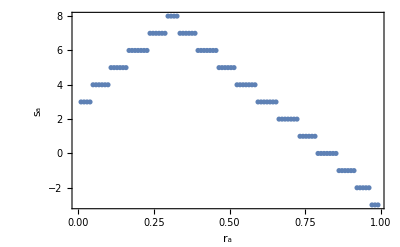

```mathematica
accPoints=Table[
theRatio=radiusRatios[[rIndex]];
testZ=theRatio(theAnnulus[[2]]-theAnnulus[[1]])+theAnnulus[[1]]; 
seriesVal=seriesTable[[-1]]/.z->testZ;
wVals=NSolveValues[$theFunction==0/.z->testZ,w];
difTable=Abs[seriesVal-#]&/@ wVals;
accVal=-MantissaExponent[Min@difTable][[2]];
{theRatio,accVal},
{rIndex,1,Length@radiusRatios}
];
ListPlot[accPoints,AxesLabel->{Style["r_f",12,Bold,Black],Style["s_a",12,Bold,Black]},Frame->{{True,False},{True,False}},FrameLabel->{Style["r_a",12,Bold,Black],Rotate[Style["s_a",12,Bold,Black],-Pi/2]},FrameTicksStyle->Directive[Black,12,Black,Bold]]
```

### Section 12.5: Check accuracy as a function of order and radius ratio

Generate a list plot of accuracy vs. radius ratio using the maximum order of both singular and analytic terms computed above.  This plot should be V-shaped with accuracy increasing as the ratio is increased to a point about midway in the domain, then dropping as the ratio approaches the outer domain boundary

```mathematica
(*
 check accuracy across domain 
*)
theAnnulus//N
thetaRange=Array[#&,100,{-Pi,Pi}];
(* if outer annulus, can try larger domains *)
radiusRange=Array[#&,80,{theAnnulus[[1]],theAnnulus[[2]]}];
radiusRatios=Array[#&,100,{1/100,99/100}];
radiusStart=theAnnulus[[1]];
radiusDif=radiusRange[[-1]]-radiusRange[[1]];
diagFlag=False;
seriesType=1;

theTheta=SetPrecision[thetaRange[[20]],1000];
theTheta=Arg[$theSingularList[[2]]];
theTheta=SetPrecision[Pi/6,1000];
orderStart=20;
orderEnd=theMaxOrder;
plotTable=Table[
If[Mod[radiusIndex,10]==0,
Print["rIndex: ",radiusIndex];
];
 theOrderErrorTable=Table[
theRadius=radiusStart+(radiusRatios[[radiusIndex]] radiusDif);
zVal=SetPrecision[theRadius Exp[I (theTheta)],1000];
(*pVal=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[orderIndex,2]]]])+(Plus@@theReformedSingularTerms[[1;;singularOrderIndexList[[orderIndex,2]]]])/.z->zVal;*)

pVal=seriesTable[[orderIndex]]/.z->zVal;

wVals=w/.NSolve[$theFunction==0/.z->zVal,WorkingPrecision->200];
errTable=Abs[#-pVal]&/@ wVals;
minError=Min@errTable;
If[minError<10^-200,
Print[Style["Error approaching working precision",Red]];
];

pos=Position[errTable,Min[errTable]][[1,1]];
(*{radiusRatios[[n]],errTable[[pos]]//N,-MantissaExponent[errTable[[pos]]][[2]]},*)
{theRadius,orderIndex,-Log[10,errTable[[pos]]]},
{orderIndex,20,theMaxOrder,5}
];

cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
 (* 
   Fit data to upper minimize function
 *)
linearLine=c0+c1 x/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};

functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
(*If[diagFlag,
Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
];
*)

bestUpperFitPlot=Plot[functionList[[bestFitPos]],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
bestUpperFitFunction=functionList[[bestFitPos]];
  (* 
   Fit data to lower minimize function
 *)
cTable=theOrderErrorTable[[All,{2,3}]]//N;
dataVals=cTable;
plotXStart=cTable[[1,1]];
plotXEnd=cTable[[-1,1]];
linearLine=c0+c1 x/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]])])&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(Abs[#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
(*If[diagFlag,
Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
];*)



bestLowerFitPlot=Plot[functionList[[bestFitPos]],{x,orderStart,orderEnd},PlotStyle->{Dashed,Thickness[0.0025],Black}];
bestLowerFitFunction=functionList[[bestFitPos]];


{theRadius,{bestLowerFitFunction,bestUpperFitPlot},{bestUpperFitFunction,bestLowerFitPlot},theOrderErrorTable},
{radiusIndex,1,Length@radiusRatios}
];

(*Show[{plotTable[[All,2]]},PlotRange->{{orderStart,plotXEnd},{0,15}}]
*)
```

{0.954195,1.33333}

rIndex: 10

rIndex: 20

rIndex: 30

rIndex: 40

rIndex: 50

rIndex: 60

rIndex: 70

rIndex: 80

rIndex: 90

rIndex: 100

#### Generate 3D plot of accuracy as function of order and radius ratio

```mathematica
extRadiusTicks[n_]:=radiusRange[[1]]+(radiusRatios[[n]]radiusDif);

 orderGrids=Array[Floor@#&,{5},{orderStart,orderEnd-2}];

pointPlot3D=ListPointPlot3D[Flatten[plotTable[[All,4]],1],BoxRatios->{1, 1, 1},AxesLabel->{Style["r_s",14,Bold,Black],Style["O",14,Bold,Black],Style["s_a",14,Bold,Black]},AxesEdge->{{1,1},{1,1},{-1,1}},FaceGrids->{{{0,0,1},{{extRadiusTicks[20],extRadiusTicks[40],extRadiusTicks[60],extRadiusTicks[80]},orderGrids}}},

Ticks->{{{extRadiusTicks[1],N[extRadiusTicks[1],2]},{extRadiusTicks[20],N[extRadiusTicks[20],2]},{extRadiusTicks[40],N[extRadiusTicks[40],2]},{extRadiusTicks[60],N[extRadiusTicks[60],2]},{extRadiusTicks[80],N[extRadiusTicks[80],2]},{extRadiusTicks[100],N[extRadiusTicks[100],2]}},orderGrids,Automatic},FaceGridsStyle->Directive[Black,Bold],PlotRange->All,PlotStyle->{PointSize[0.005],Black}];
Show[{pointPlot3D},ImageSize->300,ViewPoint->{0.5571611020180107,3.136131872804456,-1.1420369445767034},ViewVertical->{0.04822070754259844,0.280016005056937,-0.9587835002105767}]
```

-Graphics3D-

### Section 12.6: Generate series plots and compare to differential plots

The series plot, with a reasonable number of terms, 25-50 or more if needed, should look identical to the differential plot and should overlay neatly over the differential plot when plotted together.

```mathematica
(*
 retrieve reduced precise series from file
*)
If[FileExistsQ[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]],
Print["Importing combined high precision terms to ",combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
{reducedPreciseAnalyticTerms,reducedPreciseAnalyticOrderList,reducedPreciseSingularTerms,reducedPreciseSingularOrderList}=Import[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];

singularMaxOrder=reducedPreciseSingularOrderList[[-1,1]];
analyticMaxOrder=reducedPreciseAnalyticOrderList[[-1,1]];
theMaxOrder=Min[{analyticMaxOrder,singularMaxOrder}];
Print["theMaxOrder: ",theMaxOrder];
,
Print[Style[combinedExpansionTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]<>" not found during import.",Red]];
];
```

Importing combined high precision terms to D:\algFunctionBook\data\testCase0017\a4b132combinedExpansionTerms.m

theMaxOrder: 99

```mathematica
(* 
 generate series plot with orderIndex terms
*)
orderIndex=25;

branchColors={Red,Blue,Green,Yellow,Orange,Purple,Brown,Magenta,Pink};
(*
 use plotting dimension from differential plot
*)

plotDomain=plottingRadiiTable[[$selectedAnnulus]];
rMin=plotDomain[[1]]//N
rMax=plotDomain[[-1]]//N

truncatedSeries[z_]:=(Plus@@reducedPreciseAnalyticTerms[[1;;reducedPreciseAnalyticOrderList[[orderIndex,2]]]])+(Plus@@reducedPreciseSingularTerms[[1;;reducedPreciseSingularOrderList[[orderIndex,2]]]]);


 theexp=Exponent[truncatedSeries[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[truncatedSeries[z],z,theexp];
branchSheetF[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/$selectedBranchSize])^($selectedBranchSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];

 (*imagSeriesPlots=Table[
ParametricPlot3D[{Re@z,Im@z,Im@branchSheetF[z,sheetIndex]}/.z->r Exp[I t],{r,rMin,rMax},{t,-Pi,Pi},PlotStyle->branchColors[[sheetIndex+1]],BoxRatios->{1, 1, 2},PlotRange->PlotRange[theDifferentialBranchPlot]],
{sheetIndex,0,$selectedBranchSize-1}
];

*)
 realSeriesPlots=Table[
ParametricPlot3D[{Re@z,Im@z,Re@branchSheetF[z,sheetIndex]}/.z->r Exp[I t],{r,rMin,rMax},{t,-Pi,Pi},PlotStyle->branchColors[[sheetIndex+1]],BoxRatios->{1, 1, 1},PlotRange->PlotRange[realDifferentialBranchPlot]],
{sheetIndex,0,$selectedBranchSize-1}
];
```

0.957355

1.33017

```mathematica
(*
 compare series plot to differential plot
*)
Row[{Show[realDifferentialBranchPlot,ImageSize->300],Show[realSeriesPlots,ImageSize->300]}]
(* 
 good visual check if power expansion is correct if the series plot superimposes nicely over the differential plot
*)
 Show[{realDifferentialBranchPlot,realSeriesPlots},ImageSize->300]
```

-Graphics3D--Graphics3D-

-Graphics3D-

### Section 12.7: Plot branch when singular and analytic arrays are unequal (usually for outermost annulus)

```mathematica
analyticOrderIndexList[[-1]]
singularOrderIndexList[[-1]]
reducedAnalyticTerms[[analyticOrderIndexList[[30,2]]]]//N
reducedSingularTerms[[singularOrderIndexList[[30,2]]]]//N
```

{33,100}

{33,67}

-0.000156259 z^30

-(3.6653×10^-9)/z^(89/3)

```mathematica
singularOrderIndexList
```

{{1,4},{2,8},{3,12},{4,16},{5,20},{6,24},{7,28},{8,32},{9,36},{10,40},{11,44},{12,48},{13,52},{14,56},{15,60},{16,64},{17,68},{18,72},{19,76},{20,80},{21,84},{22,88},{23,92},{24,96},{25,100}}

```mathematica
branchColors={Red,Blue,Green,Yellow,Orange,Purple,Brown,Magenta,Pink};

radiusRange=Array[#&,40,theAnnulus];
plotMin=-theAnnulus[[2]];
plotMax=theAnnulus[[2]];

orderIndex=50;
(*truncatedSeries[z_]:=(Plus@@reducedAnalyticTerms[[1;;analyticOrderIndexList[[orderIndex,2]]]])+(Plus@@reducedSingularTerms[[1;;singularOrderIndexList[[orderIndex,2]]]]);
*)
truncatedSeries[z_]:=a0Coef+(Plus@@reducedSingularTerms[[1;;singularOrderIndexList[[orderIndex,2]]]]);


 theexp=Exponent[truncatedSeries[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[truncatedSeries[z],z,theexp];
branchSheetF[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/$selectedBranchSize])^($selectedBranchSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];


 realSeriesPlots=Table[
ParametricPlot3D[{Re@z,Im@z,Re@branchSheetF[z,sheetIndex]}/.z->r Exp[I t],{r,rMin,rMax},{t,-Pi,Pi},PlotStyle->{Opacity[0.5],branchColors[[sheetIndex+1]]},BoxRatios->{1, 1, 2},PlotRange->PlotRange[realDifferentialBranchPlot]],
{sheetIndex,0,$selectedBranchSize-1}
];
```

Part::partw: Part 50 of {{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},«39»} does not exist.

Part::span: 1;;{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},«39»}⟦50,2⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 50 of {{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},«39»} does not exist.

Part::span: 1;;{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},«39»}⟦50,2⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 50 of {{1.,1.},{2.,2.},{3.,3.},{4.,4.},{5.,5.},{6.,6.},{7.,7.},{8.,8.},{9.,9.},{10.,10.},«39»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Show[realDifferentialBranchPlot,PlotRange->All,BoxRatios->{1, 1, 1},ImageSize->300]
Show[realSeriesPlots,PlotRange->All,ImageSize->300,BoxRatios->{1, 1, 1}]
```

-Graphics3D- -Graphics3D-

## Section 13: Using polishMedial to compute high-precision multi-medial analytic terms

### Section 13.1: Create low-precision medial contour

```mathematica
(*
 set up low precision medial contour
*)

 rationalRNorm=Rationalize[rNorm,10^-25];

at=AbsoluteTiming[{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$selectedAnnulus,$selectedMonodromyIndex,25,1/2];];
Print["total time: ",at[[1]]];
```

Setting rNorm: 2.20209

tStart: 0.523599

tEnd: 6.80678

medialSol: 0.0401945-0.458088 ⅈ

total time: 11.2127

### Section 13.2: Define number of runs, precision and number of terms

```mathematica
(*
 define number of runs and precision
*)

    segmentMenu=Labeled[Column[{Row[{Style["Integration partitions: ",Black,Bold],RadioButtonBar[Dynamic[$integrationPartition],{1,2,3}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Spacer[20],Style["Start index: "],Spacer[10],InputField[Dynamic@$analTermMin,FieldSize->4]}],
Row[{Spacer[20],Style["End index: "],Spacer[24],InputField[Dynamic@$analTermMax,FieldSize->4]}],
Row[{Spacer[20],Style["Precision array: "],Spacer[24],InputField[Dynamic@$analyticPrecisionArray,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["Multi-medial analytic Menu",Bold,Black],Top]
```

Integration partitions:  | 1   | 2   | 3
Show plot label 
Start index: 
End index: 
Precision array: Multi-medial analytic Menu

### Section 13.3: Compute high-precision terms with polishMedial

```mathematica
(*
 define high precision arrays
*)
precisionArray=$analyticPrecisionArray;
totalMedialRuns=Length@precisionArray;



 startTime=TimeObject[Now];
DistributeDefinitions[$integrationPartition,$analTermMin,$analTermMax,$selectedBranchSize];

Print[Style["Analyzing annulus "<>ToString@$selectedAnnulus<>" branch "<>ToString@$selectedBranch,12]];
t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$integrationPartition+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
Print["Partitioning integration as: ",thePartitions];

at2=AbsoluteTiming[
residualAnalyticTerms=ParallelTable[

theCycleSize=$selectedBranchSize;
Print["Computing terms at medial precision ",medialPrecision];

analTable=Table[
If[Mod[k,25]==0,
Print["Current index ",k];
];


If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],medialPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->medialPrecision,AccuracyGoal->medialPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],medialPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->medialPrecision,AccuracyGoal->medialPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,$analTermMin,$analTermMax}
];
{medialPrecision,analTable},
{medialPrecision,precisionArray}
];
];
endTime=TimeObject[Now]
Print["Time to compute multi-medial analytic contours: ",endTime-startTime]
```

Analyzing annulus 5 branch {3}

Partitioning integration as: {{π/6,(13 π)/6}}

Computing terms at medial precision 75

Computing terms at medial precision 100

Current index 0

Current index 0

Current index 25

Current index 25

Current index 50

Current index 50

16:32:52GMT-5TimeObject[{16,32,52.8277275},Instant,-5.]

Time to compute multi-medial analytic contours: 2.35511 min

### Section 13.4: Generate grid report

```mathematica
plotLabel=Column[{Row[{Style[$theTestCase]," analytic terms"}],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];



analyticData=Table[
If[iVal==1,
{residualAnalyticTerms[[1,2,All,1]],residualAnalyticTerms[[1,2,All,-2]]}
,
residualAnalyticTerms[[iVal,2,All,-2]]
]
,
{iVal,1,Length@residualAnalyticTerms}
];

errorReport=MapThread[List,FlattenAt[analyticData,1]];

errorReportR=MapThread[List,FlattenAt[analyticData,1]];

theHeading=Flatten@{"exp",#1&/@ precisionArray[[Range[Length@residualAnalyticTerms]]]};

(*theDisplay=Style[Grid[Prepend[Join[errorReport[[1;;7]],errorReportR[[-8;;]]],theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];
*)
theDisplay=Style[Grid[Prepend[errorReport,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];


Print[Column[{If[$showPlotLabel,plotLabel,""],theDisplay},Alignment->Center]]
```

exp | 75 | 100
0 | -0.08888842174+0. ⅈ | -0.08888842174+0. ⅈ
1 | 0.007226419726+0. ⅈ | 0.007226419726+0. ⅈ
2 | -0.0005302354473+0. ⅈ | -0.0005302354473+0. ⅈ
3 | 0.00003104792331+0. ⅈ | 0.00003104792331+0. ⅈ
4 | -9.876975638×10^-7+0. ⅈ | -9.876975638×10^-7+0. ⅈ
5 | -6.382344682×10^-8+0. ⅈ | -6.382344682×10^-8+0. ⅈ
6 | 1.482315143×10^-8+0. ⅈ | 1.482315143×10^-8+0. ⅈ
7 | -1.484590146×10^-9+0. ⅈ | -1.484590146×10^-9+0. ⅈ
8 | 8.396902575×10^-11+0. ⅈ | 8.396902575×10^-11+0. ⅈ
9 | 7.346231918×10^-13+0. ⅈ | 7.346231918×10^-13+0. ⅈ
10 | -8.313605549×10^-13+0. ⅈ | -8.313605549×10^-13+0. ⅈ
11 | 1.122633378×10^-13+0. ⅈ | 1.122633378×10^-13+0. ⅈ
12 | -8.60277879×10^-15+0. ⅈ | -8.60277879×10^-15+0. ⅈ
13 | 2.0338815×10^-16+0. ⅈ | 2.0338815×10^-16+0. ⅈ
14 | 5.219819153×10^-17+0. ⅈ | 5.219819153×10^-17+0. ⅈ
15 | -9.710972656×10^-18+0. ⅈ | -9.710972656×10^-18+0. ⅈ
16 | 9.355019908×10^-19+0. ⅈ | 9.355019908×10^-19+0. ⅈ
17 | -4.370844007×10^-20+0. ⅈ | -4.370844007×10^-20+0. ⅈ
18 | -2.81837033×10^-21+0. ⅈ | -2.81837033×10^-21+0. ⅈ
19 | 8.704145658×10^-22+0. ⅈ | 8.704145658×10^-22+0. ⅈ
20 | -1.034591251×10^-22+0. ⅈ | -1.034591251×10^-22+0. ⅈ
21 | 6.804435949×10^-24+0. ⅈ | 6.804435949×10^-24+0. ⅈ
22 | 3.318494546×10^-26+0. ⅈ | 3.318494546×10^-26+0. ⅈ
23 | -7.621531556×10^-26+0. ⅈ | -7.621531556×10^-26+0. ⅈ
24 | 1.138241392×10^-26+0. ⅈ | 1.138241392×10^-26+0. ⅈ
25 | -9.509621732×10^-28+0. ⅈ | -9.509621732×10^-28+0. ⅈ
26 | 2.620675765×10^-29+0. ⅈ | 2.620675765×10^-29+0. ⅈ
27 | 6.082034903×10^-30+0. ⅈ | 6.082034903×10^-30+0. ⅈ
28 | -1.225275464×10^-30+0. ⅈ | -1.225275464×10^-30+0. ⅈ
29 | 1.252418361×10^-31+0. ⅈ | 1.252418361×10^-31+0. ⅈ
30 | -6.297278966×10^-33+0. ⅈ | -6.297278966×10^-33+0. ⅈ
31 | -3.730530424×10^-34+0. ⅈ | -3.730530424×10^-34+0. ⅈ
32 | 1.267281738×10^-34+0. ⅈ | 1.267281738×10^-34+0. ⅈ
33 | -1.577760093×10^-35+0. ⅈ | -1.577760093×10^-35+0. ⅈ
34 | 1.089138676×10^-36+0. ⅈ | 1.089138676×10^-36+0. ⅈ
35 | 1.846108329×10^-39+0. ⅈ | 1.846108329×10^-39+0. ⅈ
36 | -1.224917438×10^-38+0. ⅈ | -1.224917438×10^-38+0. ⅈ
37 | 1.906976306×10^-39+0. ⅈ | 1.906976306×10^-39+0. ⅈ
38 | -1.652545787×10^-40+0. ⅈ | -1.652545787×10^-40+0. ⅈ
39 | 4.977043447×10^-42+0. ⅈ | 4.977043447×10^-42+0. ⅈ
40 | 1.044757958×10^-42+0. ⅈ | 1.044757958×10^-42+0. ⅈ
41 | -2.202604343×10^-43+0. ⅈ | -2.202604343×10^-43+0. ⅈ
42 | 2.320997012×10^-44+0. ⅈ | 2.320997012×10^-44+0. ⅈ
43 | -1.219963297×10^-45+0. ⅈ | -1.219963297×10^-45+0. ⅈ
44 | -6.567586879×10^-47+0. ⅈ | -6.567586879×10^-47+0. ⅈ
45 | 2.40360558×10^-47+0. ⅈ | 2.40360558×10^-47+0. ⅈ
46 | -3.077226453×10^-48+0. ⅈ | -3.077226453×10^-48+0. ⅈ
47 | 2.190842082×10^-49+0. ⅈ | 2.190842082×10^-49+0. ⅈ
48 | -2.704482876×10^-52+0. ⅈ | -2.704482876×10^-52+0. ⅈ
49 | -2.418056207×10^-51+0. ⅈ | -2.418056207×10^-51+0. ⅈ
50 | 3.875316×10^-52+0. ⅈ | 3.875316×10^-52+0. ⅈ

### Section 13.5 Identify residual analytic terms and create reducedAnalCoefList

#### Create reducedAnalCoefList

```mathematica
(*
 second version
*)
 pureData=MapThread[List,ReIm@residualAnalyticTerms[[All,2,All,2]]];
Print["Precision of highest precision pureData: ",Precision@pureData[[All,-1]]];
pureExp=residualAnalyticTerms[[1,2,All,1]];
reducedFlag1=False;
imagZeroIndexes=0;
realZeroIndexes=0;
analyticCodeArray={};
reducedAnalCoefList=Table[
newDataList={};
coeffCode={0,0};
testRun=pureData[[iVal]];
realTrend=-MantissaExponent[Abs[testRun[[All,1]]//N]][[-2;;,2]];
imagTrend=-MantissaExponent[Abs[testRun[[All,2]]//N]][[-2;;,2]];
If[Differences@realTrend=={0},
AppendTo[newDataList,testRun[[-1,1]]];
coeffCode[[1]]=1;
,
realZeroIndexes++;
If[reducedFlag1,
Print[Style["real has differences",Red]];
];
];
If[Differences@imagTrend=={0},
AppendTo[newDataList,I testRun[[-1,2]]];
coeffCode[[2]]=1;
,
imagZeroIndexes++;
If[reducedFlag1,
Print[Style["imag has differences",Red]];

];
];
(*
 now update value of coef
*)
If[Length@newDataList==1,
newValue=newDataList[[1]];
,
If[Length@newDataList==2,
newValue=Plus@@newDataList;
,
newValue=0;
];
];
AppendTo[analyticCodeArray,{pureExp[[iVal]] $selectedBranchSize,pureExp[[iVal]],coeffCode}];
{pureExp[[iVal]],newValue z^pureExp[[iVal]]},
{iVal,1,Length@pureData}
];
(*Print["reducedAnalCoefList: ",reducedAnalCoefList//N];
*)

If[imagZeroIndexes==Length@pureData,
Print["Imag parts of all terms are zero!"];
,
If[imagZeroIndexes!=0,
Print[Style["Some real parts are zero but not all !,Red"]];
];
];
If[realZeroIndexes==Length@pureData,
Print["Real parts of all terms are zero!"];
,
If[realZeroIndexes!=0,
Print[Style["Some real parts are zero but not all !,Red"]];
];
]; 
Print["imagZeroIndexes: ",imagZeroIndexes];
Print["realZeroIndexes: ",realZeroIndexes];
reducedList={#[[1]],N[#[[2]]]}&/@reducedAnalCoefList[[1;;15]];
Grid[Prepend[reducedList,{"exp","Term"}],Dividers->{{{True}},{True,True,{False},True}}]
Print["Precision of reducedAnalCoefList: ",Precision@reducedAnalCoefList[[2]]];
```

Precision of highest precision pureData: 100.

Imag parts of all terms are zero!

imagZeroIndexes: 51

realZeroIndexes: 0

exp | Term
0 | -0.0888884
1 | 0.00722642 z
2 | -0.000530235 z^2
3 | 0.0000310479 z^3
4 | -9.87698×10^-7 z^4
5 | -6.38234×10^-8 z^5
6 | 1.48232×10^-8 z^6
7 | -1.48459×10^-9 z^7
8 | 8.3969×10^-11 z^8
9 | 7.34623×10^-13 z^9
10 | -8.31361×10^-13 z^10
11 | 1.12263×10^-13 z^11
12 | -8.60278×10^-15 z^12
13 | 2.03388×10^-16 z^13
14 | 5.21982×10^-17 z^14

Precision of reducedAnalCoefList: 100.

### Section 13.6: Generate grid report with residual terms set to zero

```mathematica
(*
  now update grid with reduced terms
*)

analData=Table[
If[iVal==1,
{residualAnalyticTerms[[1,2,All,1]],residualAnalyticTerms[[1,2,All,2]]//N}
,
residualAnalyticTerms[[iVal,2,All,2]]//N]
,
{iVal,1,totalMedialRuns}
];
(*
 now append reduced terms to data
*)
Print["test"];

analErrorReport=MapThread[List,FlattenAt[analData,1]];
updatedAnalyticData=MapThread[Append[#1,#2]&,{analErrorReport,reducedAnalCoefList[[All,2]]}];
updatedAnalyticDataR=MapThread[Append[#1,#2]&,{analErrorReport,reducedAnalCoefList[[All,2]]//N}];

theHeading=Flatten@{"exp",#1&/@ precisionArray[[Range[totalMedialRuns]]]}
AppendTo[theHeading,"reformed Vals"];

theDisplay=Style[Grid[Prepend[updatedAnalyticDataR//N,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];


Print["Precision of reduced terms: ",Precision@updatedAnalyticData[[All,-1]]];
Print[Column[{If[$showPlotLabel,plotLabel,""],theDisplay},Alignment->Center]];


reducedAnalyticSeries[z_]=Plus@@updatedAnalyticData[[All,-1]];

Print["Precision of reducedAnalyticSeries[z]:",Precision@reducedAnalyticSeries[z]]
```

test

{exp,75,100}

Precision of reduced terms: 100.

exp | 75 | 100 | reformed Vals
0. | -0.0888884+4.11646×10^-63 ⅈ | -0.0888884-1.17351×10^-82 ⅈ | -0.0888884
1. | 0.00722642+2.67265×10^-63 ⅈ | 0.00722642+6.27295×10^-83 ⅈ | 0.00722642 z
2. | -0.000530235+2.0845×10^-63 ⅈ | -0.000530235-3.35283×10^-83 ⅈ | -0.000530235 z^2
3. | 0.0000310479+6.28665×10^-64 ⅈ | 0.0000310479+1.79232×10^-83 ⅈ | 0.0000310479 z^3
4. | -9.87698×10^-7+5.09408×10^-64 ⅈ | -9.87698×10^-7-9.57926×10^-84 ⅈ | -9.87698×10^-7 z^4
5. | -6.38234×10^-8-1.03157×10^-65 ⅈ | -6.38234×10^-8+5.12117×10^-84 ⅈ | -6.38234×10^-8 z^5
6. | 1.48232×10^-8+5.51731×10^-66 ⅈ | 1.48232×10^-8-2.73677×10^-84 ⅈ | 1.48232×10^-8 z^6
7. | -1.48459×10^-9-2.9462×10^-66 ⅈ | -1.48459×10^-9+1.46332×10^-84 ⅈ | -1.48459×10^-9 z^7
8. | 8.3969×10^-11+1.57668×10^-66 ⅈ | 8.3969×10^-11-7.81845×10^-85 ⅈ | 8.3969×10^-11 z^8
9. | 7.34623×10^-13-8.41259×10^-67 ⅈ | 7.34623×10^-13+1.42761×10^-88 ⅈ | 7.34623×10^-13 z^9
10. | -8.31361×10^-13+4.50698×10^-67 ⅈ | -8.31361×10^-13+1.05418×10^-88 ⅈ | -8.31361×10^-13 z^10
11. | 1.12263×10^-13-2.40116×10^-67 ⅈ | 1.12263×10^-13+7.78462×10^-89 ⅈ | 1.12263×10^-13 z^11
12. | -8.60278×10^-15+1.28902×10^-67 ⅈ | -8.60278×10^-15+5.74846×10^-89 ⅈ | -8.60278×10^-15 z^12
13. | 2.03388×10^-16-6.84832×10^-68 ⅈ | 2.03388×10^-16+4.24498×10^-89 ⅈ | 2.03388×10^-16 z^13
14. | 5.21982×10^-17+3.69034×10^-68 ⅈ | 5.21982×10^-17+3.13469×10^-89 ⅈ | 5.21982×10^-17 z^14
15. | -9.71097×10^-18+1.26438×10^-70 ⅈ | -9.71097×10^-18+2.31483×10^-89 ⅈ | -9.71097×10^-18 z^15
16. | 9.35502×10^-19+9.21428×10^-71 ⅈ | 9.35502×10^-19+1.70939×10^-89 ⅈ | 9.35502×10^-19 z^16
17. | -4.37084×10^-20+6.70895×10^-71 ⅈ | -4.37084×10^-20+1.26231×10^-89 ⅈ | -4.37084×10^-20 z^17
18. | -2.81837×10^-21+4.88375×10^-71 ⅈ | -2.81837×10^-21+9.3216×10^-90 ⅈ | -2.81837×10^-21 z^18
19. | 8.70415×10^-22+3.55238×10^-71 ⅈ | 8.70415×10^-22+6.88357×10^-90 ⅈ | 8.70415×10^-22 z^19
20. | -1.03459×10^-22+2.58287×10^-71 ⅈ | -1.03459×10^-22+5.08318×10^-90 ⅈ | -1.03459×10^-22 z^20
21. | 6.80444×10^-24-2.69569×10^-75 ⅈ | 6.80444×10^-24+3.15416×10^-96 ⅈ | 6.80444×10^-24 z^21
22. | 3.31849×10^-26-1.46724×10^-75 ⅈ | 3.31849×10^-26+1.29218×10^-96 ⅈ | 3.31849×10^-26 z^22
23. | -7.62153×10^-26-1.3421×10^-75 ⅈ | -7.62153×10^-26+1.59963×10^-96 ⅈ | -7.62153×10^-26 z^23
24. | 1.13824×10^-26-8.36699×10^-76 ⅈ | 1.13824×10^-26+9.05385×10^-97 ⅈ | 1.13824×10^-26 z^24
25. | -9.50962×10^-28-6.88063×10^-76 ⅈ | -9.50962×10^-28+8.66917×10^-97 ⅈ | -9.50962×10^-28 z^25
26. | 2.62068×10^-29-4.61183×10^-76 ⅈ | 2.62068×10^-29+5.71977×10^-97 ⅈ | 2.62068×10^-29 z^26
27. | 6.08203×10^-30-3.58477×10^-76 ⅈ | 6.08203×10^-30+4.86932×10^-97 ⅈ | 6.08203×10^-30 z^27
28. | -1.22528×10^-30-2.49681×10^-76 ⅈ | -1.22528×10^-30+3.45949×10^-97 ⅈ | -1.22528×10^-30 z^28
29. | 1.25242×10^-31-1.88254×10^-76 ⅈ | 1.25242×10^-31+2.7826×10^-97 ⅈ | 1.25242×10^-31 z^29
30. | -6.29728×10^-33-1.33775×10^-76 ⅈ | -6.29728×10^-33+2.04818×10^-97 ⅈ | -6.29728×10^-33 z^30
31. | -3.73053×10^-34-9.91742×10^-77 ⅈ | -3.73053×10^-34+1.60158×10^-97 ⅈ | -3.73053×10^-34 z^31
32. | 1.26728×10^-34-7.11905×10^-77 ⅈ | 1.26728×10^-34+1.19857×10^-97 ⅈ | 1.26728×10^-34 z^32
33. | -1.57776×10^-35-2.16696×10^-79 ⅈ | -1.57776×10^-35+9.23741×10^-98 ⅈ | -1.57776×10^-35 z^33
34. | 1.08914×10^-36+1.15829×10^-79 ⅈ | 1.08914×10^-36+6.96464×10^-98 ⅈ | 1.08914×10^-36 z^34
35. | 1.84611×10^-39-6.18242×10^-80 ⅈ | 1.84611×10^-39+5.32605×10^-98 ⅈ | 1.84611×10^-39 z^35
36. | -1.22492×10^-38+3.30464×10^-80 ⅈ | -1.22492×10^-38+4.02776×10^-98 ⅈ | -1.22492×10^-38 z^36
37. | 1.90698×10^-39-1.76641×10^-80 ⅈ | 1.90698×10^-39+3.06645×10^-98 ⅈ | 1.90698×10^-39 z^37
38. | -1.65255×10^-40+9.44184×10^-81 ⅈ | -1.65255×10^-40-2.06026×10^-101 ⅈ | -1.65255×10^-40 z^38
39. | 4.97704×10^-42-5.04688×10^-81 ⅈ | 4.97704×10^-42+1.10125×10^-101 ⅈ | 4.97704×10^-42 z^39
40. | 1.04476×10^-42+2.69767×10^-81 ⅈ | 1.04476×10^-42-5.88645×10^-102 ⅈ | 1.04476×10^-42 z^40
41. | -2.2026×10^-43-1.44196×10^-81 ⅈ | -2.2026×10^-43+3.14644×10^-102 ⅈ | -2.2026×10^-43 z^41
42. | 2.321×10^-44+7.70763×10^-82 ⅈ | 2.321×10^-44-1.68185×10^-102 ⅈ | 2.321×10^-44 z^42
43. | -1.21996×10^-45-4.1199×10^-82 ⅈ | -1.21996×10^-45+8.98985×10^-103 ⅈ | -1.21996×10^-45 z^43
44. | -6.56759×10^-47+2.20218×10^-82 ⅈ | -6.56759×10^-47-4.80528×10^-103 ⅈ | -6.56759×10^-47 z^44
45. | 2.40361×10^-47-1.17711×10^-82 ⅈ | 2.40361×10^-47+2.5688×10^-103 ⅈ | 2.40361×10^-47 z^45
46. | -3.07723×10^-48+6.29194×10^-83 ⅈ | -3.07723×10^-48-1.37308×10^-103 ⅈ | -3.07723×10^-48 z^46
47. | 2.19084×10^-49-3.36318×10^-83 ⅈ | 2.19084×10^-49+7.33943×10^-104 ⅈ | 2.19084×10^-49 z^47
48. | -2.70448×10^-52+1.7977×10^-83 ⅈ | -2.70448×10^-52-3.92309×10^-104 ⅈ | -2.70448×10^-52 z^48
49. | -2.41806×10^-51-9.6091×10^-84 ⅈ | -2.41806×10^-51+2.09698×10^-104 ⅈ | -2.41806×10^-51 z^49
50. | 3.87532×10^-52+5.13628×10^-84 ⅈ | 3.87532×10^-52-1.12088×10^-104 ⅈ | 3.87532×10^-52 z^50

Precision of reducedAnalyticSeries[z]:100.

### Section 13.7: Create: reducedAnalyticTerms, analyticResidueArray, analyticSequenceFunction, analyticOrderIndexList

```mathematica
(*
  create final reduced analytic terms minus the residuals
*)
Print["analTermMax: ",$analTermMax];

reducedAnalyticTerms=DeleteCases[updatedAnalyticData[[All,-1]],0];

(*
 create reducedAnalyticCodeArray
*)

reducedAnalyticCodeArray= Cases[analyticCodeArray,{x_,y_,z_}/;z!={0,0}];
analyticResidueArray=reducedAnalyticCodeArray;
Print["analyticResidueArray: ",analyticResidueArray];

(*
 create sequence funtion (not used presently, set to zero )
*)
(*analyticSequenceFunction=FindSequenceFunction[reducedAnalyticCodeArray[[All,2]] $selectedBranchSize]*)
analyticSequenceFunction=0;

 (*
 use raw analytic terms of highest precision
*)
(*reducedAnalyticTerms=residualAnalyticTerms[[All,3]];*)
Precision@reducedAnalyticTerms

deleteLen=Length@reducedAnalyticTerms
If[deleteLen>0,
theExps=Exponent[#,z]&/@ reducedAnalyticTerms;
maxExp=Floor@Max@theExps;
nearElements=Nearest[theExps,Range[maxExp],2];

uniqueVals=nearElements[[All,1]];

newOrderList=(Position[theExps,x_/;x==#]&/@uniqueVals)//Flatten;
analyticOrderIndexList=MapThread[{#1,#2}&,{Range[maxExp],newOrderList}];
Print["analyticOrderIndexList {order,index}: ",analyticOrderIndexList];
,
analyticOrderIndexList={};
Print[Style["All analytic terms are zero!",Red]];
];
Print["Highest order analytic term: ",analyticOrderIndexList[[-1]]];
Print["Precision of deleted analytic terms: ",Precision@reducedAnalyticTerms];
Print["Last five terms: ",reducedAnalyticTerms[[-5]]];
```

analTermMax: 50

analyticResidueArray: {{0,0,{1,0}},{1,1,{1,0}},{2,2,{1,0}},{3,3,{1,0}},{4,4,{1,0}},{5,5,{1,0}},{6,6,{1,0}},{7,7,{1,0}},{8,8,{1,0}},{9,9,{1,0}},{10,10,{1,0}},{11,11,{1,0}},{12,12,{1,0}},{13,13,{1,0}},{14,14,{1,0}},{15,15,{1,0}},{16,16,{1,0}},{17,17,{1,0}},{18,18,{1,0}},{19,19,{1,0}},{20,20,{1,0}},{21,21,{1,0}},{22,22,{1,0}},{23,23,{1,0}},{24,24,{1,0}},{25,25,{1,0}},{26,26,{1,0}},{27,27,{1,0}},{28,28,{1,0}},{29,29,{1,0}},{30,30,{1,0}},{31,31,{1,0}},{32,32,{1,0}},{33,33,{1,0}},{34,34,{1,0}},{35,35,{1,0}},{36,36,{1,0}},{37,37,{1,0}},{38,38,{1,0}},{39,39,{1,0}},{40,40,{1,0}},{41,41,{1,0}},{42,42,{1,0}},{43,43,{1,0}},{44,44,{1,0}},{45,45,{1,0}},{46,46,{1,0}},{47,47,{1,0}},{48,48,{1,0}},{49,49,{1,0}},{50,50,{1,0}}}

100.

51

analyticOrderIndexList {order,index}: {{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{22,23},{23,24},{24,25},{25,26},{26,27},{27,28},{28,29},{29,30},{30,31},{31,32},{32,33},{33,34},{34,35},{35,36},{36,37},{37,38},{38,39},{39,40},{40,41},{41,42},{42,43},{43,44},{44,45},{45,46},{46,47},{47,48},{48,49},{49,50},{50,51}}

Highest order analytic term: {50,51}

Precision of deleted analytic terms: 100.

Last five terms: -3.077226452808228765077236075538686207129587462135304145238577290575993415208484944000643050607431151×10^-48 z^46

### Section 13.8: Set up analyticResidueArray for high-precision analysis (edit as necessary)

```mathematica
analyticResidueArray=Table[{n,n,{1,0}},{n,0,200}]
```

{{0,0,{1,0}},{1,1,{1,0}},{2,2,{1,0}},{3,3,{1,0}},{4,4,{1,0}},{5,5,{1,0}},{6,6,{1,0}},{7,7,{1,0}},{8,8,{1,0}},{9,9,{1,0}},{10,10,{1,0}},{11,11,{1,0}},{12,12,{1,0}},{13,13,{1,0}},{14,14,{1,0}},{15,15,{1,0}},{16,16,{1,0}},{17,17,{1,0}},{18,18,{1,0}},{19,19,{1,0}},{20,20,{1,0}},{21,21,{1,0}},{22,22,{1,0}},{23,23,{1,0}},{24,24,{1,0}},{25,25,{1,0}},{26,26,{1,0}},{27,27,{1,0}},{28,28,{1,0}},{29,29,{1,0}},{30,30,{1,0}},{31,31,{1,0}},{32,32,{1,0}},{33,33,{1,0}},{34,34,{1,0}},{35,35,{1,0}},{36,36,{1,0}},{37,37,{1,0}},{38,38,{1,0}},{39,39,{1,0}},{40,40,{1,0}},{41,41,{1,0}},{42,42,{1,0}},{43,43,{1,0}},{44,44,{1,0}},{45,45,{1,0}},{46,46,{1,0}},{47,47,{1,0}},{48,48,{1,0}},{49,49,{1,0}},{50,50,{1,0}},{51,51,{1,0}},{52,52,{1,0}},{53,53,{1,0}},{54,54,{1,0}},{55,55,{1,0}},{56,56,{1,0}},{57,57,{1,0}},{58,58,{1,0}},{59,59,{1,0}},{60,60,{1,0}},{61,61,{1,0}},{62,62,{1,0}},{63,63,{1,0}},{64,64,{1,0}},{65,65,{1,0}},{66,66,{1,0}},{67,67,{1,0}},{68,68,{1,0}},{69,69,{1,0}},{70,70,{1,0}},{71,71,{1,0}},{72,72,{1,0}},{73,73,{1,0}},{74,74,{1,0}},{75,75,{1,0}},{76,76,{1,0}},{77,77,{1,0}},{78,78,{1,0}},{79,79,{1,0}},{80,80,{1,0}},{81,81,{1,0}},{82,82,{1,0}},{83,83,{1,0}},{84,84,{1,0}},{85,85,{1,0}},{86,86,{1,0}},{87,87,{1,0}},{88,88,{1,0}},{89,89,{1,0}},{90,90,{1,0}},{91,91,{1,0}},{92,92,{1,0}},{93,93,{1,0}},{94,94,{1,0}},{95,95,{1,0}},{96,96,{1,0}},{97,97,{1,0}},{98,98,{1,0}},{99,99,{1,0}},{100,100,{1,0}},{101,101,{1,0}},{102,102,{1,0}},{103,103,{1,0}},{104,104,{1,0}},{105,105,{1,0}},{106,106,{1,0}},{107,107,{1,0}},{108,108,{1,0}},{109,109,{1,0}},{110,110,{1,0}},{111,111,{1,0}},{112,112,{1,0}},{113,113,{1,0}},{114,114,{1,0}},{115,115,{1,0}},{116,116,{1,0}},{117,117,{1,0}},{118,118,{1,0}},{119,119,{1,0}},{120,120,{1,0}},{121,121,{1,0}},{122,122,{1,0}},{123,123,{1,0}},{124,124,{1,0}},{125,125,{1,0}},{126,126,{1,0}},{127,127,{1,0}},{128,128,{1,0}},{129,129,{1,0}},{130,130,{1,0}},{131,131,{1,0}},{132,132,{1,0}},{133,133,{1,0}},{134,134,{1,0}},{135,135,{1,0}},{136,136,{1,0}},{137,137,{1,0}},{138,138,{1,0}},{139,139,{1,0}},{140,140,{1,0}},{141,141,{1,0}},{142,142,{1,0}},{143,143,{1,0}},{144,144,{1,0}},{145,145,{1,0}},{146,146,{1,0}},{147,147,{1,0}},{148,148,{1,0}},{149,149,{1,0}},{150,150,{1,0}},{151,151,{1,0}},{152,152,{1,0}},{153,153,{1,0}},{154,154,{1,0}},{155,155,{1,0}},{156,156,{1,0}},{157,157,{1,0}},{158,158,{1,0}},{159,159,{1,0}},{160,160,{1,0}},{161,161,{1,0}},{162,162,{1,0}},{163,163,{1,0}},{164,164,{1,0}},{165,165,{1,0}},{166,166,{1,0}},{167,167,{1,0}},{168,168,{1,0}},{169,169,{1,0}},{170,170,{1,0}},{171,171,{1,0}},{172,172,{1,0}},{173,173,{1,0}},{174,174,{1,0}},{175,175,{1,0}},{176,176,{1,0}},{177,177,{1,0}},{178,178,{1,0}},{179,179,{1,0}},{180,180,{1,0}},{181,181,{1,0}},{182,182,{1,0}},{183,183,{1,0}},{184,184,{1,0}},{185,185,{1,0}},{186,186,{1,0}},{187,187,{1,0}},{188,188,{1,0}},{189,189,{1,0}},{190,190,{1,0}},{191,191,{1,0}},{192,192,{1,0}},{193,193,{1,0}},{194,194,{1,0}},{195,195,{1,0}},{196,196,{1,0}},{197,197,{1,0}},{198,198,{1,0}},{199,199,{1,0}},{200,200,{1,0}}}

### Section 13.9: Use Root Test to compute numerical upper convergence limit

```mathematica
segmentMenu=Labeled[Column[{
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Style["Series start index: "],Spacer[90],InputField[Dynamic@$analyticRootTestStartTerm,FieldSize->4]}],
Row[{Style["Series end index (negative): "],Spacer[24],InputField[Dynamic@$analyticRootTestEndTerm,FieldSize->4]}],
Row[{Checkbox[Dynamic[$analyticRootTestJoinPlot],{False,True}]," Join List plot points"}]
},Frame->True,FrameStyle->Thick],Style["Analytic Root Test parameters",Bold,Black],Top]
```

Show plot label 
Series start index: 
Series end index (negative): 
 Join List plot pointsAnalytic Root Test parameters

```mathematica
(* 
 new version
*)
plotLabel=Column[{Style[$theTestCase],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];


baseSeries=Plus@@reducedAnalyticTerms;

Print["Cycle size: ",$selectedBranchSize];

seriesLength=Length@baseSeries;
theexp=Exponent[baseSeries,z,List];
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=Coefficient[baseSeries,z,theexp];
If[$analyticRootTestStartTerm<1,
$analyticRootTestStartTerm=2;
,
If[$analyticRootTestEndTerm>-1,
$analyticRootTestEndTerm=-2;
];
];

cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^($selectedBranchSize/numVals[[k]])),100]},
{k,$analyticRootTestStartTerm,Length@clist+$analyticRootTestEndTerm}];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.025]},AxesOrigin->{0,0}];


 (* 
   Fit data to lim inf for analytic terms
 *)
startTerm=1;
endTerm=-5;
Print["endTerm: ",endTerm];
dataVals=cTable[[1;;$analyticRootTestEndTerm]];

Print["Length dataVals: ",Length@dataVals];
plotXStart=0;
plotXEnd=cTable[[$analyticRootTestEndTerm,1]];

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated upper convergence domain: ",convergenceValue];
Print["Default upper annular domain: ",theAnnulus[[2]]//N];
If[Abs[convergenceValue-theAnnulus[[2]]]>1,
Print["     Branch may be extending beyond default domain"];
];
convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};
actualValueG=Graphics@{Black,PointSize[0.015],Point@{0,theAnnulus[[2]]}};



bestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.015]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},If[$analyticRootTestJoinPlot,Joined->True,Joined->False],PlotRange->All];

analyticRootTestPlot=Show[{lp1,bestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},
FrameLabel->{Style["1/m_k",14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",14,Bold,Black],-Pi/2]},AxesOrigin->{0,0},AspectRatio->1,PlotLabel->If[$showPlotLabel,plotLabel,None],ImageSize->300,PlotRange->All,TicksStyle->Directive[Black,Bold,14],Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,12,Black,Bold]]
```

Cycle size: 1

endTerm: -5

Length dataVals: 46

residueSet: {35.3897,35.2785,26.9709}

Best fit function: 9.14838+81.3736 x-345.029 x^2+1522.77 x^3

Minimum Residue: 26.9709

Estimated upper convergence domain: 9.14838

Default upper annular domain: 2.53336

Branch may be extending beyond default domain

-Graphics-

### Section 13.10: Export high precision multi-medial data to file

```mathematica
(*
 manually set set residual terms for outermost branching when all analytic terms are zero 
*)
(*{reducedAnalyticTerms,reducedAnalyticCodeArray,analyticSequenceFunction,analyticOrderIndexList}={0,0,0,0};

*)
Print["Exporting reduced analytic terms to ",multiReducedAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
 Export[multiReducedAnalyticTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch],{reducedAnalyticTerms,reducedAnalyticCodeArray,analyticSequenceFunction,analyticOrderIndexList,$analTermMax},OverwriteTarget->True];
```

Exporting reduced analytic terms to D:\algFunctionBook\data\testCase0008\a5b3multiReducedAnalyticTerms.m

## Section 14: Using polishMedial to compute high-precision multi-medial singular terms

### Section 14.1: Create low-precision medial contour

```mathematica
(*
 set up low precision medial contour
*)

 rationalRNorm=Rationalize[rNorm,10^-25];

at=AbsoluteTiming[{tStart,tEnd,rNorm,lowPrecMedialSol,$selectedBranchSize}=generateMedialContour[annulusTable,$selectedAnnulus,$selectedMonodromyIndex,25,1/2];];
Print["total time: ",at[[1]]];
```

Retrieving multi-medial contours from disc

Size of medialTable: 103894320

Medial preicsion: {25,50}

### Section 14.2: Multi-medial singular menu

```mathematica
singularSegmentMenu=Labeled[Column[{
Row[{Style["Integration partitions: ",Black,Bold],RadioButtonBar[Dynamic[$integrationPartition],{1,2,3}]}],
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Spacer[20],Style["Starting index: "],Spacer[10],InputField[Dynamic@$singTermMax,FieldSize->4]}],
Row[{Spacer[20],Style["Ending index: "],Spacer[24],InputField[Dynamic@$singTermMin,FieldSize->4]}],
Row[{Spacer[20],Style["Precision array: "],Spacer[24],InputField[Dynamic@$singularPrecisionArray,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["Multi-medial singular Menu",Bold,Black],Top]
```

Integration partitions:  | 1   | 2   | 3
Show plot label 
Starting index: 
Ending index: 
Precision array: Multi-medial singular Menu

### Section 14.3: Computing multi-medial singular terms

```mathematica
DistributeDefinitions[$integrationPartition,$singTermMin,$singTermMax];

precisionArray=$singularPrecisionArray;
totalMedialRuns=Length@precisionArray;

t0=$thetaV;
t1=t0+2 Pi $selectedBranchSize;
intervalArray=Array[#&,$integrationPartition+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
Print["Partitioning integration as: ",thePartitions];
totalMedialRuns=Length@precisionArray;
startTime=TimeObject[Now];
at2=AbsoluteTiming[
residualSingularTerms=ParallelTable[
theCycleSize=$selectedBranchSize;
Print["Computing terms at medial precision ",medialPrecision];


singTable=Table[
If[Mod[k,25]==0,
Print["Current index ",k];
];
finalIntVal=Plus@@Table[
NIntegrate[polishMedial[t,rationalRNorm,implicitF,lowPrecMedialSol[t],medialPrecision](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->medialPrecision,AccuracyGoal->medialPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];

coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,$singTermMax,$singTermMin,-1}
];
{medialPrecision,singTable},
{medialPrecision,precisionArray}
];
];
Print["total time: ",at2[[1]]];
endTime=TimeObject[Now]
Print["Total time: ",endTime-startTime]
```

Partitioning integration as: {{π/6,(13 π)/6}}

Computing terms at medial precision 75

Computing terms at medial precision 100

Current index -25

Current index -25

Current index -50

Current index -50

total time: 108.813

16:36:49GMT-5TimeObject[{16,36,49.7283199},Instant,-5.]

Total time: 1.81353 min

### Section 14.4: Create multi-precision singular grid report

```mathematica
singularPlotLabel=Column[{Row[{Style[$theTestCase]," singular terms"}],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];

vStart=1;
vEnd=Length@residualSingularTerms[[1,2,All,3]]
singularData=Table[
If[iVal==1,
{residualSingularTerms[[1,2,vStart;;vEnd,1]],residualSingularTerms[[1,2,vStart;;vEnd,-2]]}
,
residualSingularTerms[[iVal,2,vStart;;vEnd,-2]]
]
,
{iVal,1,Length@residualSingularTerms}
];

Print["Precision of data: ",Precision @singularData[[2]]];


errorReport=MapThread[List,FlattenAt[singularData,1]];

errorReportR=MapThread[List,FlattenAt[singularData,1]];

theHeading=Flatten@{"exp",#1&/@ precisionArray[[Range[Length@residualSingularTerms]]]};

theDisplay=Style[Grid[Prepend[errorReport,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];

Print[Column[{If[$showPlotLabel,singularPlotLabel,""],theDisplay},Alignment->Center]]
```

50

Precision of data: 10.1505

exp | 75 | 100
-1 | 1.301209006+0. ⅈ | 1.301209006+0. ⅈ
-2 | -0.9474549259+0. ⅈ | -0.9474549259+0. ⅈ
-3 | 1.881056477+0. ⅈ | 1.881056477+0. ⅈ
-4 | -2.622293428+0. ⅈ | -2.622293428+0. ⅈ
-5 | 4.895861317+0. ⅈ | 4.895861317+0. ⅈ
-6 | -8.045748243+0. ⅈ | -8.045748243+0. ⅈ
-7 | 14.76270171+0. ⅈ | 14.76270171+0. ⅈ
-8 | -25.80065841+0. ⅈ | -25.80065841+0. ⅈ
-9 | 47.22706937+0. ⅈ | 47.22706937+0. ⅈ
-10 | -84.83430289+0. ⅈ | -84.83430289+0. ⅈ
-11 | 155.611306+0. ⅈ | 155.611306+0. ⅈ
-12 | -283.4289715+0. ⅈ | -283.4289715+0. ⅈ
-13 | 521.4844707+0. ⅈ | 521.4844707+0. ⅈ
-14 | -957.247341+0. ⅈ | -957.247341+0. ⅈ
-15 | 1766.36833+0. ⅈ | 1766.36833+0. ⅈ
-16 | -3257.905541+0. ⅈ | -3257.905541+0. ⅈ
-17 | 6026.459034+0. ⅈ | 6026.459034+0. ⅈ
-18 | -11150.42953+0. ⅈ | -11150.42953+0. ⅈ
-19 | 20667.2289+0. ⅈ | 20667.2289+0. ⅈ
-20 | -38324.39815+0. ⅈ | -38324.39815+0. ⅈ
-21 | 71147.78515+0. ⅈ | 71147.78515+0. ⅈ
-22 | -132148.87+0. ⅈ | -132148.87+0. ⅈ
-23 | 245644.3183+0. ⅈ | 245644.3183+0. ⅈ
-24 | -456824.1782+0. ⅈ | -456824.1782+0. ⅈ
-25 | 850043.1354+0. ⅈ | 850043.1354+0. ⅈ
-26 | -1.582363307×10^6+0. ⅈ | -1.582363307×10^6+0. ⅈ
-27 | 2.946876107×10^6+0. ⅈ | 2.946876107×10^6+0. ⅈ
-28 | -5.48990636×10^6+0. ⅈ | -5.48990636×10^6+0. ⅈ
-29 | 1.02309988×10^7+0. ⅈ | 1.02309988×10^7+0. ⅈ
-30 | -1.907195867×10^7+0. ⅈ | -1.907195867×10^7+0. ⅈ
-31 | 3.556260506×10^7+0. ⅈ | 3.556260506×10^7+0. ⅈ
-32 | -6.632789952×10^7+0. ⅈ | -6.632789952×10^7+0. ⅈ
-33 | 1.237366101×10^8+0. ⅈ | 1.237366101×10^8+0. ⅈ
-34 | -2.308809653×10^8+0. ⅈ | -2.308809653×10^8+0. ⅈ
-35 | 4.308842146×10^8+0. ⅈ | 4.308842146×10^8+0. ⅈ
-36 | -8.042802015×10^8+0. ⅈ | -8.042802015×10^8+0. ⅈ
-37 | 1.501493569×10^9+0. ⅈ | 1.501493569×10^9+0. ⅈ
-38 | -2.803513678×10^9+0. ⅈ | -2.803513678×10^9+0. ⅈ
-39 | 5.235287557×10^9+0. ⅈ | 5.235287557×10^9+0. ⅈ
-40 | -9.777598693×10^9+0. ⅈ | -9.777598693×10^9+0. ⅈ
-41 | 1.826307279×10^10+0. ⅈ | 1.826307279×10^10+0. ⅈ
-42 | -3.411627202×10^10+0. ⅈ | -3.411627202×10^10+0. ⅈ
-43 | 6.373707029×10^10+0. ⅈ | 6.373707029×10^10+0. ⅈ
-44 | -1.190864218×10^11+0. ⅈ | -1.190864218×10^11+0. ⅈ
-45 | 2.225200971×10^11+0. ⅈ | 2.225200971×10^11+0. ⅈ
-46 | -4.158248452×10^11+0. ⅈ | -4.158248452×10^11+0. ⅈ
-47 | 7.771117396×10^11+0. ⅈ | 7.771117396×10^11+0. ⅈ
-48 | -1.452399623×10^12+0. ⅈ | -1.452399623×10^12+0. ⅈ
-49 | 2.714665986×10^12+0. ⅈ | 2.714665986×10^12+0. ⅈ
-50 | -5.07425648×10^12+0. ⅈ | -5.07425648×10^12+0. ⅈ

### Section 14.5: Identify singular residues

```mathematica
(*
 second version
*)
 pureData=MapThread[List,ReIm@residualSingularTerms[[All,2,All,2]]];
Print["Precision of highest precision pureData: ",Precision@pureData[[All,-1]]];
pureExp=residualSingularTerms[[1,2,All,1]];
reducedFlag1=False;
imagZeroIndexes=0;
realZeroIndexes=0;
singularCodeArray={};
reducedSingCoefList=Table[
newDataList={};
coeffCode={0,0};
testRun=pureData[[iVal]];
realTrend=-MantissaExponent[Abs[testRun[[All,1]]//N]][[-2;;,2]];
imagTrend=-MantissaExponent[Abs[testRun[[All,2]]//N]][[-2;;,2]];
If[Differences@realTrend=={0},
AppendTo[newDataList,testRun[[-1,1]]];
coeffCode[[1]]=1;
,
realZeroIndexes++;
If[reducedFlag1,
Print[Style["real has differences",Red]];
];
];
If[Differences@imagTrend=={0},
AppendTo[newDataList,I testRun[[-1,2]]];
coeffCode[[2]]=1;
,
imagZeroIndexes++;
If[reducedFlag1,
Print[Style["imag has differences",Red]];

];
];
(*
 now update value of coef
*)
If[Length@newDataList==1,
newValue=newDataList[[1]];
,
If[Length@newDataList==2,
newValue=Plus@@newDataList;
,
newValue=0;
];
];
AppendTo[singularCodeArray,{pureExp[[iVal]] $selectedBranchSize,pureExp[[iVal]],coeffCode}];
{pureExp[[iVal]],newValue z^pureExp[[iVal]]},
{iVal,1,Length@pureData}
];
(*Print["reducedAnalCoefList: ",reducedAnalCoefList//N];
*)

If[imagZeroIndexes==Length@pureData,
Print["Imag parts of all terms are zero!"];
,
If[imagZeroIndexes!=0,
Print[Style["Some real parts are zero but not all !,Red"]];
];
];
If[realZeroIndexes==Length@pureData,
Print["Real parts of all terms are zero!"];
,
If[realZeroIndexes!=0,
Print[Style["Some real parts are zero but not all !,Red"]];
];
]; 
Print["imagZeroIndexes: ",imagZeroIndexes];
Print["realZeroIndexes: ",realZeroIndexes];

reducedSingList={#[[1]],N[#[[2]]]}&/@reducedSingCoefList;
Print["Precision of reducedAnalCoefList: ",Precision@reducedSingCoefList[[2]]];
Grid[Prepend[reducedSingList,{"exp","Term"}],Dividers->{{{True}},{True,True,{False},True}}]
```

Precision of highest precision pureData: 100.

Imag parts of all terms are zero!

imagZeroIndexes: 50

realZeroIndexes: 0

Precision of reducedAnalCoefList: 100.

exp | Term
-1 | 1.30121/z
-2 | -0.947455/z^2
-3 | 1.88106/z^3
-4 | -2.62229/z^4
-5 | 4.89586/z^5
-6 | -8.04575/z^6
-7 | 14.7627/z^7
-8 | -25.8007/z^8
-9 | 47.2271/z^9
-10 | -84.8343/z^10
-11 | 155.611/z^11
-12 | -283.429/z^12
-13 | 521.484/z^13
-14 | -957.247/z^14
-15 | 1766.37/z^15
-16 | -3257.91/z^16
-17 | 6026.46/z^17
-18 | -11150.4/z^18
-19 | 20667.2/z^19
-20 | -38324.4/z^20
-21 | 71147.8/z^21
-22 | -132149./z^22
-23 | 245644./z^23
-24 | -456824./z^24
-25 | 850043./z^25
-26 | -(1.58236×10^6)/z^26
-27 | (2.94688×10^6)/z^27
-28 | -(5.48991×10^6)/z^28
-29 | (1.0231×10^7)/z^29
-30 | -(1.9072×10^7)/z^30
-31 | (3.55626×10^7)/z^31
-32 | -(6.63279×10^7)/z^32
-33 | (1.23737×10^8)/z^33
-34 | -(2.30881×10^8)/z^34
-35 | (4.30884×10^8)/z^35
-36 | -(8.0428×10^8)/z^36
-37 | (1.50149×10^9)/z^37
-38 | -(2.80351×10^9)/z^38
-39 | (5.23529×10^9)/z^39
-40 | -(9.7776×10^9)/z^40
-41 | (1.82631×10^10)/z^41
-42 | -(3.41163×10^10)/z^42
-43 | (6.37371×10^10)/z^43
-44 | -(1.19086×10^11)/z^44
-45 | (2.2252×10^11)/z^45
-46 | -(4.15825×10^11)/z^46
-47 | (7.77112×10^11)/z^47
-48 | -(1.4524×10^12)/z^48
-49 | (2.71467×10^12)/z^49
-50 | -(5.07426×10^12)/z^50

### Section 14.6: Generate grid report with zero terms

```mathematica
(*
  now update grid with reduced terms
*)
reportFlag=False;
singData=Table[
If[iVal==1,
{residualSingularTerms[[1,2,All,1]],residualSingularTerms[[1,2,All,2]]//N}
,
residualSingularTerms[[iVal,2,All,2]]//N]
,
{iVal,1,totalMedialRuns}
];
(*
 now append reduced terms to data
*)
Print["test"];

singErrorReport=MapThread[List,FlattenAt[singData,1]];
updatedSingularData=MapThread[Append[#1,#2]&,{singErrorReport,reducedSingCoefList[[All,2]]}];
updatedSingularDataR=MapThread[Append[#1,#2]&,{singErrorReport,reducedSingCoefList[[All,2]]//N}];

theHeading=Flatten@{"exp",#1&/@ precisionArray[[Range[totalMedialRuns]]]}
AppendTo[theHeading,"reformed Vals"];

If[reportFlag,
theDisplay=Style[Grid[Prepend[updatedSingularDataR,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];
,
theDisplay=Style[Grid[Prepend[updatedSingularDataR,theHeading],Dividers->{{{True}},{True,True,{False},True}}],8];
];

Print["Precision of reduced terms: ",Precision@updatedSingularData[[All,-1]]];
Print[Column[{If[$showPlotLabel,singularPlotLabel,""],theDisplay},Alignment->Center]];
(*accuracyExpList=-medialTable[[All,3]]
*)

reducedSingularSeries[z_]=Plus@@updatedSingularData[[All,-1]];

Print["Precision of reducedAnalyticSeries[z]:",Precision@reducedSingularSeries[z]]
```

test

{exp,75,100}

Precision of reduced terms: 100.

exp | 75 | 100 | reformed Vals
-1 | 1.30121+4.92943×10^-63 ⅈ | 1.30121-5.19398×10^-81 ⅈ | 1.30121/z
-2 | -0.947455+8.25805×10^-63 ⅈ | -0.947455-7.77498×10^-81 ⅈ | -0.947455/z^2
-3 | 1.88106+8.71689×10^-63 ⅈ | 1.88106+1.60299×10^-80 ⅈ | 1.88106/z^3
-4 | -2.62229+1.70697×10^-62 ⅈ | -2.62229+1.96803×10^-80 ⅈ | -2.62229/z^4
-5 | 4.89586+1.41216×10^-62 ⅈ | 4.89586+3.18816×10^-80 ⅈ | 4.89586/z^5
-6 | -8.04575+3.70776×10^-62 ⅈ | -8.04575+3.52844×10^-80 ⅈ | -8.04575/z^6
-7 | 14.7627+1.81×10^-62 ⅈ | 14.7627+6.50413×10^-80 ⅈ | 14.7627/z^7
-8 | -25.8007+8.65319×10^-62 ⅈ | -25.8007+5.90824×10^-80 ⅈ | -25.8007/z^8
-9 | 47.2271+3.69898×10^-63 ⅈ | 47.2271+1.38593×10^-79 ⅈ | 47.2271/z^9
-10 | -84.8343+2.20677×10^-61 ⅈ | -84.8343+8.37912×10^-80 ⅈ | -84.8343/z^10
-11 | 155.611-1.00259×10^-61 ⅈ | 155.611+3.15343×10^-79 ⅈ | 155.611/z^11
-12 | -283.429+6.1668×10^-61 ⅈ | -283.429+5.92494×10^-80 ⅈ | -283.429/z^12
-13 | 521.484-5.65097×10^-61 ⅈ | 521.484+7.81292×10^-79 ⅈ | 521.484/z^13
-14 | -957.247+1.86432×10^-60 ⅈ | -957.247-2.36451×10^-79 ⅈ | -957.247/z^14
-15 | 1766.37-2.38207×10^-60 ⅈ | 1766.37+2.12397×10^-78 ⅈ | 1766.37/z^15
-16 | -3257.91+5.97201×10^-60 ⅈ | -3257.91-1.66686×10^-78 ⅈ | -3257.91/z^16
-17 | 6026.46-9.10618×10^-60 ⅈ | 6026.46+6.28084×10^-78 ⅈ | 6026.46/z^17
-18 | -11150.4+1.99065×10^-59 ⅈ | -11150.4-7.41699×10^-78 ⅈ | -11150.4/z^18
-19 | 20667.2-3.32737×10^-59 ⅈ | 20667.2+1.98107×10^-77 ⅈ | 20667.2/z^19
-20 | -38324.4+6.60574×10^-59 ⅈ | -38324.4-2.89378×10^-77 ⅈ | -38324.4/z^20
-21 | 71147.8-1.21197×10^-58 ⅈ | 71147.8+6.52542×10^-77 ⅈ | 71147.8/z^21
-22 | -132149.+2.29989×10^-58 ⅈ | -132149.-1.06875×10^-76 ⅈ | -132149./z^22
-23 | 245644.-4.25885×10^-58 ⅈ | 245644.+2.20731×10^-76 ⅈ | 245644./z^23
-24 | -456824.+8.02756×10^-58 ⅈ | -456824.-4.02935×10^-76 ⅈ | -456824./z^24
-25 | 850043.-1.49377×10^-57 ⅈ | 850043.+7.33127×10^-76 ⅈ | 850043./z^25
-26 | -1.58236×10^6+2.80567×10^-57 ⅈ | -1.58236×10^6-1.3997×10^-75 ⅈ | -(1.58236×10^6)/z^26
-27 | 2.94688×10^6-5.23416×10^-57 ⅈ | 2.94688×10^6+2.5803×10^-75 ⅈ | (2.94688×10^6)/z^27
-28 | -5.48991×10^6+9.81277×10^-57 ⅈ | -5.48991×10^6-4.87935×10^-75 ⅈ | -(5.48991×10^6)/z^28
-29 | 1.0231×10^7-1.83311×10^-56 ⅈ | 1.0231×10^7+9.05758×10^-75 ⅈ | (1.0231×10^7)/z^29
-30 | -1.9072×10^7+3.43326×10^-56 ⅈ | -1.9072×10^7-1.70415×10^-74 ⅈ | -(1.9072×10^7)/z^30
-31 | 3.55626×10^7-6.41816×10^-56 ⅈ | 3.55626×10^7+3.17505×10^-74 ⅈ | (3.55626×10^7)/z^31
-32 | -6.63279×10^7+1.20145×10^-55 ⅈ | -6.63279×10^7-5.95778×10^-74 ⅈ | -(6.63279×10^7)/z^32
-33 | 1.23737×10^8-2.24683×10^-55 ⅈ | 1.23737×10^8+1.11217×10^-73 ⅈ | (1.23737×10^8)/z^33
-34 | -2.30881×10^8+4.20481×10^-55 ⅈ | -2.30881×10^8-2.08397×10^-73 ⅈ | -(2.30881×10^8)/z^34
-35 | 4.30884×10^8-7.86497×10^-55 ⅈ | 4.30884×10^8+3.89425×10^-73 ⅈ | (4.30884×10^8)/z^35
-36 | -8.0428×10^8+1.47167×10^-54 ⅈ | -8.0428×10^8-7.29155×10^-73 ⅈ | -(8.0428×10^8)/z^36
-37 | 1.50149×10^9-2.75299×10^-54 ⅈ | 1.50149×10^9+1.36329×10^-72 ⅈ | (1.50149×10^9)/z^37
-38 | -2.80351×10^9+5.15075×10^-54 ⅈ | -2.80351×10^9-2.5516×10^-72 ⅈ | -(2.80351×10^9)/z^38
-39 | 5.23529×10^9-9.63639×10^-54 ⅈ | 5.23529×10^9+4.77206×10^-72 ⅈ | (5.23529×10^9)/z^39
-40 | -9.7776×10^9+1.80284×10^-53 ⅈ | -9.7776×10^9-8.92977×10^-72 ⅈ | -(9.7776×10^9)/z^40
-41 | 1.82631×10^10-3.37288×10^-53 ⅈ | 1.82631×10^10+1.67032×10^-71 ⅈ | (1.82631×10^10)/z^41
-42 | -3.41163×10^10+6.31022×10^-53 ⅈ | -3.41163×10^10-3.12525×10^-71 ⅈ | -(3.41163×10^10)/z^42
-43 | 6.37371×10^10-4.37482×10^-46 ⅈ | 6.37371×10^10+5.84627×10^-71 ⅈ | (6.37371×10^10)/z^43
-44 | -1.19086×10^11+8.18454×10^-46 ⅈ | -1.19086×10^11-1.09381×10^-70 ⅈ | -(1.19086×10^11)/z^44
-45 | 2.2252×10^11-1.53119×10^-45 ⅈ | 2.2252×10^11+2.04622×10^-70 ⅈ | (2.2252×10^11)/z^45
-46 | -4.15825×10^11+2.86459×10^-45 ⅈ | -4.15825×10^11-3.82824×10^-70 ⅈ | -(4.15825×10^11)/z^46
-47 | 7.77112×10^11-5.35917×10^-45 ⅈ | 7.77112×10^11+7.16179×10^-70 ⅈ | (7.77112×10^11)/z^47
-48 | -1.4524×10^12+1.00261×10^-44 ⅈ | -1.4524×10^12-1.33986×10^-69 ⅈ | -(1.4524×10^12)/z^48
-49 | 2.71467×10^12-1.87571×10^-44 ⅈ | 2.71467×10^12+2.50664×10^-69 ⅈ | (2.71467×10^12)/z^49
-50 | -5.07426×10^12+3.50914×10^-44 ⅈ | -5.07426×10^12-4.68947×10^-69 ⅈ | -(5.07426×10^12)/z^50

Precision of reducedAnalyticSeries[z]:100.

### Section 14.7: Create reducedSingularTerms, reducedSingularCodeArray, singularSequenceFunction, and singularOrderIndexList

```mathematica
reducedSingularTerms=DeleteCases[updatedSingularData[[All,-1]],0];

singularResidueArray= Cases[singularCodeArray,{x_,y_,z_}/;z!={0,0}];
Print["singularResidueArray: ",singularResidueArray];
(*
 singularSequenceFunction not currently used, set to zero 
*)
(*singularSequenceFunction=FindSequenceFunction[singularResidueArray[[All,2]] $selectedBranchSize]*)
singularSequenceFunction=0;

(*
 use raw analytic terms of highest precision
*)
Precision@reducedSingularTerms

deleteLen=Length@reducedSingularTerms
If[deleteLen>0,
theExps=-Exponent[#,z]&/@ reducedSingularTerms;
maxExp=Floor@Max@theExps;
nearElements=Nearest[theExps,Range[maxExp]];

uniqueVals=nearElements[[All,1]];

newOrderList=(Position[theExps,x_/;x==#]&/@uniqueVals)//Flatten;
singularOrderIndexList=MapThread[{#1,#2}&,{Range[maxExp],newOrderList}];
Print["singularOrderIndexList: ",singularOrderIndexList];
,
singularOrderIndexList={};
Print[Style["All analytic terms are zero!",Red]];
];
Print["Highest order analytic term: ",singularOrderIndexList[[-1]]];
Print["Precision of deleted analytic terms: ",Precision@reducedSingularTerms];
Length@singularResidueArray
```

singularResidueArray: {{-1,-1,{1,0}},{-2,-2,{1,0}},{-3,-3,{1,0}},{-4,-4,{1,0}},{-5,-5,{1,0}},{-6,-6,{1,0}},{-7,-7,{1,0}},{-8,-8,{1,0}},{-9,-9,{1,0}},{-10,-10,{1,0}},{-11,-11,{1,0}},{-12,-12,{1,0}},{-13,-13,{1,0}},{-14,-14,{1,0}},{-15,-15,{1,0}},{-16,-16,{1,0}},{-17,-17,{1,0}},{-18,-18,{1,0}},{-19,-19,{1,0}},{-20,-20,{1,0}},{-21,-21,{1,0}},{-22,-22,{1,0}},{-23,-23,{1,0}},{-24,-24,{1,0}},{-25,-25,{1,0}},{-26,-26,{1,0}},{-27,-27,{1,0}},{-28,-28,{1,0}},{-29,-29,{1,0}},{-30,-30,{1,0}},{-31,-31,{1,0}},{-32,-32,{1,0}},{-33,-33,{1,0}},{-34,-34,{1,0}},{-35,-35,{1,0}},{-36,-36,{1,0}},{-37,-37,{1,0}},{-38,-38,{1,0}},{-39,-39,{1,0}},{-40,-40,{1,0}},{-41,-41,{1,0}},{-42,-42,{1,0}},{-43,-43,{1,0}},{-44,-44,{1,0}},{-45,-45,{1,0}},{-46,-46,{1,0}},{-47,-47,{1,0}},{-48,-48,{1,0}},{-49,-49,{1,0}},{-50,-50,{1,0}}}

100.

50

singularOrderIndexList: {{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20},{21,21},{22,22},{23,23},{24,24},{25,25},{26,26},{27,27},{28,28},{29,29},{30,30},{31,31},{32,32},{33,33},{34,34},{35,35},{36,36},{37,37},{38,38},{39,39},{40,40},{41,41},{42,42},{43,43},{44,44},{45,45},{46,46},{47,47},{48,48},{49,49},{50,50}}

Highest order analytic term: {50,50}

Precision of deleted analytic terms: 100.

50

### Section 14.8: Set up singularResidueArray (edid as needed )

```mathematica
singularResidueArray=Table[{-n,-1,{1,0}},{n,1,200}];
```

### Section 14.9: Use Root Test to compute numerical lower convergence limit

```mathematica
segmentMenu=Labeled[Column[{
Row[{Checkbox[Dynamic[$showPlotLabel]],Spacer[3],Style["Show plot label ",Black,Bold]}],
Row[{Style["Series start index: "],Spacer[90],InputField[Dynamic@$singularRootTestStartTerm,FieldSize->4]}],
Row[{Style["Series end index (negative): "],Spacer[24],InputField[Dynamic@$singularRootTestEndTerm,FieldSize->4]}],
Row[{Checkbox[Dynamic[$analyticRootTestJoinPlot],{False,True}]," Join List plot points"}]
},Frame->True,FrameStyle->Thick],Style["Analytic Root Test parameters",Bold,Black],Top]
```

Show plot label 
Series start index: 
Series end index (negative): 
 Join List plot pointsAnalytic Root Test parameters

```mathematica
plotLabel=Column[{Style[$theTestCase],Row[{Style[Subscript[a, $selectedAnnulus]]," ",Style[$selectedMonodromyList[[$selectedMonodromyIndex]]]}]},Alignment->Center];



baseSeries=Plus@@reducedSingularTerms;

cycleType=$selectedBranchSize;
Print["Cycle size: ",cycleType];

If[$singularRootTestStartTerm<1,
$singularRootTestStartTerm=2;
,
If[$singularRootTestEndTerm>-1,
$singularRootTestEndTerm=-2;
];
];


seriesLength=Length@baseSeries;
theexp=Exponent[baseSeries,z,List];
theexp=Exponent[#,z]&/@ reducedSingularTerms;
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=Coefficient[baseSeries,z,theexp];
clist=MapThread[Coefficient[#1,z,#2]&,{reducedSingularTerms,theexp}];


cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^($selectedBranchSize/numVals[[k]])),25]},
{k,$singularRootTestStartTerm,Length@clist}];

(*Print["cTable Len: ",Length@cTable];*)
singularLp1=ListPlot[cTable,PlotStyle->{PointSize[0.01]},AxesOrigin->{0,0},Joined->True];

singPlotRange=PlotRange[singularLp1];


 (* 
   Fit data to lim inf for singular terms
 *)
endTerm=-4;
dataVals=cTable[[1;;$singularRootTestEndTerm]];
plotXStart=0;
plotXEnd=dataVals[[$singularRootTestEndTerm,1]];

linearLine=c0+c1 x/. Minimize[{Total[((c0+c1 #[[1]])-#[[2]])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated convergence domain: ",convergenceValue];
Print["Actual lower limit: ",theAnnulus[[1]]//N];
convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};
actualValueG=Graphics@{Black,PointSize[0.01],Point@{0,theAnnulus[[1]]}};


singularBestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red},TicksStyle->Directive[Black,Bold,12]];
singularRootTestPlot=Show[{singularLp1,singularBestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},(*Frame->{{True,True},{True,False}},*)Framed->True,
FrameLabel->{Style["1/m_k",16,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},AspectRatio->1,PlotLabel->If[$showPlotLabel,plotLabel,None],ImageSize->300,PlotRange->All,TicksStyle->Directive[Black,Bold,14],ImageSize->300]
```

Cycle size: 1

residueSet: {0.620847,0.0569409,0.0166931}

Best fit function: 1.87187+4.05092 x+11.1837 x^2+17.9714 x^3

Minimum Residue: 0.0166931

Estimated convergence domain: 1.87187

Actual lower limit: 1.87083

-Graphics-

### Section 14.10: Import/Export reducedSingularTerms, reducedSingularCodeArray,singularSequenceFunction

#### Section 9.8.1: Export reduced singular terms, code array, and singularSequenceFunction to file

```mathematica
Print["Exporting multi reduced singular terms to ",multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch]];
Export[multiReducedSingularTermsFileName[$theTestCase,$selectedAnnulus,$selectedBranch],{reducedSingularTerms,singularResidueArray,singularSequenceFunction,singularOrderIndexList,$singTermMin},OverwriteTarget->True];
```

Exporting multi reduced singular terms to D:\algFunctionBook\data\testCase0008\a5b3multiReducedSingularTerms.m

## Section 15: Initial study of a non-central annular branch of testCase0001

Before running this section, choose testCase0001 and compute the annular table with monodromies.  Then return to this section.

Pole indexes: {7,8,33,34,37}

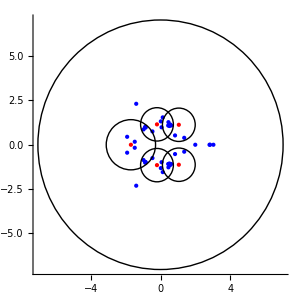

```mathematica
(*
 generate polar perimters 
*)
 Print["Pole indexes: ",$poleIndexes];
If[Length@$poleIndexes>1,
nearestPole=(NearestTo[#1,2][$theSingularList[[$poleIndexes]]]&/@ $theSingularList[[$poleIndexes]])[[All,2]];
nearestDistArray=MapThread[Abs[#1-#2]&,{$theSingularList[[$poleIndexes]],nearestPole}];
poleRadiusArray=MapThread[3/4Abs[#1-#2]&,{$theSingularList[[$poleIndexes]],nearestPole}];
 theSings=$theSingularList;
thePoles=$theSingularList[[$poleIndexes]];
theRingList=Abs[#]&/@ theSings;
maxX=Abs[$theSingularList[[-1]]]+2;
maxX=theAnnuli[[-1,2]];

nonPoleIndexes=Complement[Range[1,Length@$theSingularList],$poleIndexes];

singG=Graphics@{PointSize[0.01],Blue,Point@(ReIm@#&/@ $theSingularList[[nonPoleIndexes]])};
poleG=Graphics@{PointSize[.01],Red,Point@(ReIm@#&/@ thePoles)};
polePerimetersG=Graphics@MapThread[Circle[ReIm@#1,#2]&,{$theSingularList[[$poleIndexes]],poleRadiusArray}];

(*circleX=Graphics@{Red,Circle[{2,-2},2Sqrt[2]]};*)
envelopeCircle=Graphics@Circle[{0,0},maxX];

Print@Show[{singG,poleG,polePerimetersG,envelopeCircle(*,circleX*)},Axes->True,AspectRatio->1,PlotRange->maxX,ImageSize->300];
,
maxX=theAnnuli[[-1,2]];
poleRadiusArray={maxX};
 theSings=$theSingularList;
envelopeCircle=Graphics@Circle[{0,0},maxX];

thePoles=theSingularList[[$poleIndexes]];
singG=Graphics@{PointSize[0.05],Blue,Point@(ReIm@#&/@ theSings)};
poleG=Graphics@{PointSize[.025],Red,Point@(ReIm@#&/@ thePoles)};
polePerimetersG=Graphics@MapThread[Circle[ReIm@#1,#2]&,{$theSingularList[[$poleIndexes]],poleRadiusArray}];
Print@Show[{singG,poleG,polePerimetersG,envelopeCircle(*,circleX*)},Axes->True,AspectRatio->1,PlotRange->maxX,ImageSize->300];
];
```

### 9.8.1.1: Set up translateFactor and translateFunction

```mathematica
translateFactor=1/2+3/2 I;

innerR=Abs[translateFactor-$theSingularList[[20]]];
outerR=Abs[translateFactor-$theSingularList[[42]]];
innerR//N
outerR//N

medialR=innerR+(outerR-innerR)/2;

alphaContourF[t_]:=translateFactor+medialR Exp[I t];
betaContourF[t_]:=medialR Exp[I t];
```

1.6039

2.05971

### Section 9.8.1.2: Draw non-central annular region with medial contour

```mathematica
innerCircleG=Graphics@Circle[ReIm@translateFactor,innerR];
outerCircleG=Graphics@Circle[ReIm@translateFactor,outerR];

annularDomainG=Graphics@{Opacity[0.1],Blue,Annulus[ReIm@translateFactor,{innerR,outerR}]};

translateFactorG=Graphics@{PointSize[0.01],Darker@Green,Point@ReIm@translateFactor};



 Manipulate[

ppA=ParametricPlot[ReIm[translateFactor+theR Exp[I t]],{t,-Pi,Pi},PlotStyle->Red];
Show[{annularDomainG,singG,poleG,ppA,translateFactorG,innerCircleG,outerCircleG},Axes->True,AspectRatio->1,PlotRange->4,ImageSize->500],
{{theR,medialR//N},0.25,6}
]
```

Show::gcomb: Could not combine the graphics objects in Show[{annularDomainG,singG,poleG,,translateFactorG,innerCircleG,outerCircleG},Axes→True,AspectRatio→1,PlotRange→4,ImageSize→500].

### 9.8.1.3: Draw alpha branch

```mathematica
medialPrecision=20;
 alphaMonodromyList=getMonodromyOverContour[alphaContourF,$thetaV,$thetaV+2 Pi,$theFunction,False,medialPrecision]
```

{{4,5},{1},{2},{3}}

```mathematica
alphaContourData=generateCustomMedialContour[alphaContourF,$theFunction,alphaMonodromyList,1,medialPrecision];

alphaContourPlot=ParametricPlot3D[{Re@z,Im@z,Re@alphaContourData[[3]][t]}/.z->alphaContourF[t],{t,$thetaV,$thetaV+4 Pi},BoxRatios->{1, 1, 1}]
```

tStart: 0.523599

tEnd: 13.09

test

-Graphics3D-

```mathematica
medialPrecision=30;
 betaMonodromyList=getMonodromyOverContour[betaContourF,$thetaV,$thetaV+2 Pi,translatedFunction,False,medialPrecision]
```

{{4,5},{1},{2},{3}}

### Generate branch expansions in alpha domain

```mathematica
userMenu933d=Labeled[Column[{Row[{Style["Partition size:",Black,Bold],Spacer[5],InputField[Dynamic@$partitionSize933d,FieldSize->2],Spacer[10],Style["Range:",Black,Bold],Spacer[5],InputField[Dynamic@$range933d,FieldSize->8]}],
Row[{Checkbox[Dynamic[$doPolishFlag933d]],Spacer[3],Style["polishIntegral ",Black,Bold],
Spacer[12],Style["polishPrecision:",Black,Bold],Spacer[5],InputField[Dynamic@$polishPrecision933d,FieldSize->12]}]
},Frame->True,FrameStyle->Thick],Style["Annular branch power expansion user menu",Bold,Black],Top]
```

Partition size:Range:
polishIntegral polishPrecision:Annular branch power expansion User Menu

```mathematica
If[$doPolishFlag933d,
medialPrecision=$polishPrecision933d;
,
medialPrecision=MachinePrecision;
];

 medialPrecision=20;
 alphaMonodromyList=getMonodromyOverContour[alphaContourF,$thetaV,$thetaV+2 Pi,$theFunction,False,medialPrecision]
```

{{4,5},{1},{2},{3}}

```mathematica
totalBranches=Length@alphaMonodromyList;


(*termRange=Range[Sequence@@$range9111];*)
termRange=Range[Sequence@@$range933d];
If[$doPolishFlag933d,
integrationPrecision=$polishPrecision933d;
,
integrationPrecision=medialPrecision;
];

alphaSeriesSet=Table[

selectedBranch=alphaMonodromyList[[branchIndex]];
Print[Style["Analyzing branch ",Red,14],selectedBranch];
selectedBranchSize=Length@alphaMonodromyList[[branchIndex]];

rNorm=medialR;
tStart=$thetaV;
tEnd= tStart+2 Pi selectedBranchSize;


 rationalRNorm=Rationalize[rNorm,10^-25];
Print["Generating medial contour"];
{tStart,tEnd,lowPrecMedialSol,selectedBranchSize}=(*generateMedialContour[annulusTable,$selectedAnnulus933b,branchIndex,integrationPrecision,1/2];*)
generateCustomMedialContour[alphaContourF,$theFunction,alphaMonodromyList,branchIndex,medialPrecision];
Print["prec: ",Precision@lowPrecMedialSol];

 numPart=$partitionSize933d;
t0=$thetaV;
t1=t0+2 Pi selectedBranchSize;
intervalArray=Array[#&,numPart+1,{t0,t1}];
thePartitions=Partition[intervalArray,2,1];
theBranchTerms=Table[
If[Mod[k,10]==0,
Print[k];
];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/selectedBranchSize]-I Sin[t k/selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->integrationPrecision,AccuracyGoal->integrationPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
,
finalIntVal=Plus@@Table[
NIntegrate[lowPrecMedialSol[t](Cos[t k/selectedBranchSize]-I Sin[t k/selectedBranchSize]),{t,thePartitions[[index,1]],thePartitions[[index,2]]},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->integrationPrecision,AccuracyGoal->integrationPrecision/2,MaxRecursion->Infinity],
{index,1,Length@thePartitions}
];
];
coef=1/(2 Pi selectedBranchSize rNorm^(k/selectedBranchSize))finalIntVal;
{k/selectedBranchSize,coef,N[coef,10],coef (z^(1/selectedBranchSize))^k},
{k,termRange}
];
{selectedBranch,theBranchTerms},
{branchIndex,1,totalBranches}
];
```

Analyzing branch {4,5}

Generating medial contour

tStart: 0.523599

tEnd: 13.09

test

prec: 20.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

Analyzing branch {1}

Generating medial contour

tStart: 0.523599

tEnd: 6.80678

test

prec: 20.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

Analyzing branch {2}

Generating medial contour

tStart: 0.523599

tEnd: 6.80678

test

prec: 20.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

Analyzing branch {3}

Generating medial contour

tStart: 0.523599

tEnd: 6.80678

test

prec: 20.

-100

-90

-80

-70

-60

-50

-40

-30

-20

-10

0

10

20

30

40

50

60

70

80

90

100

### Choose a branch index into alphaSeriesSet to check

```mathematica
(*
 the branches are organized in alphaSeriesSet as 1--{4,5}, 2-->{3},3-->{4},4-->{5} 
*)

branchIndex=1;  

 alpha1[z_]=Plus@@alphaSeriesSet[[branchIndex,2,All,4]];
zTest=alphaContourF[2 Pi/14];
alpha1[zTest-translateFactor]//N
wVals=w/.NSolve[$theFunction==0/.z->zTest,w,WorkingPrecision->25]//N
expList=Exponent[alpha1[z],z,List];
coefList=Coefficient[alpha1[z],z,expList];
Length@coefList
alpha2F[z_,k_]:=Sum[coefList[[n]] (Exp[2 k π ⅈ expList[[n]]]) z^expList[[n]],{n,1,Length[coefList]}];
aVal=alpha2F[zTest-translateFactor,1]
difVals=Abs[aVal-#]&/@ wVals;
pos=Position[difVals,Min@difVals][[1]];
Print["Accuracy: ",difVals[[pos]]]
```

0.864193-0.410983 ⅈ

{-0.724105+0.344261 ⅈ,-0.502081-0.593463 ⅈ,0.459352+0.67385 ⅈ,0.86419-0.410983 ⅈ,3.15605-0.385438 ⅈ}

201

3.156047709861470027-0.3854361612814786452 ⅈ

Accuracy: {2.26614×10^-6}

### Plot the 2-cycle branch in the alpha domain using the alpha series

```mathematica
p1=ParametricPlot3D[{Re@z,Im@z,Re@alpha2F[z,0]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},PlotStyle->Blue];
p2=ParametricPlot3D[{Re@z,Im@z,Re@alpha2F[z,1]}/.z->r Exp[I t],{r,innerR,outerR},{t,-Pi,Pi},BoxRatios->{1, 1, 1},PlotStyle->Red];


Show[{p1,p2},PlotRange->All]
```

-Graphics3D-

### Root Test of analytic terms for upper limit of convergence

```mathematica
zeroPos= Position[alphaSeriesSet[[branchIndex,2,All,1]],0][[1,1]]
```

101

(-0.00676381-0.00865206 ⅈ) z^(5/2)-(0.00218206-0.00749957 ⅈ) z^3-(0.00485183-0.00373607 ⅈ) z^(7/2)-(0.00171199-0.000543695 ⅈ) z^4-(0.000957427+0.00243827 ⅈ) z^(9/2)

branch: {4,5}

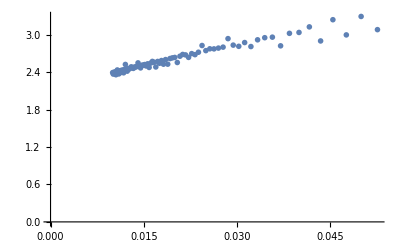

test2

min residue: 5.9428506

2.23007+5.25538 x+808.758 x^2-14014.5 x^3

Estimated upper annular convergence limit: 2.23007

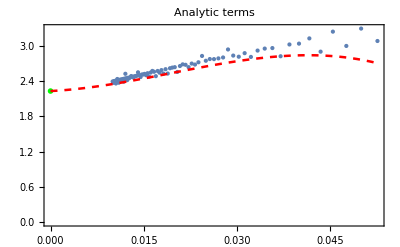

```mathematica
analyticSeries= Plus@@alphaSeriesSet[[branchIndex,2,(zeroPos+5);;,4]];
analyticSeries[[1;;5]]//N
cycleSize=Length@alphaMonodromyList[[branchIndex]];
Print["branch: ",alphaMonodromyList[[branchIndex]]];

seriesLength=Length@analyticSeries;
theexp=Exponent[analyticSeries,z,List];
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=Coefficient[analyticSeries,z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleSize/numVals[[k]])),15]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.01]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,12,Black,Bold]]


 startTermIndex=5;
endTermIndex=-1;
dataVals=cTable[[startTermIndex;;endTermIndex]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;
Print["test2"];
linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1},WorkingPrecision->15][[2]];
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2},WorkingPrecision->15][[2]];
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3},WorkingPrecision->15][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["min residue: ",residueSet[[bestFitPos]]];

Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];
fitResults=rTest;
Print["Estimated upper annular convergence limit: ",fitResults//N];

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.0075]},Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14,Bold,Black],Rotate[Style["",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,12,Black,Bold]];

thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
Show[{lp1,plotSet[[bestFitPos]],fitValueG},PlotLabel->Style["Analytic terms",Bold,Black]]
```

### Root Test of singular terms for lower limit of convergence

```mathematica
zeroPos= Position[alphaSeriesSet[[branchIndex,2,All,1]],0][[1,1]]
```

101

```mathematica
singularSeries= Plus@@alphaSeriesSet[[branchIndex,2,1;;(zeroPos-5),4]];
singularTerms=alphaSeriesSet[[branchIndex,2,1;;100,4]];
singularSeries[[1;;5]]//N
cycleSize=Length@alphaMonodromyList[[branchIndex]];

Print["branch: ",alphaMonodromyList[[branchIndex]]];

seriesLength=Length@singularSeries;
theexp=Exponent[singularSeries,z,List];
theexp=Exponent[#,z]&/@ singularTerms;
lcm=LCM@@(Denominator@theexp);
numVals=lcm theexp;
clist=MapThread[Coefficient[#1,z,#2]&,{singularTerms,theexp}];


cTable=Reverse@Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleSize/numVals[[k]])),25]},
{k,5,Length@clist}];

(*Print["cTable Len: ",Length@cTable];*)
singularLp1=ListPlot[cTable,PlotStyle->{PointSize[0.01]},AxesOrigin->{0,0},Frame->{{False,True},{True,False}},FrameTicks->{{None,All},Automatic},FrameLabel->{{None,Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},{Style["1/m_k",16,Bold,Black],None}},AspectRatio->1,FrameTicksStyle->Directive[Black,12,Black,Bold]];

singPlotRange=PlotRange[singularLp1];

dataValStart=10;
dataValEnd=-1;
dataVals=cTable[[dataValStart;;dataValEnd]];
plotXStart=0;
plotXEnd=dataVals[[10,1]];


linearLine=c0+c1 x/. Minimize[{Total[((c0+c1 #[[1]])-#[[2]])&/@dataVals],And@@(((c0+c1 #[[1]])>=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)>=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)-#[[2]])&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)>=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];

linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};


functionList={linearLine,quadraticLine,cubicLine};
bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];

Print["residueSet: ",residueSet//N];
Print["Best fit function: ",functionList[[bestFitPos]]//N];
Print["Minimum Residue: ",residueSet[[bestFitPos]]//N];
convergenceValue=functionList[[bestFitPos]]/.x->0;
Print["Estimated convergence domain: ",convergenceValue];

convergenceCircle=Graphics@{Red,Disk[{0,convergenceValue},ImageScaled[{.01,.01}]]};


singularBestFitPlot=Plot[functionList[[bestFitPos]],{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red},TicksStyle->Directive[Black,Bold,12]];
singularRootTestPlot=Show[{singularLp1,singularBestFitPlot,convergenceCircle},PlotStyle->{PointSize[0.005]},PlotRange->{{plotXStart,plotXEnd},Automatic}]
```

-(2.60064×10^6+1.32538×10^7 ⅈ)/z^50+(1.00866×10^7-4.10717×10^6 ⅈ)/z^(99/2)+(4.92062×10^6+7.17339×10^6 ⅈ)/z^49-(4.89755×10^6-4.99167×10^6 ⅈ)/z^(97/2)-(4.75728×10^6+2.97349×10^6 ⅈ)/z^48

branch: {4,5}

residueSet: {105.783,105.783,1.50368}

Best fit function: 1.55127+18.3833 x+218.618 x^2+1058.53 x^3

Minimum Residue: 1.50368

Estimated convergence domain: 1.55127

-Graphics-

## Initialization Cell:

### Initialize variables

```mathematica
(*
 Turn off all operator ligatures for old-style brackets (changes compact brackets to old-style [[]] brackets
*)
CurrentValue[$FrontEnd,{StyleHints,"OperatorRenderings"}]={}



Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]

 $analyticPrecisionArray={75,100};
$singularPrecisionArray={75,100};
<<ComputationalGeometry`
$HistoryLength=0;
flashDirectory="G";


$userDirectory="D:\\puiseuxSeries";

$range933d={-10,10};
$partitionSize933d=1;
$polishPrecision933d=30;
$doPolishFlag933d=False;



 $userDirectory="D:\\puiseuxSeries";
 $workingPrecision=1000;
 $thetaV=Pi/6;
 $separationFactor;
 $maxRootVerifyDistance=10^-50;
 $accuracyComparisonFactor=20;
 $ringDelta=1/10000;
 $integrationPartition=1;
 $showPlotLabel=False;
 $useAnalyticCodeArray=False;
 $useSingularCodeArray=False;

 $multiPrecisionArray={25,50,75};
 $analTermMin=0;
 $analTermMax=50;
 $singTermMin=-50;
 $singTermMax=-1;
 $analyticMedialIndex=3;
 $singularMedialIndex=3;
 $analyticPolishPrecision=200;


  $precisionIndexingType=1;
 $sequenceFunctionIndexStart=1;
 $sequenceFunctionIndexEnd=100;
 $userDefinedIndexStart=0;
 $userDefinedIndexEnd=100;

 $preciseSingularIntegrationPartition=1;
 $preciseSingularPolishPrecision=200;
 $preciseSingularPolishIndexingType=1;
 $preciseSingularPolishSequenceStart=-1;
 $preciseSingularPolishSequenceEnd=-100;
 $preciseSingularUserDefinedStart=-1;
 $preciseSingularUserDefinedEnd=-200;

 $preciseAnalyticIntegrationPartition=1;
 $preciseAnalyticPolishPrecision=200;
 $preciseAnalyticPolishIndexingType=1;
 $preciseAnalyticPolishSequenceStart=1;
 $preciseAnalyticPolishSequenceEnd=200;
 $preciseAnalyticUserDefinedStart=0;
 $preciseAnalyticUserDefinedEnd=200;

  $analyticRootTestStartTerm=5;
  $analyticRootTestEndTerm=-1;
 $analyticRootTestMinimizeEndRatio=1/10;
$analyticRootTestJoinPlot=True;
$analyticSequenceButtonFlag=False;
$singularSequenceButtonFlag=False;


  $singularRootTestStartTerm=5;
 $singularRootTestEndTerm=-2;

 $selectedAnnulus=1;
 $selectedMonodromyIndex=1;
 $plotType=Re;
 $selectedBranch;
 $selectedBranchSize;
 
 
theTypes={Re,Im}

 DistributeDefinitions[
z,
w,
c,
s,
$workingPrecision,
$separationFactor,
$thetaV,
$integrationPartition,
$showPlotLabel
]
```

{}

{Re,Im}

{$workingPrecision,$thetaV,$integrationPartition,$showPlotLabel}

```mathematica
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];
theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];

Quiet[Select[Names["System`*"],Attributes[#]==={Protected}&&ColorQ[ToExpression[#]]&]]
{"Black","Blue","Brown","Cyan","Gray","Green","LightBlue","LightBrown","LightCyan","LightGray","LightGreen","LightMagenta","LightOrange","LightPink","LightPurple","LightRed","LightYellow","Magenta","Orange","Pink","Purple","Red","Transparent","White","Yellow"}
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
colorTable=Flatten@theColorList;
colorTable[[1;;10]]={Blue,Red,Yellow,Brown,Cyan,Green,Orange,Pink,Purple,Magenta}
```

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{Black,Blue,Brown,Cyan,Gray,Green,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Transparent,White,Yellow}

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0.6, 0.4, 0.2],RGBColor[0, 1, 1],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0.5],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 1]}

### polyForm

```mathematica
polyForm[poly_,var_]:=Module[{coeffs=CoefficientRules[poly,var]//Sort},Interpretation[Row[Table[Row[{"(",coeff[[2]],")",var^coeff[[1,1]]/.1->""}],{coeff,coeffs}],"+"],poly]]
```

```mathematica
(* parallelize version *)
 
getRingMonodromy[ringNum_,baseComparisonAccuracy_]:=Module[{precisionArray,rnorm,zstart,theBaseValues,theBaseValueDigits,tStart,tEnd,branchValues,root,wstart,wstartDigits,wDeriv,posFoundFlag,numTries,theCentralTrace,theCentralTraceValueDigits,loopPos,loopPosVal,zStartPrecision,myazsol,aIndex,sIndex},
precisionArray={{1/1000,20},{1/2000,20},{1/3000,20},{1/5000,30},{1/6000,30},{1/7000,30},{1/10000,40},{1/12000,40},{1/15000,40},{1/20000,50},{1/25000,55},{1/30000,55},{1/30000,60}};
  
     (*  For[ringNum=83,ringNum≤Length[ringRegions],ringNum++, *)    

Print[Style["Analyzing ring ",Red],Style[ringNum,Red]];
{aIndex,sIndex}=getSingTableIndexes[annulusTable,ringNum];
rnorm=annulusTable[[aIndex,4]];
(*rnorm=radiiTable[[ringNum,(radialSegments-1)/2+1]];*)
zstart=rnorm Exp[ⅈ $thetaV];
zStartPrecision=Precision[zstart];
theBaseValues=w/.NSolve[$theFunction==0/.z->zstart,w,WorkingPrecision->workingPrecision];
theBaseValues=Sort[theBaseValues,If[Re[#1]!=Re[#2],
Re[#1]<Re[#2]
,
Im[#1]<Im[#2]
]&];
theBaseValueDigits=getDigits[theBaseValues,baseComparisonAccuracy];
tStart=$thetaV;
tEnd=$thetaV+2 π ;
branchValues={};
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (ⅈ rnorm Exp[ⅈ t]))/.{w->w[t],z->rnorm Exp[ⅈ t]});
 (* For[root=4,root≤4,root++, *) 
 For[root=1,root≤functionDegree,root++,  
wstart=theBaseValues[[root]];
wstartDigits=getDigits[wstart,baseComparisonAccuracy]//First;
posFoundFlag=False;
numTries=1;
While[posFoundFlag==False && numTries≤Length[precisionArray],
If[numTries>3,
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"]];
,
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]]];
];
theCentralTrace[t_]=Evaluate[Flatten[w[t]/.myazsol]];
theCentralTraceValueDigits=getDigits[theCentralTrace[tEnd],baseComparisonAccuracy]//First;
loopPos=Position[theBaseValueDigits,theCentralTraceValueDigits];
If[Length[loopPos]≠1,
Print["Error finding digits for root num ",root," Increasing precision to ",precisionArray[[numTries]]," ",numTries," of 13"];
If[numTries>3,
Print["Switching to StiffnessSwitching method"];
];
,
loopPosVal=loopPos//First;
branchValues=Append[branchValues,{wstartDigits,theBaseValueDigits[[loopPosVal[[1]]]]}];
posFoundFlag=True;
];
numTries++;
];
If[posFoundFlag==False,
Print["Position not found at end of ",Length[precisionArray], " attempts at increasing precision."];
Abort[];
];
];
branchValues
];

(* parallizing versioin *)



getSingularPointMonodromy[singNum_,baseComparisonAccuracy_]:=Module[{precisionArray,rnorm,singularStartArg,zstart,theBaseValues,theBaseValueDigits,tStart,tEnd,wstart,wstartDigits,wDeriv,posFoundFlag,numTries,myazsol,theCentralTrace,theCentralTraceValueDigits,loopPos,branchValues,rmax,root,saveBaseDigits,poleFlag,j,savePoleValues},
precisionArray={{1/1000,20},{1/2000,20},{1/3000,20},{1/5000,30},{1/6000,30},{1/7000,30},{1/10000,40},{1/12000,40},{1/15000,40},{1/20000,50},{1/25000,55},{1/30000,55},{1/30000,60}};
branchValues={};
saveBaseDigits={};
savePoleValues={};
rnorm=$minRadiusArray[[singNum]];
singularStartArg=argList[[singNum]]-π;
Print["Analyzing monodromy around singular point ",singNum, " : ",N[$theSingularList[[singNum]],8]];
zstart=$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
(*If[singNum==Length[$theSingularList],
Print["Analyzing monodromy around infinity"];
zstart=$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
,
Print["Analyzing monodromy around singular point ",singNum, " : ",N[$theSingularList[[singNum]],8]];
zstart=$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
];*)
theBaseValues=w/.NSolve[$theFunction==0/.z->zstart];
theBaseValues=Sort[theBaseValues,If[Re[#1]!=Re[#2],
Re[#1]<Re[#2]
,
Im[#1]<Im[#2]
]&];
(*Print["theBaseValues: ",theBaseValues//N];*)
theBaseValueDigits=getDigits[theBaseValues,baseComparisonAccuracy];
(* now check if this is a pole *)
poleFlag=False;
If[MemberQ[poleIndexes,singNum],
poleFlag=True;
AppendTo[savePoleValues,{singNum,theBaseValues}];
];
(*For[j=1,j≤Length[pole2],j++,
If[$theSingularList[[singNum]]==pole2[[j]],
 poleFlag=True;
];
];*)
zstart=$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg];
If[poleFlag,
saveBaseDigits=Append[saveBaseDigits,{singNum,$theSingularList[[singNum]]+$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg],$minRadiusArray[[singNum]] Exp[ⅈ singularStartArg]}];
];
tStart=singularStartArg;
tEnd=tStart+2 π;
rmax=Length[theBaseValues];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) (ⅈ rnorm Exp[ⅈ t]))/.{w->w[t],z->$theSingularList[[singNum]]+rnorm Exp[ⅈ t]});
For[root=1,root≤rmax,root++,
wstart=theBaseValues[[root]];
wstartDigits=getDigits[wstart,baseComparisonAccuracy]//First;
posFoundFlag=False;
numTries=0;
While[posFoundFlag==False && numTries≤13,
numTries++;
If[numTries>3,
Print["Switching to StiffnessSwitching"];
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]],Method->"StiffnessSwitching"]];
,
myazsol=First[NDSolve[{wDeriv,w[tStart]==wstart},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->precisionArray[[numTries,1]],WorkingPrecision->precisionArray[[numTries,2]]]];
];
theCentralTrace[t_]=Evaluate[Flatten[w[t]/.myazsol]];
theCentralTraceValueDigits=getDigits[theCentralTrace[tEnd],baseComparisonAccuracy]//First;
loopPos=Position[theBaseValueDigits,theCentralTraceValueDigits];
If[Length[loopPos]≠1,
Print["Error with loopPos: ",loopPos];
 Print["Base Value digits: ",theBaseValueDigits];
Print["base values: ",theBaseValues//N];
Print["the Central trace Digits: ",theCentralTraceValueDigits]; 
Print["central trace: ",theCentralTrace[tEnd]];
,
branchValues=Append[branchValues,{wstartDigits,theBaseValueDigits[[loopPos[[1,1]]]]}];
posFoundFlag=True;
];
];
If[posFoundFlag==False,
Print["Position not found at end of 10 attempts at increasing precision."];
Abort[];
];
];
{branchValues,saveBaseDigits,savePoleValues}
];
```

### Subroutine call for initialization of data

```mathematica
(* attempt to make sub for init data *)



(* In order to have unique barycentric ids for each vertex, must use radialSegments=3n+1 and odd for vertex calculations to find a mid point*)

radialSegments=13;
(* arcSegments is 2n *)
arcSegments=48;
totalIntegrationSteps=1500000;
maxStepSize=0.0001;
workingPrecision=75;

ringDelta=1/20000; (* ring separation threshold *)
minRingSize=1/2000;

initializationFunction[theFunction_]:=Module[{singlist,singularPrecision,theValues,polePrecision,newPrecision,sing2,rings,pre,ring2,theRingSet,ringDifferences,i,j,min,distance,preRingSize,postRingSize,newRing,theRingDigits,theSingList,singStyle,index,currentSing,pos},
functionOrder=Exponent[theFunction,w];
singlist=(z/.NSolve[Resultant[theFunction,D[theFunction,w],w]==0,z,WorkingPrecision->workingPrecision]);
singularPrecision=Precision[singlist];

theValues=NSolve[Coefficient[theFunction,w^functionOrder]==0,z,WorkingPrecision->workingPrecision];
If[Length[theValues]>0,
thePoles=z/.theValues;
polePrecision=Precision[thePoles];
,
thePoles={};
polePrecision=singularPrecision;
];
(* take min of these precison *)
newPrecision=Min[singularPrecision,polePrecision];
Print ["Working precision of computations: ",newPrecision];

sing2=SetPrecision[singlist,newPrecision-2];
pole2=SetPrecision[thePoles,newPrecision-2];
pole2=Sort[DeleteDuplicates[pole2],Abs[#1]≤Abs[#2]&];
sing3=Sort[DeleteDuplicates[sing2],Abs[#1]≤Abs[#2]&];
$theSingularList=sing3;
rings=Sort[Abs[singlist]];
pre=Precision[rings];
ring2=SetPrecision[rings,pre-2];
ring3=Sort[DeleteDuplicates[ring2]];

theRingSet=Union[{0},ring3,{Last[ring3]+4}];
ringRegions=Table[{0,0},{Length[theRingSet]-1}];
For[i=1,i≤Length[theRingSet]-1,i++,
ringRegions[[i,1]]=theRingSet[[i]]+ringDelta;
ringRegions[[i,2]]=theRingSet[[i+1]]-ringDelta;
];

ringDifferences={#[[2]]-#[[1]]}& /@ ringRegions;
If[Length[Select[Flatten[ringDifferences],#<1/5000&]]>1,
Print[Style["Ring size too small",Red]];
Print[Select[Flatten[ringDifferences],#<1/5000&]];
Abort[];
];

radiiTable=Table[Array[#&,radialSegments,ringRegions[[i]]],{i,1,Length[ringRegions]}];

(* need to flag this as an expansion around the origin *)

singularPointExpansion=False;


minArray={};
For[i=1,i≤Length[sing3],i++,
currentSing=sing3[[i]];
min=10^6;
For[j=1,j≤Length[sing3],j++,
If[j≠i,
distance=Sqrt[(Re[currentSing]-Re[sing3[[j]]])^2+(Im[currentSing]-Im[sing3[[j]]])^2];
If[distance<min,
min=distance;
];
];
];
minArray=Append[minArray,min/2];
];
sing3=Append[sing3,0];
(* now add a circle around all singular points for the point at infinity *)
minArray=Append[minArray,Max[ring3]+2];
(* and add zero as the center of this ring.  The added zero at the end allows a spacer so when it gets to this point *)
(* the ring monodromy will be around all finite singular points so is the mondromy around infinity  *)
(* now add zero at end of singular list for point at infinity *)
(*
  now save this copy of min array to use as radius of convergence of power series 
*)

$theSingularList=Append[$theSingularList,0];
theArgList=Map[Arg,$theSingularList];
(*  now that args are computed, switch last singular point to infty *)
$theSingularList[[-1]]=∞;
$theSingularListGraphics=MapThread[{#1,#2}&, {Range[Length[$theSingularList]],$theSingularList//N}];

For[i=1,i≤Length[$theSingularList],i++,
For[j=1,j≤Length[pole2],j++,
If[$theSingularList[[i]]==pole2[[j]],
 $theSingularListGraphics[[i]]={Style[$theSingularListGraphics[[i,1]],Red],Style[$theSingularListGraphics[[i,2]],Red]}; 
];
];
];
(* --------------------------------------------------*)
theRingList=MapThread[{#1,#2}&,{Range[Length[ringRegions]],ringRegions}];
theRingListGraphics=MapThread[{#1,#2,#3}&,{Range[Length[ringRegions]],ringRegions//N,ringDifferences//N}];
(* now adjust radius around each finite point to 1/3 minimum distance between rings or to nearest singular point *)
For[i=2,i≤Length[theRingList],i++,
For[j2=1,j2≤Length[$theSingularList],j2++,
If[Abs[$theSingularList[[j2]]]<theRingList[[i,2,1]] && Abs[$theSingularList[[j2]]]>theRingList[[i-1,2,2]],
preRingSize=(theRingList[[i-1,2,2]]-theRingList[[i-1,2,1]])/3;
postRingSize=(theRingList[[i,2,2]]-theRingList[[i,2,1]])/3;
minArray[[j2]]=Min[{minArray[[j2]],preRingSize,postRingSize}];
];
];
];

newRing=Select[ring3,#>0&];
For[i=1,i≤Length[newRing],i++,
newRing[[i]]={newRing[[i]],{}};
];
theRingDigits=getDigits[newRing[[All,1]],10];
theSingList=Select[sing3,Abs[#]>0&];
For[i=1,i≤Length[theSingList],i++,
pos=Position[theRingDigits,getDigits[Abs[theSingList[[i]]],10][[1]]][[1,1]];
singStyle=Style[theSingList[[i]]//N];
For[j=1,j≤Length[pole2],j++,
If[theSingList[[i]]==pole2[[j]],
 singStyle=Style[theSingList[[i]]//N,Red]; 
];
];
newRing[[pos,2]]=Append[newRing[[pos,2]],singStyle];
];

ringDisplay={};
For[i=1,i≤Length[newRing],i++,
ringDisplay=Append[ringDisplay,{i,newRing[[i,1]],newRing[[i,2]]}];
];
finalRingDisplay={};
If[$theSingularList[[1]]==0,
finalRingDisplay=Append[finalRingDisplay,{" "," ",Subscript[s, 0],Style[0,Red]}];
];
index=0;
For[i=1,i≤Length[ringDisplay],i++,
index++;
finalRingDisplay=Append[finalRingDisplay,{Subscript[r, ringDisplay[[i,1]]],ringDisplay[[i,2]]//N,Subscript[s, index],ringDisplay[[i,3,1]]}];
If[Length[ringDisplay[[i,3]]]>1,
For[j=2,j≤Length[ringDisplay[[i,3]]],j++,
index++;
finalRingDisplay=Append[finalRingDisplay,{" "," ",Subscript[s, index],ringDisplay[[i,3,j]]}];
];
];
];
Print[finalRingDisplay//MatrixForm];
];

generateIntegerFunction[zdegree_,wdegree_,maxlim_]:=Module[{thenumber,mylist,aseq,atemp,a,theFunction},
thenumber=IntegerDigits[RandomInteger[{1,2^((wdegree+1)(zdegree+1))-1}],2,(zdegree+1)(wdegree+1)];
mylist=Table[aseq=Take[thenumber,{(zdegree+1)(n-1)+1,(zdegree +1)n}];
atemp=Table[If[aseq[[j]]≠0,
RandomInteger[{-maxlim,maxlim}]Power[z,j-1],"A"],{j,1,zdegree+1}];
Subscript[a, n-1]=Plus@@DeleteCases[atemp,_String],{n,1,wdegree+1}];
theFunction=Plus@@Table[Subscript[a, n] w^n,{n,0,wdegree}]
];

generateRationalFunction[zdegree_,wdegree_,maxlim_]:=Module[{thenumber,mylist,aseq,atemp,a,theFunction,num,denom,theval,temp},
thenumber=IntegerDigits[RandomInteger[{1,2^((wdegree+1)(zdegree+1))-1}],2,(zdegree+1)(wdegree+1)];
mylist=Table[aseq=Take[thenumber,{(zdegree+1)(n-1)+1,(zdegree +1)n}];
atemp=Table[If[aseq[[j]]≠0,
{
num=RandomInteger[{-maxlim,maxlim}];
denom=RandomInteger[{-maxlim,maxlim}];
While[denom==0,
denom=RandomInteger[{-maxlim,maxlim}];
];
theval=num/denom Power[z,j-1];
}
,
theval="A"];
theval,{j,1,zdegree+1}];
Subscript[a, n-1]=Plus@@DeleteCases[atemp,_String],{n,1,wdegree+1}];
theFunction=Plus@@Table[Subscript[a, n] w^n,{n,0,wdegree}]
];
```

```mathematica
FourierSmooth[Graphics[{___,Style[Line[pts_],___],___}],numFourCoeff_Integer]:=Module[{wx,wy,ftsum,w,nn},If[numFourCoeff<1||numFourCoeff>nn/2,
Return[$Failed]
];
nn=Length[pts];
{wx,wy}=Fourier/@Transpose[pts];
ftsum[t_]:=Evaluate[1/Sqrt[nn](w[1]+Sum[2w[i+1]*Exp[-2Pi I t i/nn],{i,1,numFourCoeff}])];
Show[{
Graphics[{Gray,Dashed,Line[pts]}],
ParametricPlot[Re[ftsum[t]]/.w[i__]:>{wx[[i]],wy[[i]]},{t,0,nn},PlotStyle->{Magenta},Axes->False,Frame->True]
}]
]

FourierSmooth3[Graphics[{___,Line[pts_]}],numFourCoeff_Integer]:=Module[{wx,wy,ftsum,w,nn},
If[numFourCoeff<1||numFourCoeff>nn/2,
Return[$Failed]
];
nn=Length[pts];
Print["total points: ",nn];
{wx,wy}=Fourier/@Transpose[pts];
ftsum[t_]:=Evaluate[1/Sqrt[nn](w[1]+Sum[2w[i+1]*Exp[-2Pi I t i/nn],{i,1,numFourCoeff}])];
Show[{
Graphics[{Gray,Dashed,Line[pts]}],
ParametricPlot[Re[ftsum[t]]/.w[i__]:>{wx[[i]],wy[[i]]},{t,0,nn},PlotStyle->{Magenta},Axes->False,Frame->True]
}]
]


FourierSmooth2[Graphics[Style[Line[pts_],___]],numFourCoeff_Integer]:=Module[{wx,wy,ftsum,w,nn},
If[numFourCoeff<1||numFourCoeff>nn/2,
Return[$Failed]
];
nn=Length[pts];
{wx,wy}=Fourier/@Transpose[pts];
ftsum[t_]:=Evaluate[1/Sqrt[nn](w[1]+Sum[2w[i+1]*Exp[-2Pi I t i/nn],{i,1,numFourCoeff}])];
Show[{
Graphics[{Gray,Dashed,Line[pts]}],
ParametricPlot[Re[ftsum[t]]/.w[i__]:>{wx[[i]],wy[[i]]},{t,0,nn},PlotStyle->{Magenta},Axes->False,Frame->True]
}]
]
getDigitsOld[vals_,n_]:=Module[{net,theDigits,i,theChoppedVals,theComponents,myList},
If[Length[vals]==0,
myList={vals};
,
myList=vals;
];
net=Length[myList];
theChoppedVals=Chop[myList,10^(-n)];
theComponents={Re[#],Im[#]}& /@ theChoppedVals;
theDigits=RealDigits[theComponents,10,n];
For[i=1,i≤net,i++,
If[Re[theChoppedVals[[i]]]<0,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],-1];
,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],1];
];
If[Im[theChoppedVals[[i]]]<0,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],-1];
,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],1];
];
];
theDigits
];
getDigitsOld2[vals_,n_]:=Module[{net,theDigits,i,theChoppedVals,theComponents,myList},
If[Length[vals]==0,
myList={vals};
,
myList=vals;
];
myList=SetAccuracy[myList,2n+2];
net=Length[myList];

theComponents={Re[#],Im[#]}& /@ myList;
theChoppedVals=Chop[theComponents,10^(-n)];
theDigits=RealDigits[theChoppedVals,10,n];
For[i=1,i≤net,i++,
If[theChoppedVals[[i,1]]<0,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],-1];
,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],1];
];
If[theChoppedVals[[i,2]]<0,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],-1];
,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],1];
];
];
theDigits
];

getDigits[vals_,n_]:=Module[{net,theDigits,i,theChoppedVals,theComponents,myList,listAccuracy},
If[Length[vals]==0,
myList={vals};
,
myList=vals;
];
listAccuracy=Accuracy[myList];
(* set accuracy to n+1  to round-off 0.899999 to 0.9 and others *)
myList=SetAccuracy[myList,n+10];
net=Length[myList];

theComponents={Re[#],Im[#]}& /@ myList;
theChoppedVals=Chop[theComponents,10^(-n)];
theDigits=RealDigits[theChoppedVals,10,n];
For[i=1,i≤net,i++,
If[theChoppedVals[[i,1]]<0,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],-1];
,
theDigits[[i,1]]=Prepend[theDigits[[i,1]],1];
];
If[theChoppedVals[[i,2]]<0,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],-1];
,
theDigits[[i,2]]=Prepend[theDigits[[i,2]],1];
];
];
theDigits
];




DistributeDefinitions[{getRingMonodromy,getSingularPointMonodromy,getDigits}];
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];
```

### getRandomPoly

```mathematica
getRandomSingleCoeffPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,5}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
theFunction=Sum[randomNum[sparseVal] getcoef[8,5]z^getZPower[zExpMax] w^getWPower[wExpMax],{wExpMax}];
(*theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];*)
If[!IrreduciblePolynomialQ[theFunction],
index++;
,
foundFlag=True;
];
];
theFunction
]
```

```mathematica
getRandomPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[theFunction],
index++;
,
foundFlag=True;
];
];
theFunction
]


getRandomComplexPoly[zExpMax_,zPolySize_,wExpMax_,sparseVal_]:=Module[{randomNum,getZPower,getWPower,getcoef,foundFlag,index,functionDegree,theFunction,wExp},
 
randomNum[n_]:= RandomChoice[Join[Table[0,{n}],{1}]];
 getZPower[n_]:=randomNum[sparseVal]RandomInteger[{0,n}];
getWPower[n_]:= randomNum[sparseVal]RandomInteger[{0,n}];
getcoef[a_,b_]:=RandomInteger[{-a,a}]/RandomInteger[{1,b}]+I RandomInteger[{-a,a}]/RandomInteger[{1,b}];
foundFlag=False;
index=1;

While[!foundFlag && index<25,
theFunction=Sum[((Sum[getcoef[8,5] z^getZPower[zExpMax],{zPolySize}])  w^getWPower[wExpMax]),{25}];
If[!IrreduciblePolynomialQ[theFunction],
index++;
,
foundFlag=True;
];
];
theFunction
]
```

### getZeroIndexes

```mathematica
getZeroIndexes[theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable,dif},
wKeys=CoefficientRules[theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[theFunction,w,List];
poleFunction=Coefficient[theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$accuracyComparisonFactor;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
$poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
$poleIndexes
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### getSingTableIndexes

```mathematica
getSingTableIndexes[singTable_,annulus_]:=Module[{singMembers,singIndexes,annulusIndex,return},
If[annulus>Length@theAnnuli || annulus<0,
Print[Style["Annulus number out of range!",Red]];
return=-1;
,
annulusIndex=singTableAnnulusIndexes[[annulus]];
If[annulus==Length@theAnnuli,
singIndexes={-1};
,
singMembers=ringMemberSingularIndexes[[annulus]];
singIndexes=singTableSingIndexes[[singMembers]];
];
return={annulusIndex,singIndexes};
];
return
]
```

### getPartialBranchPlot

```mathematica
getPartialBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,radialSegments_:15,arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],workingPrecision];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(radialSegments-1)/2+2;;radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];

getPartialBranchPlot2[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,radialSegments_:15,arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000,theEnd_]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace,tEnd},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],workingPrecision];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+theEnd;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(radialSegments-1)/2+2;;radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### getBranchPlot

```mathematica
Options[getBranchPlot]={"radialSegments"->15,"arcSegments"->24,"totalIntegrationSteps"->2500000,"maxStepSize"->1/1000,"workingPrecision"->50};
getBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,OptionsPattern[]]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{OptionValue["radialSegments"]},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],OptionValue["workingPrecision"]];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=annulusTable[[aIndex,6]];
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
(* set up monodromy DE for medial contour integration *) 
tStart=$thetaV; (* begin integration at branch reference angle *)
tEnd=$thetaV+2π branchSize;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];

wStart=theRoots[[rootIndex]];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(OptionValue["arcSegments"] branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(OptionValue["radialSegments"]-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->OptionValue["totalIntegrationSteps"],MaxStepSize->OptionValue["maxStepSize"]]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(OptionValue["radialSegments"]-1)/2+2;;OptionValue["radialSegments"]]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### generateMedialContour

```mathematica
radiiTable//N
```

radiiTable

```mathematica
generateMedialContour[annulusTable_,annulus_,branchNum_,wpVal_,altNorm_:1/2]:=Module[{cycleSize,zFun,tEnd,wDeriv,selected,aIndex,sIndex,zStart,$selectedMonodromyList,theRoots,tStart,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
$selectedMonodromyList=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@$selectedMonodromyList;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
If[altNorm!=1/2,
rNorm=altNorm;
];
Print["Setting rNorm: ",rNorm//N];

zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ $thetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[$selectedMonodromyList[[1]]]];

tStart=$thetaV;
tEnd= tStart+2 Pi cycleSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[implicitF[z,w],z]/D[implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]

generatePartialMedialContour[annulusTable_,annulus_,branchNum_,wpVal_,altNorm_:1/2,tStart_,tEnd_]:=Module[{cycleSize,zFun,wDeriv,selected,aIndex,sIndex,zStart,$selectedMonodromyList,theRoots,wStart,medialSol,rNorm,newRNorm,theAnnulus},
{aIndex,sIndex}=getSingTableIndexes[annulusTable,annulus];
$selectedMonodromyList=annulusTable[[aIndex,6,branchNum]];
cycleSize=Length@$selectedMonodromyList;
theAnnulus=annulusTable[[aIndex,3]];

rNorm=annulusTable[[aIndex,4]];
If[altNorm!=1/2,
rNorm=radiiTable[[annulus,altNorm]];
];
Print["Setting rNorm: ",rNorm//N];

zFun[t_]:=rNorm Exp[I t];

zStart=zFun[ $thetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];
wStart=theRoots[[$selectedMonodromyList[[1]]]];

Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[implicitF[z,w],z]/D[implicitF[z,w],w]) (D[zFun[t],t]))/.{w->w[t],z->zFun[t]});

medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
Print["medialSol: ",medialSol[Pi/2]//N];
{tStart,tEnd,rNorm,medialSol,cycleSize}

]
```

### getMedialStartVals

```mathematica
getMedialStartVals[annulusTable_,$selectedAnnulus_,$selectedMonodromyIndex_,$thetaV_,implicitF_]:=Module[{aIndex,sIndex,$selectedMonodromyList,$selectedBranchSize,rNorm,zStart,theRoots,wStart},
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,$selectedAnnulus];
$selectedMonodromyList=annulusTable[[aIndex,6]];
$selectedBranchSize=Length@$selectedMonodromyList[[$selectedMonodromyIndex]];

rNorm=annulusTable[[aIndex,4]];
(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,(radialSegments-1)/2+1]],10^-6]*)
zStart=rNorm Exp[I $thetaV] ;

theRoots=w/.NSolve[implicitF[zStart,w]==0,w,WorkingPrecision->700];

wStart=theRoots[[$selectedMonodromyList[[$selectedMonodromyIndex,1]]]];
{rNorm,zStart,wStart}
];
```

### computeAnnularTerm

```mathematica
computeAnnularTerm[medialSol_,$selectedBranchSize_,tStart_,tEnd_,rNorm_,k_]:=Module[{intVal,ratioData,medialPrec},
medialPrec=(Precision@medialSol);
intVal=Check[NIntegrate[medialSol[t](Cos[t k/$selectedBranchSize]-I Sin[t k/$selectedBranchSize]),{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->medialPrec,AccuracyGoal->medialPrec/2,MaxRecursion->Infinity],-1,NIntegrate::slwcon];
If[intVal==-1,
Print["Encountered NIntegrate::slwcon error"];
ratioData={0,0,0};
,
ratioData=rNorm((2 $selectedBranchSize Pi)/Abs[intVal])^($selectedBranchSize/k);
];
{1/k,ratioData,Abs@intVal}
];
```

### getMaxOrder

```mathematica
getMaxOrder[series_]:=Module[{cycleExpList},
cycleExpList=Exponent[series,z,List];
{Floor@cycleExpList[[-1]],cycleExpList[[-1]]}
]
```

### getClosestIntegerOrder

```mathematica
getClosestIntegerOrder[orderVal_,series_]:=Module[{seriesSize,cycleExpList,nearestExpList,theVals,nearestExp,posArray,pos,seriesIndex},
seriesSize=Length@series[z];
cycleExpList=Exponent[series[z],z,List];
nearestExpList=Nearest[cycleExpList,orderVal];
If[Length@nearestExpList==0,
Print[Style["exponent not found",Red]];
theVals={"ea","ea"};
,
nearestExp=nearestExpList[[-1]];
posArray=Position[cycleExpList,x_/;x==nearestExp];
If[Length@posArray==0,
Print[Style["Error with posArray: ",Red],posArray];
theVals={"eb","eb"};
,
pos=posArray[[1,1]];
If[pos==seriesSize && orderVal>Round@nearestExp,
Print[Style["Requested order of series is greater than max series order ",Red],Style[Round@nearestExp,Red]];
theVals={"e","e"};
,
theVals={orderVal,pos,cycleExpList[[pos]]}
];
];

];
theVals
];
```

### getSingleConvergenceTrend

```mathematica
getSingleConvergenceTrend[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2,aDigits,decimalPosList,correctCharLen},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
Print["       Length actWChar: ",Length@actWChar];
Print["       Length seriesWChar: ",Length@seriesWChar];
maxCharFlag=True;
];

(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
correctCharLen=Length@correctChar;
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen,correctCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];

If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
maxCharIndex=sIndex;
];
(*
 now find decimal point
*)
decimalPosList=Position[testChar,x_/;x=="."];
If[Length@decimalPosList==0,
Print[Style["error with decimal location",Red]];
aDigits=0;
Abort[];
,
aDigits=i-decimalPosList[[1,1]]-1;
];

For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],aDigits,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendSeries[theSeries_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2,aDigits,decimalPosList},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=theSeries/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[theSeries,z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
Print["       Length actWChar: ",Length@actWChar];
Print["       Length seriesWChar: ",Length@seriesWChar];
maxCharFlag=True;
];

(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=theSeries[[1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];

If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
maxCharIndex=sIndex;
];
(*
 now find decimal point
*)
decimalPosList=Position[testChar,x_/;x=="."];
If[Length@decimalPosList==0,
Print[Style["error with decimal location",Red]];
aDigits=0;
Abort[];
,
aDigits=i-decimalPosList[[1,1]]-1;
];

For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],aDigits,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendSave[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex,maxCharLen2},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
(*If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];
*)
(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];
correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
maxCharLen2=Min@{Length@testChar,maxCharLen};
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen2,
i++;
];
If[i==maxCharLen,
(*Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];*)
maxCharFlag=True;
maxCharIndex=sIndex;
];
For[k=i,k<=maxCharLen2,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

```mathematica
getSingleConvergenceTrendTemp2[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag},
charMin=500;
maxCharFlag=False;
errorFlag=False;

singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];

For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];

errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];

correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen,
i++;
];
For[k=i,k<=maxCharLen,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]]},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"S",0,0,seriesWChar}];
PrependTo[cTable2,{"A",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

### getSingleConvergenceTrendTempSave

```mathematica
getSingleConvergenceTrendTempSave[seriesIndex_,centerIndex_,clsp_,wp_,zValue_,expInc_,type_]:=Module[{cTable,cTable2,zVal,wTest,theWList,theDif,pos,theIndex,s5,actW,singularPoint,convData,branchStats,typeIndex,limitPoint,maxRadius,errTable,correctNumber,correctChar,testChar,i,k,testNumber,expList,theExpNum,ePos,theExpList,rationalR,dataPoints,news5,baseF,tempB,tempZ,rTest,baseF2,theTestValue,pVal,newZ,powerList,seriesW,actWChar,seriesWChar,maxCharLen,maxCharFlag,charMin,errorFlag,basePrec,zPrec,maxCharIndex},
charMin=500;
maxCharFlag=False;
errorFlag=False;


singularPoint=$theSingularList[[centerIndex]];

limitPoint=$theSingularList[[clsp]];
baseF[t_]=baseSeries[[seriesIndex]]/.z->t;
pVal=Precision@baseF[t];
newZ=SetPrecision[zValue,pVal];
maxRadius=Abs[singularPoint-limitPoint];

ePos=Exponent[baseSeries[[seriesIndex]],z,List];

wTest=baseF[newZ];
theWList=w/.NSolve[$theFunction==0/.z->(singularPoint+newZ),w,WorkingPrecision->wp];
theDif=(Abs[wTest-#]&/@ theWList);
pos=Position[theDif,Min[theDif]];
actW=theWList[[pos[[1,1]]]];
seriesW=wTest;

actWChar=convertToChar[SetPrecision[type@actW,wp]];
seriesWChar=convertToChar[SetPrecision[type@seriesW,wp]];

If[Length@actWChar<charMin|| Length@seriesWChar<charMin,
Print["actWChar or seriesWChar lenght less than char min: "];
Print["actW: ",N[actW,20]];
Print["seriesW: ",N[seriesW,20]];
Print["actWChar length: ",Length@actWChar];
Print["seriesWChar length: ",Length@seriesWChar];
errorFlag=True;
,
maxCharLen=Min@{Length@actWChar,Length@seriesWChar};
i=1;
While[actWChar[[i]]==seriesWChar[[i]] && i<maxCharLen,
i++;
];
(*If[i==maxCharLen,
Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];
maxCharFlag=True;
];
*)
(*For[k=1,k<=i-1,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Black,Bold];
];*)

For[k=i,k<=maxCharLen,k++,
seriesWChar[[k]]=Style[seriesWChar[[k]],Red];
];


errTable=Table[
baseF2[t_]=baseSeries[[seriesIndex,1;;index]]/.z->t;
theTestValue=baseF2[newZ];
{ePos[[index]],SetPrecision[type@theTestValue,wp],Abs[actW-theTestValue]},
{index,expInc,Length@ePos,expInc}];

correctNumber=type@SetPrecision[ actW,wp];
correctChar=convertToChar[correctNumber];
cTable2=Table[
maxCharIndex=0;
testNumber=errTable[[sIndex,2]];
testChar=convertToChar[testNumber];
i=1;
While[correctChar[[i]]==testChar[[i]] && i<maxCharLen,
i++;
];
If[i==maxCharLen,
(*Print[Style["maxCharLen reached: ",Red],Style[maxCharLen,Red]];*)
maxCharFlag=True;
maxCharIndex=sIndex;
];

For[k=i,k<=maxCharLen,k++,
testChar[[k]]=Style[testChar[[k]],Red];
];
{sIndex expInc,errTable[[sIndex,1]],i-4,testChar[[1;;100]],maxCharIndex,i},
{sIndex,1,Length@errTable}
];
PrependTo[cTable2,{"Series",0,0,seriesWChar}];
PrependTo[cTable2,{"Act",0,0,actWChar}];
];
{maxRadius,cTable2,maxCharFlag,maxCharLen,errorFlag,maxCharFlag,i}
];
```

### convertToChar

```mathematica
convertToChar[num_]:=Module[{sTest,s1,newS,newS2},
sTest=ToString@AccountingForm@num;
s1=StringTake[sTest,1];
If[s1=="(",
newS=StringReplacePart[sTest,"-",{1,1}];
newS2=StringDrop[newS,-1];
Characters@newS2
,
Characters@sTest
]
];
```

### polishMedial

```mathematica
polishMedial[t_?NumericQ,r_?NumericQ,implicitF_,medialVal_?NumericQ,wPrec_?NumericQ]:=Module[{},
w/.FindRoot[implicitF[r Exp[I t],w]==0,{w,medialVal},WorkingPrecision->wPrec,AccuracyGoal->wPrec,PrecisionGoal->wPrec]
];
```

### formatNumber

```mathematica
formatNumber[num_]:=Module[{real,imag,realPart,imagPart,me,return},
If[Precision@Im@num<10 || Precision@Re@num<10,
return="E";
];

real=Re@num;
imag=Im@num;
If[Precision@real>10 && Precision@imag>10,
me=MantissaExponent[real];
realPart=N[10 me[[1]],5] 10^(me[[2]]-1);
me=MantissaExponent[imag];
imagPart=N[10 me[[1]],5] 10^(me[[2]]-1);
return=realPart+I imagPart;
,
If[Precision@imag<10,
me=MantissaExponent[real];
realPart=N[10 me[[1]],5] 10^(me[[2]]-1);
return=realPart;
,
If[Precision@real<10,
me=MantissaExponent[imag];
imagPart=N[10 me[[1]],5] 10^(me[[2]]-1);
return=I imagPart;
,
return="E"
];
];
];
return
]
```

### polishBranchTerms

```mathematica
polishBranchTerms[zVal_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,3]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print[Style["     polishTerms accuracy below: "<>ToString[maxErrorTolerance],Black]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],terms[[i,2]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### integrateOverAnnulus

```mathematica
integrateOverAnnulus[startTheta_,w0Table_,radius_,wp_,stiffnessFlag_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["     Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});

If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)

{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
(*Print["intTable: ",intTable//N];*)
intTable
];
```

### getAnnularMonodromy

```mathematica
(*
 get differential monodromy around a selected annulus
*)
Options[getAnnularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"stiffFlag"->False,"diagFlag"->False};
getAnnularMonodromy[annulusIndex_,annularNorms_,OptionsPattern[]]:=Module[{rNorm,z0,annularMedialVals,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,monodromyTable,flag},

rNorm=annularNorms[[annulusIndex]];
z0=rNorm Exp[I $thetaV];
If[OptionValue["diagFlag"],
Print["z0: ",z0//N];
];
annularMedialVals=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];
If[OptionValue["diagFlag"],
Print[Grid[SetPrecision[wArray,4]]];
];

 branchVals=integrateOverAnnulus[$thetaV,wArray,rNorm,OptionValue["integrateWP"],OptionValue["stiffFlag"]];
polishedVals=polishBranchTerms[z0,branchVals,20];
If[OptionValue["diagFlag"],
Print[polishedVals//N//MatrixForm];
];
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];
If[OptionValue["diagFlag"],
monodromyTable=MapThread[{#1[[1]],N[#1[[2]],5],N[#1[[3]],5],#2}&,{polishedVals,pArray}];
Print[Grid[monodromyTable]];
];


(* *)
theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
Print["     finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
(*Print[Style["monodromy is inconsistent!",Red]];*)
flag=False;
,
(*Print["monodromy is consistent"];*)
flag=True;
];
{finalCycles,polishedVals,{annulusIndex,flag}}
];
```

### getAnnularBranchPlot

```mathematica
getAnnularBranchPlot[annulusTable_,thePlotType_,annularIndex_,branchNum_,thetaV_,monodromyList_,radialSegments_:15,arcSegments_:24,totalIntegrationSteps_:2500000,maxStepSize_:1/1000]:=Module[{newRadiiTable,rNorm,rMin,rMax,aIndex,sIndex,currentAnnuli,currentMonodromyList,branchSize,rootIndex,tStart,tEnd,zStart,zThetaF,theRoots,wStart,wDeriv,mdeialTrace,arcSegmentList,theBranchSet,rStart,rEnd,zRadiusF,innerRadialTrace,innerRValues,outerRadialTrace,outerRValues,medialTrace},
(* get annulus index into annulusTable *)
 {aIndex,sIndex}=getSingTableIndexes[annulusTable,annularIndex];
currentAnnuli=annulusTable[[aIndex,3]];
(* adjust annulus bounds for plotting to avoid getting too close to singular points *)
newRadiiTable=Array[#&,{radialSegments},currentAnnuli];
newRadiiTable[[1]]=newRadiiTable[[1]]+(newRadiiTable[[2]]-newRadiiTable[[1]])/10;
newRadiiTable[[-1]]=newRadiiTable[[-1]]+(newRadiiTable[[-2]]-newRadiiTable[[-1]])/10;
rNorm=SetPrecision[annulusTable[[aIndex,4]],workingPrecision];
(*rNorm=newRadiiTable[[(radialSegments-1)/2+1]];*)
Print["1"];
{rMin,rMax}=newRadiiTable[[{1,-1}]];
currentMonodromyList=monodromyList;
branchSize=Length@currentMonodromyList[[branchNum]];
(* get root index for first sheet in monodromy list *) 
rootIndex=currentMonodromyList[[branchNum,1]];
Print["a"];
(* set up monodromy DE for medial contour integration *) 
tStart=thetaV; (* begin integration at branch reference angle *)
tEnd=thetaV+2π branchSize;
zStart=rNorm Exp[ⅈ tStart];
zThetaF[t_]:=rNorm Exp[I t];
theRoots=w/.NSolve[$theFunction==0/.z->zStart];
wStart=theRoots[[rootIndex]];
Print["tst1"];
wDeriv:=w'[t]==((-D[$theFunction,z]/D[$theFunction,w] D[zThetaF[t],t])/.{w->w[t],z->zThetaF[t]});
medialTrace=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
(* construct point along medial contour for radial integrations *)
arcSegmentList=Array[#&,(arcSegments branchSize),{tStart,tEnd}];
(*Clear[r];*)
(* do radial integrations *)
theBranchSet=Table[
rStart=rNorm;
rEnd=rMin;
tStart=segmentNum;

zRadiusF[r_]:=r Exp[I tStart];


wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
innerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];

(* generate points along blue radial contour total of 1/2 of annularSegments *)
innerRValues=Table[{Re[z],Im[z],thePlotType[innerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[1;;(radialSegments-1)/2+1]]}];

rStart=rNorm;
rEnd=rMax;
(* *)
wStart=medialTrace[tStart];
wDeriv=w'[r]==((-D[$theFunction,z]/D[$theFunction,w]D[zRadiusF[r],r])/.{w->w[r],z->zRadiusF[r]});
 outerRadialTrace=NDSolveValue[{wDeriv,w[rStart]==wStart},w,{r,rStart,rEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize]; 
(* generate point along green radial contour total of 1/2 of annularSegments *)
outerRValues=Table[{Re[z],Im[z],thePlotType[outerRadialTrace[r]]}/.z->r Exp[ⅈ tStart],{r,newRadiiTable[[(radialSegments-1)/2+2;;radialSegments]]}];
Join[innerRValues,outerRValues],
{segmentNum,arcSegmentList}]
];
```

### integrateOverSheet

```mathematica
integrateOverSheet[startPoint_,singPoint_,startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["     Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=singPoint+radius Exp[I t];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
(*Print["Integrating with StiffnessSwitching method"];*)
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
intTable
];
```

### getSingularMonodromy

```mathematica
(*
 get differential monodromy around a singular point
*)
Options[getSingularMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"diagFlag"->False,"stiffFlag"->False};
getSingularMonodromy[theSingularIndex_,rNorm_,OptionsPattern[]]:=Module[{z0,singularRoots,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles,flag,theSingularPoint},
(*Print["nSolveWP: ",OptionValue["nSolveWP"]];*)
theSingularPoint=$theSingularList[[theSingularIndex]];
z0=theSingularPoint+rNorm Exp[I $thetaV];
(*Print["z0: ",z0//N];*)
singularRoots=Sort[w/.NSolve[$theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
wArray=MapThread[{#1,#2}&,{Range[Length@singularRoots],singularRoots}];

 branchVals=integrateOverSheet[z0,theSingularPoint,$thetaV,wArray,rNorm,OptionValue["stiffFlag"],OptionValue["integrateWP"]];


polishedVals=polishBranchTerms[z0,branchVals,OptionValue["polishWP"]];
If[OptionValue["diagFlag"],
Print["     polishedVals: ",polishedVals//N//MatrixForm];
];
(* *)
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
Print["     finalCycles: ",finalCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
(*Print[Style["Monodromy is not consistent!",Red]];*)
flag=False;
,
(*Print[Style["Monodromy is consistent"]];*)
flag=True;
];
{finalCycles,polishedVals,{theSingularIndex,flag}}
]
```

### getAnnularTemplate

```mathematica
getAnnularTemplate[theFunction_]:=Module[{res,theSingularSet,singAccuracy,theSingularList,argList,zeroIndexes,poleIndexes,nearestSing,nearestDist,minRadiusArray,singularPerimeters,absVals,ringSize,tempRings,theAnnuli,ringMemberSingularIndexes,radiiTable,annularSizes,annularCenters,singTable,annulusTable,annulusTableR,ringSizes,minRingSize,tableIndex,j,annulusTableReport,singTableAnnulusIndexes,plottingRadiiTable,newTable,theReturn,singTableSingIndexes,i },




(*totalIntegrationSteps=1500000;*)
(*maxStepSize=0.0001;*)

(*ringDelta=1/20000;*) (* ring separation threshold *)
minRingSize=1/2000;



res=Resultant[theFunction,D[theFunction,w],w];

theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->$workingPrecision],Abs@#1<= Abs@#2&];


singAccuracy=Floor@Accuracy@theSingularSet;

(*
 final form of the singular list
*)
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 get arguments of singular points argList,zeroIndexes,poleIndexes,nearestSing,nearestDist
*)
argList=Arg@theSingularList;
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles 
*)
poleIndexes=getPoles[theFunction,theSingularList,False];
Print["poleIndexes: ",poleIndexes];
(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{$theSingularList,nearestSing}];*)
For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10,
nearestDist[[i]]=10;
];
];


minRadiusArray=nearestDist;
singularPerimeters=minRadiusArray;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
(* 
compute rings
*)
 absVals=Abs@#&/@ theSingularList;
ringSizes=DeleteDuplicates[absVals,Abs[#1-#2]<10^-$accuracyComparisonFactor&];

(*
  compute annular regions 
*)

tempRings=Union[{0},ringSizes,{ringSizes[[-1]]+4}];
theAnnuli=Partition[tempRings,2,1];
ringMemberSingularIndexes=Flatten[Position[theSingularList,x_/;Abs[(Abs[x]-#)]<10^-20]]& /@theAnnuli[[;;-2,2]];
minRingSize=Min[Differences[theAnnuli]];
radiiTable=Table[Array[#&,radialSegments,theAnnuli[[i]]],{i,1,Length[theAnnuli]}];
(*
 compute annular sizes
*) 
annularSizes=Abs[#[[2]]-#[[1]]]&/@ theAnnuli//N;
(*annularCenters=(#[[1]]+(#[[2]]-#[[1]])/2)&/@ theAnnuli;
*)
annularCenters=Rationalize[#[[(radialSegments-1)/2+1]],0]&/@ radiiTable;

(*rNorm=Rationalize[radiiTable[[$selectedAnnulus,(radialSegments-1)/2+1]],10^-6]*)

(*  *)



singTable={};
annulusTable={};
annulusTableR={};
If[theSingularList[[1]]==0,

(*Print["Routine for singular point at zero"];*)


(* first add 0  *)
If[poleIndexes!={},
If[poleIndexes[[1]]==1,
AppendTo[annulusTable,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Red]," "," "," "," ", {}," "," "}];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];
,
AppendTo[annulusTable,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
AppendTo[annulusTableR,{" ",1,Style[0,Blue]," "," "," "," ", {}," "," "}];
];

(* do annulusTable here *)
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
]
,
singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
*)
,
(*
 no singular point at zero
*)
Print["no singular point at zero"];
For[tableIndex=1,tableIndex<=(Length@theAnnuli)-1,tableIndex++,
AppendTo[annulusTableR,{tableIndex," ",Style[theAnnuli[[tableIndex]]//N,Bold,Black],annularCenters[[tableIndex]]//N," "," "," ",{}," "," "}];
AppendTo[annulusTable,{tableIndex," ",theAnnuli[[tableIndex]],annularCenters[[tableIndex]]," "," "," ",{}," "," "}];
For[j=1,j<=Length@ringMemberSingularIndexes[[tableIndex]],j++,
AppendTo[annulusTable,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
,
theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]],argList[[ringMemberSingularIndexes[[tableIndex,j]]]]," "," ",{}," "," "}];
AppendTo[annulusTableR,{" ",ringMemberSingularIndexes[[tableIndex,j]], If[MemberQ[poleIndexes,ringMemberSingularIndexes[[tableIndex,j]]],
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Red]
,
Style[theSingularList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,Blue]
],singularPerimeters[[ringMemberSingularIndexes[[tableIndex,j]]]]//N,argList[[ringMemberSingularIndexes[[tableIndex,j]]]]//N," "," ",{}," "," "}];
];
];
(*
add last ring 
*)
AppendTo[annulusTable,{Length@theAnnuli," ",theAnnuli[[-1]],annularCenters[[-1]]," "," "," ",{}," "," "}];
AppendTo[annulusTableR,{Length@theAnnuli," ",Style[theAnnuli[[-1]]//N,Bold,Black],annularCenters[[-1]]//N," "," "," ",{}," "," "}];
annulusTableReport=Prepend[annulusTableR,{"a_n","s_n","Annuli","Perim","Arg","Monodromy","support","Cont"," "," "}];
(*Print[Grid[annulusTableReport,Dividers->{{{True}},{True,True,{False},True}}]];
*)
];
(* gives index into annulusTable for an annulus *) singTableAnnulusIndexes=Position[annulusTable,{a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_}/;a1==#]&/@ Range[1,Length@theAnnuli]//Flatten;

(* singIndexs gives the row into annulusTable where this singular point is located *)
singTableSingIndexes=Position[annulusTable,{x_,y_,z_,a_,b_,c_,d_,e_,f_,g_}/;y==#]&/@Range[1,Length@theSingularList]//Flatten;

plottingRadiiTable=Table[
newTable=radiiTable[[tableIndex]];
newTable[[1]]=newTable[[1]]+(newTable[[2]]-newTable[[1]])/10;
newTable[[-1]]=newTable[[-1]]+(newTable[[-2]]-newTable[[-1]])/10;
newTable,
{tableIndex,1,Length@radiiTable}];

{theSingularList,argList,zeroIndexes,poleIndexes,minRadiusArray,ringSizes,theAnnuli,annularSizes,ringMemberSingularIndexes,radiiTable,annularCenters,singTableAnnulusIndexes,singTableSingIndexes,plottingRadiiTable,annulusTable,annulusTableR}

];
```

### getSingularData

```mathematica
getSingularData[testCase_,baseSingularIndex_]:=Module[{baseSingularPoint,baseRadius,dataList,baseBranchTypeArray,baseSeriesMIVPTable,newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,return},

 If[TrueQ@FileExistsQ@seriesFileName[testCase,baseSingularIndex],

baseSingularPoint=$theSingularList[[baseSingularIndex]]; 
baseRadius=$minRadiusArray[[baseSingularIndex]];
(*Print["baseSingularPoint: ",theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[baseSingularIndex]];*)
dataList=Import[seriesFileName[testCase,baseSingularIndex]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList!=11,
Print[Style["This notebook requires Vers.3.0 Puiseux series data with baseSeriesMIVPTable",Red]];
Abort[];
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
(*Print[baseSeries[[All,1;;4]]//N//MatrixForm];*)
return={newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable};
,
Print[Style["Singular file "<>seriesFileName[testCase,baseSingularIndex]<>" not found",Red]];
return=Table[False,{11}];
];
return
];
```

### getMonodromyOverContour

```mathematica
getMonodromyOverContour[contour_,tStart_,tEnd_,theFunction_,stiffnessFlag_,precision_]:=Module[{z0,annularMedialVals,wArray,intTable,w0,wDeriv,pArray,theCycles,theLinks,oneCycles,finalCycles},

z0=contour[tStart];

annularMedialVals=Sort[w/.NSolve[theFunction==0/.z->z0,w,WorkingPrecision->precision]];
(*Print["annularMedialVals: ",annularMedialVals//N];*)
wArray=MapThread[{#1,#2}&,{Range[Length@annularMedialVals],annularMedialVals}];

 intTable=Table[
w0=wArray[[n,2]];

wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[contour[t],t])/.{w->w[t],z->contour[t]});

If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->precision,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->precision];
];
(* save {seriesIndex,theSol[1]} *)

{wArray[[n,1]],wArray[[n,2]],theSol[tEnd]},
{n,1,Length@wArray}
];
(* 
 *)

pArray=Flatten[Position[intTable[[All,2]],x_/;Abs[x-#]<10^-4]&/@ intTable[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];
finalCycles
];
```

### generateCustomMedialContour

```mathematica
generateCustomMedialContour[contour_,theFunction_,monodromyList_,branchNum_,wpVal_]:=Module[{cycleSize,zFun,tEnd,wDeriv,selected,aIndex,sIndex,zStart,$selectedMonodromyList,theRoots,tStart,wStart,medialSol,newRNorm,theAnnulus},
(*Print["contour: ",contour[t]//N];
Print["deriv: ",D[contour[t],t]];
*)
$selectedMonodromyList=monodromyList[[branchNum]];
cycleSize=Length@$selectedMonodromyList;

zStart=contour[$thetaV] ;

theRoots=w/.NSolve[theFunction==0/.z->zStart,w,WorkingPrecision->700];
wStart=theRoots[[$selectedMonodromyList[[1]]]];

tStart=$thetaV;
tEnd= tStart+2 Pi cycleSize;
Print["tStart: ",tStart//N];
Print["tEnd: ",tEnd//N];

wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[contour[t],t])/.{w->w[t],z->contour[t]});
Print["test"];
medialSol=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->20000000,InterpolationOrder->All,WorkingPrecision->wpVal,MaxStepSize->1/1000,Method->"StiffnessSwitching"];
{tStart,tEnd,medialSol,cycleSize}

]
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singulardata.m"}]
resultantFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"resultant.m"}];
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
reformedFunctionTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"reformedFunctions.m"}];
branchSeriesFileName[testCase_,singIndex_Integer,branchIndex_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\Sing`2`SeriesBranch`3`.m"][testCase,ToString@singIndex,
ToString@branchIndex] }];
rootTestReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\rootTestReport`2`.m"][testCase,ToString@sing]}];

finalConvergenceReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\finalConvergenceReportData`2`.m"][testCase,ToString@sing]}];

nonLinearFitDataFileName[testCase_String,sing_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"nonLinearFitData`2`.m"][testCase,ToString@sing]}];

singularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularMonodromies.m"}];
annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromies.m"}];
annularMonodromyTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularMonodromyTableFileName.m"}];
annularTableWithMonodromiesFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithMonodromies.m"}];
medialTableFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`multiMedialTable.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

multiResidualAnalyticTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`multiResidualAnalyticTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];



multiReducedAnalyticTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`multiReducedAnalyticTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

preciseAnalyticTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`preciseAnalyticTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];


reducedPreciseAnalyticTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`reducedPreciseAnalyticTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

multiResidualSingularTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`multiResidualSingularTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

multiReducedSingularTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`multiReducedSingularTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

preciseSingularTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`preciseSingularTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

reducedPreciseSingularTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`reducedPreciseSingularTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

reducedPreciseAnalyticTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`reducedPreciseAnalyticTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];

combinedExpansionTermsFileName[testCase_String,annulus_Integer,branch_]:=FileNameJoin[{dataDir,StringTemplate["\\`1`"<>"\\a`2`b`3`combinedExpansionTerms.m"][testCase,ToString@annulus,StringDelete[ToString@branch,{" ",",","{","}"}]]}];
```